## read package

```mathematica
(*SetDirectory["/home/botingw/Downloads"];*)(*other files are under the same directory*)
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ]
libdir="../lib/";
(*
<<"pdfParsePDS2013.m"
<<"dtareadbotingw2016.m"
*)
Get[libdir<>"pdfParsePDS2013.m"]
Get[libdir<>"dtareadbotingw2016.m"]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v16/bin

```mathematica
(*global variables*)
(*proton=======================*)

PDISNCl={101,106,169};
PDISNClccbar={147};
PDISNClbbbar={145};
PDISNClqqbar=Flatten[{PDISNClccbar,PDISNClbbbar}];
PDISNC=Flatten[{PDISNCl,PDISNClqqbar}];

PDISCCl1={};
PDISCCl2={};
PDISCC=Flatten[{PDISCCl1,PDISCCl2}];

PVBPZ={204,260,261};(*first 1: pp, left 2: ppbar*)
PVBPW={241,266,267,225,227,234,281};(*first 3: pp, left 4: ppbar*)
PJP={535,538,504,514};(*first 2: pp, left 1: ppbar*)
(*neutron=======================*)

NDISNCl={};
NDISNClqqbar={};
NDISNC=Flatten[{NDISNCl,NDISNClqqbar}];

NDISCCl1={};
NDISCCl2={124,125};
NDISCC=Flatten[{NDISCCl1,NDISCCl2}];

NVBPZ={};
NVBPW={};
NJP={};
(*complex nucleus=======================*)

hDISNCl={102,104};
hDISNClqqbar={};
hDISNC=Flatten[{hDISNCl,hDISNClqqbar}];

hDISCCl1={108,109,110,111};
hDISCCl2={126,127};
hDISCC=Flatten[{hDISCCl1,hDISCCl2}];

hVBPZ={201,203};
hVBPW={};
hJP={};

(*combine types=======================*)
PDISNCCC={159,160};
PVBPWZ={240,268};
```

# Correlation plots project

## data class

## atomic data class

### expinfo class

```mathematica
Exptinfo=
<|
"exptid"->"unset",
"exptname"->"unset",
"feyndiagram"->"unset"
|>
```

<|exptid→unset,exptname→unset,feyndiagram→unset|>

### PDFinfo class

```mathematica
PDFinfo=
<|
"PDFname"->"unset",
"PDFsetmethod"->"unset",
"Nset"->"unset",
"iset"->"unset",
"flavour"->"unset"
|>
```

<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>

### data class

```mathematica
Data=
<|
"label"->"unset",
"data"->"unset"
|>
```

<|label→unset,data→unset|>

## data class specific for .dta data, f(x,Q) data (from .pds), correlation data

### dtadata class

```mathematica
Dtadata=
Join[
Data,
<|
"exptinfo"->Exptinfo,
"PDFinfo"->PDFinfo
|>,
(*2017.01.16 add raw data*)
<|"rawdata"->"unset"|>
]
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>,rawdata→unset|>

### fxQdata class

```mathematica
FxQdata=
Join[
Data,
<|
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### fxQsameptdata class

```mathematica
FxQsameptdata=
Join[
Data,
<|
"exptinfo"->Exptinfo,
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### corrdata class

```mathematica
Corrdata=
Join[
Data,
<|
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### corrsameptdata class

```mathematica
Corrsameptdata=
Join[
Data,
<|
"exptinfo"->Exptinfo,
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### datamethods class

```mathematica
(*datain={LF[a1__],LF[a2__],...}, dataadd={LF[b1__],LF[b2__],...}, length of two data are the same*)
(*output: {LF[a1__,b1__],LF[a2__,b2__],...}*)
LFadd[datain_,dataaddin_]:=
Module[{data=datain,dataadd=dataaddin,Npt,Nptadd},
Npt=Length[datain];
Nptadd=Length[dataaddin];
If[Npt≠Nptadd,Print["error, #points of data & added data are different"];Return[0] ];
Join[data,dataadd,2]
];

(*pick specific elements in LF*)
(*ex:LFpick[test1,{1,3,5}] output LF[{a}[[1]],{a}[[3]],{a}[[5]] ]*)
LFpick[datain_,picklistin_]:=
Module[{data=datain,picklist=picklistin},
Llist=Length[picklist];
data=data/.LF[a__]:>Apply[LF,Table[{a}[[picklist[[i]] ]],{i,1,Llist}] ];
data
]

(*apply Take rule on all LF elements*)
LFtake[datain_,takelistin_]:=
Module[{data=datain,takelist=takelistin},

data=data/.LF[a__]:>Apply[LF,Take[{a},takelist] ];
data
]

(*apply Delete rule on all LF elements*)
LFdelete[datain_,deletelistin_]:=
Module[{data=datain,deletelist=deletelistin},

data=data/.LF[a__]:>Apply[LF,Delete[{a},deletelist] ];
data
]

(*transf all LF[...] in data to List*)
LFtolist[datain_]:=
Module[{data=datain},

data=data/.LF:>List;
data
]

(*pick columns of data to list*)
(*
ex: LFpicktoList[data,{3,1}] output {x3list,x1list}
x3list = {LF[[3]],LF[[3]],...}, the same for x1list
*)
LFpicktolist[datain_,picklistin_]:=
Module[{data=datain,picklist=picklistin},
Llist=Length[picklist];
data=data/.LF[a__]:>Table[{a}[[picklist[[i]] ]],{i,1,Llist}];
(*transpose from [[Npt,xi]] to [[xi,Npt]] *)
data=Transpose[data,{2,1}];

data
]
```

```mathematica
Datamethods=
<|
"getdatainfo"->
Function[{dataclass},
keys=Keys[dataclass];
Table[
If[keys[[i]]≠ "data",Print[keys[[i]],":\n",dataclass[[keys[[i]] ]] ] ],
{i,1,Length[keys]}]
],
"getdata"->Function[data,data[["data"]] ],
"setdata"->Function[{dataclass,datain},dataclass[["data"]]=datain ],
"getNpt"->Function[data,Length[data[["data"]] ] ],
"getNcolumn"->Function[data,Length[data[["data"]][[1]] ] ],
"getxQ"->"unset",
"getdatalabel"->Function[{dataclass},dataclass[["label"]] ],
"add"->
Function[{dataclassin,dataaddin,labeladdin},
Module[{dataclass=dataclassin,dataadd=dataaddin,labeladd=labeladdin},
(*
If[Dimensions[dataclass[["data"]] ]!=Dimensions[dataadd],Print["error, dimension of data & added data are different"];Return[0] ];
If[Dimensions[dataclass[["label"]] ]!=Dimensions[labeladd],Print["error, dimension of label & added label are different"]Return[0] ];
*)
dataclass[["label"]]=Join[dataclass[["label"]],labeladd];
dataclass[["data"]]=LFadd[dataclass[["data"]],dataadd];
dataclass
(*
dataclass[["label"]]=Join[dataclass[["label"]],labeladd];
dataclass
*)
]
],
"pick"->
Function[{dataclassin,picklistin},
Module[{dataclass=dataclassin,picklist=picklistin},
(*change data*)
dataclass[["data"]]=LFpick[dataclass[["data"]],picklist];
(*change data label, transf Head of it to LF, do the same thing as what you do on data, then transf back to List*)
dataclass[["label"]]=LFpick[Apply[LF,dataclass[["label"]] ],picklist];
dataclass[["label"]]=Apply[List,dataclass[["label"]] ];

dataclass
]
],
"take"->
Function[{dataclassin,takelistin},
Module[{dataclass=dataclassin,takelist=takelistin},
(*change data*)
dataclass[["data"]]=LFtake[dataclass[["data"]],takelist];
(*change data label, transf Head of data label to LF, do the same thing as what you do on data, then transf back to List*)
dataclass[["label"]]=LFtake[Apply[LF,dataclass[["label"]] ],takelist];
dataclass[["label"]]=Apply[List,dataclass[["label"]] ];

dataclass
]
],
"delete"->
Function[{dataclassin,deletelistin},
Module[{dataclass=dataclassin,deletelist=deletelistin},
(*change data*)
dataclass[["data"]]=LFdelete[dataclass[["data"]],deletelist];
(*change data label, transf Head of data label to LF, do the same thing as what you do on data, then transf back to List*)
dataclass[["label"]]=LFdelete[Apply[LF,dataclass[["label"]] ],deletelist];
dataclass[["label"]]=Apply[List,dataclass[["label"]] ];

dataclass
]
],
"tolist"->
Function[{dataclassin},
Module[{dataclass=dataclassin},
(*change data*)
dataclass[["data"]]=dataclass[["data"]]/.LF:>List;

dataclass[["data"]]
]
],(*LFpicktoList[datain_,picklistin_]*)
"picktolist"->
Function[{dataclassin,picklistin},
Module[{dataclass=dataclassin,picklist=picklistin},
(*change data*)
dataclass[["data"]]=LFpicktolist[dataclass[["data"]],picklist];

dataclass[["data"]]
]
],
"reorder"->"unset",
"extract"->"unset",
(*2017.01.16: discard dtaread2016boting`Private` from dtaread2016boting`Private`LF*)
"LFglobal"->
Function[{dataclassin},
Module[{dataclass=dataclassin},
(*change data*)
dataclass[["data"]]=dataclass[["data"]]/.dtaread2016boting`Private`LF ->LF;
dataclass
]
]
|>
```

<|getdatainfo→Function[{dataclass},keys=Keys[dataclass];Table[If[keys⟦i⟧≠data,Print[keys⟦i⟧,:
,dataclass⟦keys⟦i⟧⟧]],{i,1,Length[keys]}]],getdata→Function[data,data⟦data⟧],setdata→Function[{dataclass,datain},dataclass⟦data⟧=datain],getNpt→Function[data,Length[data⟦data⟧]],getNcolumn→Function[data,Length[data⟦data⟧⟦1⟧]],getxQ→unset,getdatalabel→Function[{dataclass},dataclass⟦label⟧],add→Function[{dataclassin,dataaddin,labeladdin},Module[{dataclass=dataclassin,dataadd=dataaddin,labeladd=labeladdin},dataclass⟦label⟧=Join[dataclass⟦label⟧,labeladd];dataclass⟦data⟧=LFadd[dataclass⟦data⟧,dataadd];dataclass]],pick→Function[{dataclassin,picklistin},Module[{dataclass=dataclassin,picklist=picklistin},dataclass⟦data⟧=LFpick[dataclass⟦data⟧,picklist];dataclass⟦label⟧=LFpick[LF@@dataclass⟦label⟧,picklist];dataclass⟦label⟧=List@@dataclass⟦label⟧;dataclass]],take→Function[{dataclassin,takelistin},Module[{dataclass=dataclassin,takelist=takelistin},dataclass⟦data⟧=LFtake[dataclass⟦data⟧,takelist];dataclass⟦label⟧=LFtake[LF@@dataclass⟦label⟧,takelist];dataclass⟦label⟧=List@@dataclass⟦label⟧;dataclass]],delete→Function[{dataclassin,deletelistin},Module[{dataclass=dataclassin,deletelist=deletelistin},dataclass⟦data⟧=LFdelete[dataclass⟦data⟧,deletelist];dataclass⟦label⟧=LFdelete[LF@@dataclass⟦label⟧,deletelist];dataclass⟦label⟧=List@@dataclass⟦label⟧;dataclass]],tolist→Function[{dataclassin},Module[{dataclass=dataclassin},dataclass⟦data⟧=dataclass⟦data⟧/.LF:>List;dataclass⟦data⟧]],picktolist→Function[{dataclassin,picklistin},Module[{dataclass=dataclassin,picklist=picklistin},dataclass⟦data⟧=LFpicktolist[dataclass⟦data⟧,picklist];dataclass⟦data⟧]],reorder→unset,extract→unset,LFglobal→Function[{dataclassin},Module[{dataclass=dataclassin},dataclass⟦data⟧=dataclass⟦data⟧/.dtaread2016boting`Private`LF→LF;dataclass]]|>

## .dta data class

## read .dta file into format of dtadata class

### readdtafile class

```mathematica
(*test function: read explist, save exp data with the same exptid into "exptdata"*)
readexptsbydta[dtaDirin_,explistin_]:=
Module[{dtaDir=dtaDirin,explist=explistin,residuetmp,dtafiles,exptdata,Nset,Nexpt},
(*get all .dta files under dtaDir*)
dtafiles=FileNames[dtaDir<>"*dta"];

(*read all data from .dta files*)
residuetmp=
Table[
ReadExptTable[dtafiles[[f]],"ct2016"],
(*
makeobsdataset[ReadExptTable[dtafiles[[f]],"ct2016"],Nexp,"dummy",obs] ,(*//Flatten,*)
*)
{f,1,Length[dtafiles]}
];

Dimensions[residuetmp];
(*
residuetmp[[1,10,7]]
residuetmp[[1,10,7]]/.dtaread2016boting`Private`LF:>List
*)

(*variable to save data we want (in explist)*)
exptdata={};
(*assume #files is the same as Nset*)
Nset=Dimensions[residuetmp][[1]];
Nexpt=Dimensions[residuetmp][[2]];
(*if expt you want in the .dta file, read all iset .dta files into variable "exptdata"*)
Table[
If[
explist[[iexplist]]==residuetmp[[1,iexpt,1]],
Print["find exptid = ",explist[[iexplist]],"." ];
exptdata=Append[exptdata,Table[residuetmp[[iset,iexpt]],{iset,1,Nset}] ] 
];

"dummy"
(*explist[[i]]*)
,{iexplist,1,Length[explist]},{iexpt,1,Nexpt}
];

(*return exp datas with dimensions [[iexpt,iset]]*)
exptdata
]

(*test transf output of ReadExptTable into dtadata class form*)
todtadataclass[datain_,PDFnamein_,PDFsetmethodin_]:=
Module[{data=datain,PDFname=PDFnamein,PDFsetmethod=PDFsetmethodin,Dtadatatmp,Ndatacolumn},
Dtadatatmp=Dtadata;
Dtadatatmp[["data"]]=data[[7]];
Dtadatatmp[["exptinfo","exptid"]]=data[[1]];
Dtadatatmp[["exptinfo","exptname"]]=data[[2]];
Dtadatatmp[["PDFinfo","PDFname"]]=PDFname;
Dtadatatmp[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;

Dtadatatmp[["label"]]=StringSplit[data[[3]] ];
(*2017.01.19: some labels of expt are not at data[[3]], give them 13 dummy labels, need modify in the future*)
If[
Length[Dtadatatmp[["label"]] ]≠13, 
Ndatacolumn=Length[Apply[List,Dtadatatmp[["data"]][[1]] ] ];(*2017.01.22*)
Dtadatatmp[["label"]]=Table["wrongformat",{i,1,Ndatacolumn}]
];

(*2017.01.16 add dta raw data == utput of ReadExptTable except for it's data *)
Dtadatatmp[["rawdata"]]=Delete[data,7];

Dtadatatmp
]
```

```mathematica
Readdtafile=
<|
"readdta"->readexptsbydta,
"toclass"->todtadataclass
|>
```

<|readdta→readexptsbydta,toclass→todtadataclass|>

## class for operate (edit) dtadata class

### dtaobs class

```mathematica
(*function for calculating residue of dta data*)
addresidue[dataclassin_]:=
Module[{dataclass=dataclassin,ExptID,expItype,residue,NormFac},
ExptID=dataclass[["exptid"]];
expItype=ExptIDinfo[ExptID];

(*get residue method 1*)
(*
residue=data[[7]]/.LF[a__]:>{a}[[13]];
residue=Map[If[#>0,Sqrt[#],-Sqrt[-#]]&,residue,{1}];
*)

(*get residue method 2*)
(*result of method1&2 mostly diff in 5%, method 2 should be accurate*)
(*2017.01.18: NormFac should be in formula or not? with NormFac=1, result of residue is close to "ReducedChi2" *)
NormFac=dataclass[["rawdata"]][[4]];
(*v1*)
(* v1 is wrong
residue=dataclass[["data"]]/.LF[a__]:>LF[({a}[[5]]*NormFac-{a}[[11]])/{a}[[12]] ];
*)
(*v2*)

residue=dataclass[["data"]]/.LF[a__]:>LF[({a}[[5]]-{a}[[11]])/{a}[[12]] ];

dataclass=Datamethods[["add"]][dataclass,residue,{"residue"}];
dataclass
]
```

## .pds data class

## functions in class

### calculate f(x,Q,flavour)

```mathematica
pdflist[xQlistin_,flavourin_,ifamilyin_]:=
Module[{xQlist=xQlistin,flavour=flavourin,ifamily=ifamilyin,x,Q,Nset,output},
pdfSetActiveFamily[ifamily]; (* choose PDF family *)
Nset=Length[pdfSetList[[ifamily]]] ;(* number of PDF sets *)
output=Table[
x=xQlist[[ix,1]];
Q=xQlist[[ix,2]];
{x,Q,Table[pdfCTEQ[x,Q,flavour,iset],{iset,Nset}]},
{ix,1,Length[xQlist]}
];
output
];

pdfLF[xQLFin_,flavourin_,ifamilyin_]:=
Module[{xQLF=xQLFin,flavour=flavourin,ifamily=ifamilyin,x,Q,Nset,output},
pdfSetActiveFamily[ifamily]; (* choose PDF family *)
Nset=Length[pdfSetList[[ifamily]]] ;(* number of PDF sets *)
output=Table[
x=xQLF[[ix,1]];
Q=xQLF[[ix,2]];
(*for flavour = {-5,5}, direct use the f(x,Q,flavour)
if it is > 5, we define it's pdf as following:
*)

LF[x,Q,Sequence@@Table[pdfCTEQ[x,Q,flavour,iset],{iset,Nset}] ],
{ix,1,Length[xQLF]}
];
output
];
```

```mathematica
(*input PDFDir, xQLF,PDFsetmethod, and flavour, output FxQdata class*)
fxQcalculate[xQLFin_,PdsDirin_,PDFsetmethodin_,flavourin_]:=
Module[{xQLF=xQLFin,PdsDir=PdsDirin,PDFsetmethod=PDFsetmethodin,flavour=flavourin,fxQclasstmp,ifamily,Nset,datalabel,xQlabel,PDFname},
fxQclasstmp=FxQdata;

(*setup pdf function*)
pdfResetCTEQ;
(*
For[i=1,i≤20,i++,pdfFamilyParseCTEQ["Dummy"]];
*)
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
pdfFamilyParseCTEQ[PdsDir<>"*pds",ifamily];

Nset=Length[pdfSetList[[ifamily]] ];(* number of PDF sets *)
(*set data label*)
datalabel=Table[ToString[i-1],{i,1,Nset}];
xQlabel={"x","Q"};
datalabel=Join[xQlabel,datalabel];
(*set PDFname*)
PDFname=StringSplit[PdsDir,"/"][[-1]];
(*set info of class*)
fxQclasstmp[["label"]]=datalabel;
fxQclasstmp[["PDFinfo","PDFname"]]=PDFname;
fxQclasstmp[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
fxQclasstmp[["PDFinfo","Nset"]]=Nset;
fxQclasstmp[["PDFinfo","flavour"]]=flavour;
(*calculate data by xQ*)
fxQclasstmp[["data"]]=pdfLF[xQLF,flavour,ifamily];
(*output*)
fxQclasstmp

];
```

### calculate f(x,Q,flavour) by same point of experiments (from dtadata class)

```mathematica
(*read xQLF from Dtadata, pds file from PdsDir and set flavour
output FxQsameptdata class, 
"exptinfo" is copy from Dtadata[["exptinfo"]], "PDFinfo" is set by input parameter *)
fxQsameptcalculate[dtadataclassin_,PdsDirin_,PDFsetmethodin_,flavourin_]:=
Module[{dtadataclass=dtadataclassin,PdsDir=PdsDirin,PDFsetmethod=PDFsetmethodin,flavour=flavourin,fxQclasstmp},
fxQclasstmp=FxQsameptdata;

(*2017,01,12*)
(*here we do not deal with part: extract {x,Q} from dtadata, this part need modified later.  *)
fxQclasstmp=fxQcalculate[dtadataclass[["data"]],PdsDir,PDFsetmethod,flavour];
fxQclasstmp[["exptinfo"]]=dtadataclass[["exptinfo"]];
fxQclasstmp
]
```

```mathematica
(*input fxQdataclass[[flavour]], flavour from -5 ~ 5, output the customized f(x,Q), as following:
dbar/ubar, d/u, s+sbar/ubar+dbar
*)
(*the way to calculate the combination of pdf could be modify: if f(x,Q,flavour)=0, then don't consider the point*)


setextrafxQ[fxQdataclasslistin_]:=
Module[{fxQdataclasslist=fxQdataclasslistin,bbar,cbar,sbar,dbar,ubar,g,u,d,s,c,b,Npt,Nset,newfxQdata,LFa,LFb,LFc,LFd,x,Q,Nsetdata,fxQmincut,dbarubar,du,ssbarubardbar},
(*set quark label*)
{bbar,cbar,sbar,dbar,ubar,g,u,d,s,c,b}={-5+6,-4+6,-3+6,-2+6,-1+6,0+6,1+6,2+6,3+6,4+6,5+6};
(*set variables, assume all of fxQdataclasslist have the same Npt, label*)
Npt=Datamethods[["getNpt"]][fxQdataclasslist[[1]] ];
Nset=Datamethods[["getNcolumn"]][fxQdataclasslist[[1]] ]-2;
(*pdf minimum cut for denominator*)
fxQmincut=10.0^-10;
(*set classes for newly defined flavours*)
dbarubar=fxQdataclasslist[[1]];
du=fxQdataclasslist[[1]];
ssbarubardbar=fxQdataclasslist[[1]];

(*dbar/ubar*)
LFa=fxQdataclasslist[[dbar]][["data"]];
LFb=fxQdataclasslist[[ubar]][["data"]];

dbarubar[["data"]]=
Table[
x=LFa[[ix,1]];Q=LFa[[ix,2]];
Nsetdata=
Table[
If[
LFa[[ix,iset+2]]≠0 && LFb[[ix,iset+2]]≠0, 
LFa[[ix,iset+2]]/Max[LFb[[ix,iset+2]],fxQmincut],
0.0
],
{iset,1,Nset}
];
LF[x,Q,Sequence@@Nsetdata],
{ix,1,Npt}
];

(*d/u*)
LFa=fxQdataclasslist[[d]][["data"]];
LFb=fxQdataclasslist[[u]][["data"]];

du[["data"]]=
Table[
x=LFa[[ix,1]];Q=LFa[[ix,2]];
Nsetdata=
Table[
If[
LFa[[ix,iset+2]]≠0 && LFb[[ix,iset+2]]≠0, 
LFa[[ix,iset+2]]/Max[LFb[[ix,iset+2]],fxQmincut],
0.0
],
{iset,1,Nset}
];
LF[x,Q,Sequence@@Nsetdata],
{ix,1,Npt}
];

(*s+sbar/ubar+dbar*)
LFa=fxQdataclasslist[[s]][["data"]];
LFb=fxQdataclasslist[[sbar]][["data"]];
LFc=fxQdataclasslist[[ubar]][["data"]];
LFd=fxQdataclasslist[[dbar]][["data"]];

ssbarubardbar[["data"]]=
Table[
x=LFa[[ix,1]];Q=LFa[[ix,2]];
Nsetdata=
Table[
If[
LFa[[ix,iset+2]]≠0 && LFb[[ix,iset+2]]≠0&& LFc[[ix,iset+2]]≠0&& LFd[[ix,iset+2]]≠0, 
(LFa[[ix,iset+2]]+LFb[[ix,iset+2]])/Max[(LFc[[ix,iset+2]]+LFd[[ix,iset+2]]),fxQmincut],
0.0
],
{iset,1,Nset}
];
LF[x,Q,Sequence@@Nsetdata],
{ix,1,Npt}
];

{dbarubar,du,ssbarubardbar}
]
```

## read .pds file into format of fxQdata(fxQsameptdata) class

### pdsread class

```mathematica
Pdsread=
<|
"fxQ"->fxQcalculate,
"fxQsamept"->fxQsameptcalculate
|>
```

<|fxQ→fxQcalculate,fxQsamept→fxQsameptcalculate|>

## correlation data class

## calculate correlation function (general version) input any two observables, get correlation

### corrcalculate class

```mathematica
(*20170315: for web version, we don't need PDF library and initilize PDFsets, but we still need correlation function. so make a fake function work here
all functions use these two functions replaced by fake version*)

pdfHessianSymErrorfake[f_]:=Module[{Neigen},
If[ListQ[f],Neigen=Length[f],Print["pdfHessianSymErrorfake input should be list "];Abort[] ];
If[OddQ[Neigen],
1/2 Sqrt[Sum[
If[ListQ[f],(f[[2*iset+1]]-f[[2*iset]])^2,(f[2*iset+1]-f[2*iset])^2],
{iset,1,(Neigen-1)/2}]],
Print["Error: pdfHessianSymErrorfake requires an odd number of entries, not ",Neigen]]
]; 

pdfHessianCorrelationfake[list1_, list2_] :=Module[{Neigen,Neigen1, Neigen2, PDFerror1, PDFerror2},
   If[ ! ListQ[list1] || ! ListQ[list2], 
    Print["pdfHessianCorrelationfake: both arguments must be lists"]; Return];
   If[Length[list1] != Length[list2],
    Print["Problem: length of the lists do not match, ", 
     Length[list1] , "!=", Length[list2]; Return]
    ];
   Neigen = Length[list1];
   If[EvenQ[Neigen], Print["Stop, an even number of eigenvectors: ", Neigen]; Return];
   {PDFerror1, PDFerror2} = Max[pdfHessianSymErrorfake[#], 10^-8] & /@ {list1, list2};
   1/(PDFerror1 PDFerror2) 1/4 Sum[(list1[[2*iset + 1]] - list1[[2*iset]])*(list2[[2*iset + 1]] - list2[[2*iset]]), {iset, 1, (Neigen - 1)/2}]
   ];
```

```mathematica
(*input: obsALF={LF[N elements],...}, obsBLF: same as obsALF*)
(*output list of correlation: {corr1,corr2,corr3,......}*)
(*2017.01.12 not yet consider MC correlation part*)
corrAB[obsALFin_,obsBLFin_]:=
Module[{obsALF=obsALFin,obsBLF=obsBLFin,NA,NB,NptA,NptB,Npt,correlation},
NA=Length[obsALF[[1]] ];
NB=Length[obsBLF[[1]] ];
If[NA≠NB,Print["error, two observables has different length"];Return[0] ];
(*# of points*)
NptA=Length[obsALF];
NptB=Length[obsALF];
If[NptA≠NptB,Print["error, two observables has different #points"];Return[0] ];
Npt=NptA;

(*calculate correlation for all points*)
correlation=Table[
pdfHessianCorrelationfake[obsALF[[ix]]/.LF->List,obsBLF[[ix]]/.LF->List],
{ix,1,Npt}];
(*output the list of correlation for all points*)
correlation
];
```

## calculate correlation function (specific for corr(f(x,Q,flavour), obs(x,Q)), obs==residue, deltaR*residue) and LF[x,Q,deltaR] data, they are for plots of default

### corrfxQresiduesamept class

```mathematica
(*input a dtadata class with data=={LF[x,Q,obs1,obs2,...obsNset],...}
and a fxQsameptdata class with data=={LF[x,Q,f(x,Q,flavour,iset1),...,f(x,Q,flavour,Nset)],...},
the function assume {x,Q} of dtadataclass & fxQsameptdataclass are the same
output the corrsameptdata class*)
corrfxQdtaobs[dtadataclassin_,fxQsameptdataclassin_]:=
Module[{dtadataclass=dtadataclassin,fxQsameptdataclass=fxQsameptdataclassin,corrsameptdatatmp,obsALF,obsBLF,corrdatatmp,Npt,x,Q},
(*set info part of output class*)
corrsameptdatatmp=Corrsameptdata;
corrsameptdatatmp[["exptinfo"]]=dtadataclass[["exptinfo"]];
corrsameptdatatmp[["PDFinfo"]]=dtadataclass[["PDFinfo"]];
(*set f(x,Q) data (delete x,Q part of data)*)
obsALF=LFdelete[fxQsameptdataclass[["data"]],{{1},{2}}];
(*set obs data*)
obsBLF=LFdelete[dtadataclass[["data"]],{{1},{2}}];

(*calculate correlation*)
corrdatatmp=corrAB[obsALF,obsBLF];
(*{corr(x1,Q1),...}->{LF[x,Q,corr(x1,Q1)]}*)
Npt=Length[obsALF];
corrdatatmp=
Table[
(*assume {x,Q} of dtadataclass & fxQsameptdataclass are the same*)
x=dtadataclass[["data"]][[ix,1]];
Q=dtadataclass[["data"]][[ix,2]];
LF[x,Q,corrdatatmp[[ix]] ]
,
{ix,1,Npt}
];

corrsameptdatatmp[["data"]]=corrdatatmp;
corrsameptdatatmp[["label"]]={"x","Q","corr"};
(*output*)
corrsameptdatatmp
(*
{obsALF,obsBLF,corrdatatmp}
*)
];
```

```mathematica
(*input a dtadata class with data=={LF[x,Q,obs1,obs2,...obsNset],...}
and a fxQsameptdata class with data=={LF[x,Q,f(x,Q,flavour,iset1),...,f(x,Q,flavour,Nset)],...},
the function assume {x,Q} of dtadataclass & fxQsameptdataclass are the same
output the corrsameptdata class with dr*)
dRcorrfxQdtaobs[dtadataclassin_,fxQsameptdataclassin_]:=
Module[{dtadataclass=dtadataclassin,fxQsameptdataclass=fxQsameptdataclassin,deltaR,Npt,Nset,output,drcorrtmp},

deltaR=getdeltaR[dtadataclass];
Npt=Datamethods[["getNpt"]][dtadataclass];
Nset=Datamethods[["getNcolumn"]][dtadataclass]-2;(*Ncolumn = Nset + 2 (x&Q)*)

drcorrtmp=corrfxQdtaobs[dtadataclass,fxQsameptdataclass];
(*calculate dr*corr for all points*)
Table[
drcorrtmp[["data"]][[ix,3]]=drcorrtmp[["data"]][[ix,3]]*deltaR[[ix]],
{ix,1,Npt}
];

drcorrtmp
]
```

```mathematica
corrfxQdtaresidue[dtadataclassin_,fxQsameptdataclassin_]:=
Module[{},
"testoutput"
]
```

```mathematica
(*input a class with LF[x,Q,iset1,...,Nset]*)
(*output deltaR as List: {dR1,dR2,...dR Npt}*)

getdeltaR[dtadataclassin_]:=
Module[{dtadataclass=dtadataclassin,Npt,observable,deltaR,PDFerror1},
Npt=Datamethods[["getNpt"]][dtadataclass];
(*take Nset of observables (delete x,Q)*)
(*{LF[iset,...,Nset],...}*)
observable=Datamethods[["take"]][dtadataclass,{3,-1}];
observable=Datamethods[["tolist"]][observable];

deltaR=
Table[
PDFerror1= Max[pdfHessianSymErrorfake[observable[[ix]] ], 10^-8],
{ix,1,Npt}];
deltaR
]


getdeltaRclass[dtadataclassin_]:=
Module[{dtadataclass=dtadataclassin,Npt,observable,deltaR,PDFerror1},
Npt=Datamethods[["getNpt"]][dtadataclass];
(*take Nset of observables (delete x,Q)*)
(*{LF[iset,...,Nset],...}*)
observable=Datamethods[["take"]][dtadataclass,{1,2}];
deltaR=getdeltaR[dtadataclass];
(*transf to {LF[],LF[],...}*)
deltaR=
Table[LF[deltaR[[ix]] ],{ix,1,Npt}];

(*{x,Q} + {deltaR}*)
observable=Datamethods[["add"]][observable,deltaR,{"deltaR"}];

observable
]
```

```mathematica
corrfxQresiduesamept=
<|
"corrsamept"->corrfxQdtaobs,
"dRcorrsamept"->dRcorrfxQdtaobs,
"deltaR"->getdeltaR,
"residue"->corrfxQdtaresidue
|>
```

<|corrsamept→corrfxQdtaobs,dRcorrsamept→dRcorrfxQdtaobs,deltaR→getdeltaR,residue→corrfxQdtaresidue|>

## read/write class

## IO of a general data class

### IO number transform: always transform a number into scientific notation

```mathematica
(*show a number to scientific form: ex: 312.5 -> 3.125E2*)
ToSciForm[N_,decimal_]:=
Module[{output},
output=ScientificForm[N,decimal,NumberFormat->(Row[{#1,"E",#3}]&)];
(*case: if becom N1E, it means N1E0, ex: 3.55E means 3.55*10^0 = 3.55E0*)
If[Length[StringSplit[ToString[output],"E"] ] ==1,output=ScientificForm[N,decimal,NumberFormat->(Row[{#1,"E","0"}]&)] ];
(*case of 0, it will transf to 0E, so we need to modify to 0E0*)
(*
If[N==0 || (Abs[N]≥1 && Abs[N]<10),output=ScientificForm[N,decimal,NumberFormat->(Row[{#1,"E","0"}]&)] ];
*)
output
]

(*transf a string of scientific notation to number, ex: "3.125E2" -> 312.5*)
(*mathematica could not transf it, *)
SciStrToNumber[str_]:=
Module[{strtmp},
strtmp=StringSplit[str,"E"];
If[Length[strtmp]≠2,Print["error, input is not a number with scientific notation, ",str] ];
ToExpression[strtmp[[1]]<>"*"<>"10^"<>strtmp[[2]] ]
]
```

### write data class

### read data class

## IO of fxQdata class

```mathematica
(*fxQ format for IO:
pdfflavours[[#flavour]][[Npt]][[ x, Q, {#iset of pdf(x,Q)}]]
*)
```

### write fxQdata class

```mathematica
(*input data format: {LF[x,Q,iset,...,Nset],LF[],...}, transform it's data to format of IO (used by function pdfwritesameptnew)*)
LFtoIOformat[datain_]:=
Module[{data=datain,output},
output=data/.LF[a__]:>{{a}[[1]],{a}[[2]],Take[{a},{3,-1}]};
output
]

IOtoLFformat[datain_]:=
Module[{data=datain,Npt,Nset,fmax,x,Q,output},

Npt=Length[data];
output=
Table[
(*x and Q*)
x=data[[ix,1]];Q=data[[ix,2]];
LF[x,Q,Sequence@@data[[ix,3]] ],
{ix,1,Npt}
];

output
]
(*input a IO (used by function pdfwritesameptnew), transform it's data to format of fxQclass*)
(*
IOtofxQclassformat[pdfflavoursin_,exptidin_,exptnamein_,PDFnamein_,PDFsetmethodin_,flavourin_]:=
Module[{pdfflavours=pdfflavoursin,Npt,Nset,fmax,x,Q,output},
(*set variables*)
Npt=Length[pdfflavours[[1]] ];(*assume all points have the same points, it could be modified to Npt(flavour)*)
fmax=Length[pdfflavours];(*how many f(x,Q,flavour) input*)
Nset=Length[pdfflavours[[1,1,3]] ];(*Nset*)
(*test*)Print["{Npt,fmax,Nset} = ",{Npt,fmax,Nset}];

output=FxQsameptdata;
(*set info*)
output[["label"]]=Join[{"x","Q"},Table[ToString[i],{i,1,Nset}] ];
output[["exptinfo","exptid"]]=exptid;
output[["exptinfo","exptname"]]=exptname;
output[["PDFinfo","PDFname"]]=PDFname;
output[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
output[["PDFinfo","Nset"]]=Nset;
output[["PDFinfo","flavour"]]=flavour;

output[["data"]]=
Table[
Table[
(*x and Q*)
x=pdfflavours[[f+6,ix,1]];Q=pdfflavours[[f+6,ix,2]];
LF[x,Q,Sequence@@pdfflavours[[f+6,ix,3]] ],
{ix,1,Npt}
],
{f,-5,-5+fmax-1}
];



output
]
*)
```

```mathematica
FxQsameptdata
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

```mathematica
(*PDFCorrelationplot[MyCorrelations,"corr g-chi","x","Q",{0.00001,1,1,120},0.2,0.2]*)
(*observablein: {{ {x,Q}, {obs1,obs2,...obs(iset)}}, { {x,Q}, {obs1,obs2,...obs(iset)}},...}*)
(*datafilein: filename used to store data*)
(*IO test, scientific in/output format not supported by mathematica, we can use NumberForm to control output precision *)
pdfwritesamept[observablein_,ifamilyin_,datafilein_]:=
Module[{observable=observablein,ifamily=ifamilyin,datafile=datafilein,xQlist,pdfflavours,x,Q,MyCorrelations,str,Nset,Nset2,xQstr,pdfisetstr,fmax,outputprecision},

(*extract (x,Q) value from observable*)
xQlist=Flatten[Take[observable,All,1],1];

(*set #iset*)
pdfSetActiveFamily[ifamily]; (* choose PDF family *)
Nset=Length[pdfSetList[[ifamily]] ] ;(* number of PDF sets *)
Nset2=Length[observable[[1,2]] ];
If[Nset≠Nset2,Print["error, info of #iset in observable and ifamily are different"]];
(*set fmax*)
fmax=11;


(*generate pdf value for all flavour, (x,Q) points*)

pdfflavours=
Table[Print["calculate pdf ",flavour];pdflist[xQlist,flavour,1],{flavour,-5,5}];(*test mode: run fast*)

(*open write*)
str=OpenWrite[datafile];

WriteString[str,"#flavour: "<>ToString[fmax]<>"  Npt: "<>ToString[Length[xQlist] ]<>" #iset: "<>ToString[Nset]<> "\n"];


Do[
WriteLine[str,"flavour= "<>ToString[f] ];
Do[
(*x and Q*)
x=xQlist[[ix,1]];Q=xQlist[[ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
(*f(x,Q) for all iset*)
pdfisetstr="";(*ToString > StringJoin*)

outputprecision=10;
(*
pdfisetstr=ToString[#]&/@NumberForm[pdfflavours[[f+6,ix,3]],outputprecision ];
pdfisetstr=ToString[NumberForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
*)
pdfisetstr=ToString[ToSciForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];

,
{ix,1,Length[xQlist]}
];,
{f,-5,5}
];


Close[str];

(*
pdfflavours
*)
{1,1,1}
];

pdfwritesameptnew[pdfflavoursin_,datafilein_]:=
Module[{pdfflavours=pdfflavoursin,datafile=datafilein,x,Q,str,Npt,Nset,Nset2,xQstr,pdfisetstr,fmax,outputprecision},

(*set variables*)
Npt=Length[pdfflavours[[1]] ];(*assume all points have the same points, it could be modified to Npt(flavour)*)
fmax=Length[pdfflavours];(*how many f(x,Q,flavour) input*)
Nset=Length[pdfflavours[[1,1,3]] ];(*Nset*)
(*test*)Print["{Npt,fmax,Nset} = ",{Npt,fmax,Nset}];


(*open write*)
str=OpenWrite[datafile];

WriteString[str,"#flavour: "<>ToString[fmax]<>"  Npt: "<>ToString[Npt]<>" #iset: "<>ToString[Nset]<> "\n"];


Do[
WriteLine[str,"flavour= "<>ToString[f] ];
Do[
(*x and Q*)
x=pdfflavours[[f+6,ix,1]];Q=pdfflavours[[f+6,ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
(*f(x,Q) for all iset*)
pdfisetstr="";(*ToString > StringJoin*)

outputprecision=10;
(*
pdfisetstr=ToString[#]&/@NumberForm[pdfflavours[[f+6,ix,3]],outputprecision ];
pdfisetstr=ToString[NumberForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
*)
pdfisetstr=ToString[ToSciForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];

,
{ix,1,Npt}
];,
{f,-5,-5+fmax-1}
];


Close[str];

(*
pdfflavours
*)
{1,1,1}
];

(*input: dataclasslist: FxQsameptdata[[flavour]]*)
(*save f(x,Q,flavour) into file*)
pdfwritesamept2new[dataclasslistin_,datafilein_]:=
Module[{dataclasslist=dataclasslistin,datafile=datafilein,pdfflavours,x,Q,str,Npt,Npt2,Nset,Nset2,xQstr,pdfisetstr,fmax,fmax2,outputprecision,exptid,exptname,PDFname,PDFsetmethod},

(*transform data format*)
Npt=Datamethods[["getNpt"]][dataclasslist[[1]] ];
fmax=Length[dataclasslist];(*how many f(x,Q,flavour) input*)
Nset=Datamethods[["getNcolumn"]][dataclasslist[[1]] ]-2;

pdfflavours=
Table[
LFtoIOformat[dataclasslist[[f+6]][["data"]] ],
{f,-5,-5+fmax-1}
];

(*set variables*)
Npt2=Length[pdfflavours[[1]] ];(*assume all points have the same points, it could be modified to Npt(flavour)*)
fmax2=Length[pdfflavours];(*how many f(x,Q,flavour) input*)
Nset2=Length[pdfflavours[[1,1,3]] ];(*Nset*)
(*test*)Print["{Npt,fmax,Nset} = ",{Npt2,fmax2,Nset2}];

(*check if diff from the info on class*)
If[Npt2≠Npt,Print["error, #Npt "] ];
If[fmax2≠fmax,Print["error, #flavour"] ];
If[Nset2≠Nset,Print["error, Nset"] ];

(*set data info*)
exptid=dataclasslist[[1]][["exptinfo","exptid"]];
exptname=dataclasslist[[1]][["exptinfo","exptname"]];
PDFname=dataclasslist[[1]][["PDFinfo","PDFname"]];
PDFsetmethod=dataclasslist[[1]][["PDFinfo","PDFsetmethod"]];

(*open write*)
str=OpenWrite[datafile];

WriteString[
str,
"#flavour: "<>ToString[fmax]<>
"  Npt: "<>ToString[Npt]<>
" #iset: "<>ToString[Nset]<> 
" #exptid: "<>ToString[exptid]<>
" exptname: "<>exptname<>
" PDFname: "<>PDFname<>
" PDFsetmethod: "<>PDFsetmethod<>
"\n"
];
(*
output[["exptinfo","exptid"]]=exptid;
output[["exptinfo","exptname"]]=exptname;
output[["PDFinfo","PDFname"]]=PDFname;
output[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
output[["PDFinfo","Nset"]]=Nset;
output[["PDFinfo","flavour"]]=flavour;
*)


Do[
WriteLine[str,"flavour= "<>ToString[f] ];
Do[
(*x and Q*)
x=pdfflavours[[f+6,ix,1]];Q=pdfflavours[[f+6,ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
(*f(x,Q) for all iset*)
pdfisetstr="";(*ToString > StringJoin*)

outputprecision=10;
(*
pdfisetstr=ToString[#]&/@NumberForm[pdfflavours[[f+6,ix,3]],outputprecision ];
pdfisetstr=ToString[NumberForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
*)
pdfisetstr=ToString[ToSciForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];

,
{ix,1,Npt}
];,
{f,-5,-5+fmax-1}
];


Close[str];

(*
pdfflavours
*)
{1,1,1}
];
```

### read fxQdata class

```mathematica
(*read data stored by function pdfwritesamept*)
(*read info of {fmax,Npt,Nset}, then check whether data is the same as {fmax,Npt,Nset}, if yes -> output the data by
observablein: {{ {x,Q}, {obs1,obs2,...obs(iset)}}, { {x,Q}, {obs1,obs2,...obs(iset)}},...}
where {fmax,Npt,Nset} means #flavour in data, #of points of data, #iset of data*)
(*output format:
pdfflavours[[#flavour]][[Npt]][[ x, Q, {#iset of pdf(x,Q)}]]
*)
pdfreadsamept2[datafilein_]:=
Module[{datafile=datafilein,xQlist,pdfflavours,pdfisetstr,x,Q,MyCorrelations,str,fmax,fmax2,Npt,dummy,i,Nset,mystr,tmpdata,exptid,exptname,PDFname,PDFsetmethod,outputtmp,output},

(*open file*)
str=OpenRead[datafile];
(*read info {fmax,Npt,Nset} from first line of file*)
{dummy,fmax,dummy,Npt,dummy,Nset,dummy,exptid,dummy,exptname,dummy,PDFname,dummy,PDFsetmethod}=
Read[str,{Word,Number,Word,Number,Word,Number,Word,Number,Word,Word,Word,Word,Word,Word}];
Print["{#flavour, Npt, #set} = ",{fmax,Npt,Nset,exptid,exptname,PDFname,PDFsetmethod}];
(*dummy=ReadLine[str];Print[dummy];*)(*read left of the line*)

(*seperate flavour data to a list*)
tmpdata=ReadList[str,Record,RecordSeparators->"flavour="];
tmpdata=Drop[tmpdata,1];(*first element is dummy*)
fmax2=Length[tmpdata];
If[fmax≠fmax2,Print["error, head info of total #flavour inconsistent with data, fmax1: ",fmax," fmax2: ",fmax2 ];Return["error"] ];

mystr=Table[StringToStream[tmpdata[[f]] ],{f,1,fmax2}];

Close[str];

(*declare variable*)
pdfflavours={};
dummy={};
x={};
Q={};
pdfisetstr={};

(*read data from file to pdfflavours*)
Do[
(*
dummy=ReadLine[mystr[[f+6]] ];
*)

dummy=Read[mystr[[f+6]],Number];(*read flavour index*)
pdfflavours=Append[pdfflavours,{}];

Do[
(*x and Q*)
x=Read[mystr[[f+6]],Number];
Q=Read[mystr[[f+6]],Number];

(*Nset=57;*)
(*
pdfisetstr=Read[mystr[[f+6]],Table[Number,{i,1,Nset}] ];
*)
pdfisetstr=Read[mystr[[f+6]],Table[Word,{i,1,Nset}] ];(*scientific notation-> word-> number*)
pdfisetstr=SciStrToNumber[#]&/@pdfisetstr;(*word-> number array*)

(*read left part of last line*)
dummy=ReadLine[mystr[[f+6]] ];

(*set {x,Q,{#iset of pdf}} of ix *)
pdfflavours[[f+6]]=Append[pdfflavours[[f+6]],{}];
pdfflavours[[f+6,ix]]=Append[pdfflavours[[f+6,ix]],x];
pdfflavours[[f+6,ix]]=Append[pdfflavours[[f+6,ix]],Q];

pdfflavours[[f+6,ix]]=Append[pdfflavours[[f+6,ix]],pdfisetstr];

(*
x=xQlist[[ix,1]];Q=xQlist[[ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
*)
(*f(x,Q) for all iset*)
(*
pdfisetstr="";(*ToString > StringJoin*)

pdfisetstr=ToString[#]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];
*)
,
{ix,1,Npt}
];,
{f,-5,-5+fmax-1}(*test f*)
];

(*set data*)
output=
Table[
(*set fxQdataclass*)
outputtmp=FxQsameptdata;
(*set info*)
outputtmp[["label"]]=Join[{"x","Q"},Table[ToString[i],{i,1,Nset}] ];
outputtmp[["exptinfo","exptid"]]=exptid;
outputtmp[["exptinfo","exptname"]]=exptname;
outputtmp[["PDFinfo","PDFname"]]=PDFname;
outputtmp[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
outputtmp[["PDFinfo","Nset"]]=Nset;
(*output[["PDFinfo","flavour"]]=flavour;*)

(*set data*)
outputtmp[["data"]]=IOtoLFformat[pdfflavours[[f+6]] ];
(*output*)
outputtmp,
{f,-5,-5+fmax-1}
];

output
]
```

## IO of corrdata class

### write corrdata class

### read corrdata class

## IO of config file

```mathematica
(*write config file*)
makecorrconfigfile[configDirin_,configfilenamein_,figureDirin_,myPDFsetDirin_,PDFsetmethodin_,PDFnamein_,PDFDataDirin_,datalistFilein_,expttypein_,exptidin_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,figureDir=figureDirin,myPDFsetDir=myPDFsetDirin,PDFsetmethod=PDFsetmethodin,PDFname=PDFnamein,PDFDataDir=PDFDataDirin,datalistFile=datalistFilein,expttype=expttypein,exptid=exptidin,figureDirtag,PDFsetDirtag,PDFsetmethodtag,PDFDataDirtag,CorrDataDirtag,PDFnametag,datalistFiletag,expttypetag,exptidtag,
figureDirtext,PDFsetDirtext,PDFsetmethodtext,PDFDataDirtext,CorrDataDirtext,PDFnametext,datalistFiletext,expttypetext,exptidtext,
s,enterstr,exptidtmp},
(*set tag of arguments*)
figureDirtag=" = figureDirtag !";

PDFsetDirtag=" = PDFsetDir !";
PDFsetmethodtag=" = PDFsetmethod !";

PDFDataDirtag=" = PDFDataDir !";
CorrDataDirtag=" = CorrDataDir !";
PDFnametag=" = PDFname !";

datalistFiletag=" = datalist !";

expttypetag=" = expttype !";
exptidtag=" = exptid !";
(*set text for explanation of arguments*)
figureDirtext=" the directory used to save figure files";

PDFsetDirtext="  PDFset directory ";
PDFsetmethodtext="  method used to generate PDFset ";

PDFDataDirtext="  directory storing f(x,Q) data ";
CorrDataDirtext="  directory storing correlation data ";
PDFnametext="  PDFname of file storing f(x,Q) value ";

datalistFiletext="  datalist with experimental information ";

expttypetext="  expt type mode: single, multi, All, ProtonNeutron are available options ";
exptidtext="  experimental ID ";

enterstr="\n";

s=OpenWrite[configDir<>configfilename];
WriteString[s,"#this file is config file of correlation_plot_project_v3.nb\n"];
WriteString[s,"#figureDir is the directory of figure files \n"];
WriteString[s,"#PDFsetDir is the directory of PDFset, PDFsetmethod = Hessian or MC \n"];
WriteString[s,"#PDFDataDir is directory store f(x,Q) data, PDFname is name of PDFset, ex: CT14NNLO \n"];
WriteString[s,"#datalistFile is the file with experimental information \n"];
WriteString[s,"#expttype & exptid are used to decide which experiments you want to show  \n"];
WriteString[s,"\n"];

WriteString[s,figureDir,figureDirtag,figureDirtext,enterstr];
WriteString[s,"\n"];

WriteString[s,myPDFsetDir,PDFsetDirtag,PDFsetDirtext,enterstr];
WriteString[s,PDFsetmethod,PDFsetmethodtag,PDFsetmethodtext,enterstr];
WriteString[s,"\n"];

WriteString[s,PDFDataDir,PDFDataDirtag,PDFDataDirtext,enterstr];
(*WriteString[s,CorrDataDir,CorrDataDirtag,CorrDataDirtext,enterstr];*)
WriteString[s,PDFname,PDFnametag,PDFnametext,enterstr];
WriteString[s,"\n"];

WriteString[s,datalistFile,datalistFiletag,datalistFiletext,enterstr];
WriteString[s,"\n"];

WriteString[s,expttype,expttypetag,expttypetext,enterstr];
WriteString[s,"\n"];
(*if single or multi type, save format = #1 #2 #3 ... = xxx! *)
exptidtmp="";(*initialize exptidtmp, exptidtmp is a string with format of expid in the config file*)
If[
expttype=="All" || expttype=="ProtonNeutron",
exptidtmp=exptid
];
If[
expttype=="single" || expttype=="multi",
exptidtmp=Table[ToString[exptid[[iexptid]] ]<>" ",{iexptid,1,Length[exptid]}];
exptidtmp=StringJoin[exptidtmp];
exptidtmp=Drop[exptidtmp,-1];(*drop the last " "*)
];
WriteString[s,exptidtmp,exptidtag,exptidtext,enterstr];
WriteString[s,"\n"];
(*
If[
StringContainsQ[output[[i]],exptidtag] && (expttype=="single" || expttype=="multi"),
exptidtmp=ReadList[StringToStream[output[[i]] ],Record,RecordSeparators->exptidtag];
If[Length[exptidtmp]==2,exptid=ReadList[StringToStream[exptidtmp[[1]] ],Number] ](*structure is like exptid... exptidtag explanation, so exptidtmp = 2 *)
];
*)

Close[s];

"make correlation config file done"
]


(*
makecorrconfigfile[configDirin_,configfilenamein_,myPDFsetDirin_,PDFsetmethodin_,PDFnamein_,PDFDataDirin_,datalistFilein_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,myPDFsetDir=myPDFsetDirin,PDFsetmethod=PDFsetmethodin,PDFname=PDFnamein,PDFDataDir=PDFDataDirin,datalistFile=datalistFilein,PDFsetDirtag,PDFsetmethodtag,PDFDataDirtag,CorrDataDirtag,PDFnametag,datalistFiletag,s.enterstr},

PDFsetDirtag=" = PDFset directory !";
PDFsetmethodtag=" = method used to generate PDFset !";

PDFDataDirtag=" = directory storing f(x,Q) data !";
CorrDataDirtag=" = directory storing correlation data !";
PDFnametag=" = PDFname of file storing f(x,Q) value !";

datalistFiletag=" = datalist with experimental information !";

s=OpenWrite[configDir<>configfilename];
WriteString[s,"#this file is config file of correlation_plot_project_v3.nb\n"];
WriteString[s,"#PDFsetDir is the directory of PDFset, PDFsetmethod = Hessian or MC \n"];
WriteString[s,"#PDFDataDir is directory store f(x,Q) data, PDFname is name of PDFset, ex: CT14NNLO \n"];
WriteString[s,"#datalistFile is the file with experimental information \n"];
WriteString[s,"\n"];

enterstr="\n";
WriteString[s,myPDFsetDir,PDFsetDirtag,enterstr];
WriteString[s,PDFsetmethod,PDFsetmethodtag,enterstr];
WriteString[s,"\n"];

WriteString[s,PDFDataDir,PDFDataDirtag,enterstr];
WriteString[s,CorrDataDir,CorrDataDirtag,enterstr];
WriteString[s,PDFname,PDFnametag,enterstr];
WriteString[s,"\n"];

WriteString[s,datalistFile,datalistFiletag,enterstr];

Close[s];

"make correlation config file done"
]
*)
```

```mathematica
(*read config file*)
(*script version, add runfunc mode into configure file, so that user can use commands to decide which function he want to run*)
readcorrconfigfile[configDirin_,configfilenamein_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,
runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,CorrDataDir,datalistFile,expttype,exptid,
runfunctag,figureDirtag,PDFsetDirtag,PDFsetmethodtag,PDFDataDirtag,CorrDataDirtag,PDFnametag,datalistFiletag,expttypetag,exptidtag,
runfunctext,figureDirtext,PDFsetDirtext,PDFsetmethodtext,PDFDataDirtext,CorrDataDirtext,PDFnametext,datalistFiletext,expttypetext,exptidtext,
s,output,exptidtmp},
(*set tag of arguments*)
runfunctag=" = runfunc !";
figureDirtag=" = figureDirtag !";

PDFsetDirtag=" = PDFsetDir !";
PDFsetmethodtag=" = PDFsetmethod !";

PDFDataDirtag=" = PDFDataDir !";
CorrDataDirtag=" = CorrDataDir !";
PDFnametag=" = PDFname !";

datalistFiletag=" = datalist !";

expttypetag=" = expttype !";
exptidtag=" = exptid !";

(*set text for explanation of arguments*)
runfunctext=" the action you want to do, what you can do: save_fx, save_corr_plots";
figureDirtext=" the directory used to save figure files";

PDFsetDirtext="  PDFset directory ";
PDFsetmethodtext="  method used to generate PDFset ";

PDFDataDirtext="  directory storing f(x,Q) data ";
CorrDataDirtext="  directory storing correlation data ";
PDFnametext="  PDFname of file storing f(x,Q) value ";

datalistFiletext="  datalist with experimental information ";

expttypetext="  expt type mode: single, multi, All, ProtonNeutron are available options ";
exptidtext="  experimental ID ";

(*tag of arguments*)
(*
PDFsetDirtag=" = PDFset directory !";
PDFsetmethodtag=" = method used to generate PDFset !";

PDFDataDirtag=" = directory storing f(x,Q) data !";
CorrDataDirtag=" = directory storing correlation data !";
PDFnametag=" = PDFname of file storing f(x,Q) value !";

datalistFiletag=" = datalist with experimental information !";
*)
(*initialize arguments*)
runfunc="unset";
figureDir="unset";
myPDFsetDir="unset";
PDFsetmethod="unset";
PDFname="unset";
PDFDataDir="unset";
datalistFile="unset";
expttype="unset";
exptid="unset";

(*read file*)
s=OpenRead[configDir<>configfilename];
output=ReadList[s,String];
Close[s];

(*if read tag, assign the first word of that line to arguments*)
(*20170228: for mathematica 10.2, it sseems stringcontainsQ does not work*)

Table[

If[
(*
StringContainsQ[output[[i]],runfunctag]
*)StringMatchQ[output[[i]],"*"<>runfunctag<>"*"],
runfunc=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],figureDirtag]
*)StringMatchQ[output[[i]],"*"<>figureDirtag<>"*"],
figureDir=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],PDFsetDirtag]
*)StringMatchQ[output[[i]],"*"<>PDFsetDirtag<>"*"],
myPDFsetDir=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],PDFsetmethodtag]
*)StringMatchQ[output[[i]],"*"<>PDFsetmethodtag<>"*"],
PDFsetmethod=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],PDFDataDirtag]
*)StringMatchQ[output[[i]],"*"<>PDFDataDirtag<>"*"],
PDFDataDir=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],CorrDataDirtag]
*)StringMatchQ[output[[i]],"*"<>CorrDataDirtag<>"*"],
CorrDataDir=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],PDFnametag]
*)StringMatchQ[output[[i]],"*"<>PDFnametag<>"*"],
PDFname=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],datalistFiletag]
*)StringMatchQ[output[[i]],"*"<>datalistFiletag<>"*"],
datalistFile=Read[StringToStream[output[[i]] ],Word]
];
If[
(*
StringContainsQ[output[[i]],expttypetag]
*)StringMatchQ[output[[i]],"*"<>expttypetag<>"*"],
expttype=Read[StringToStream[output[[i]] ],Word]
];
(*read exptid, assuming there are several exptids*)
(*take string in front of exptidtag, then read all numbers from string*)
If[
(*StringContainsQ[output[[i]],exptidtag]*)StringMatchQ[output[[i]],"*"<>exptidtag<>"*"] && (expttype=="single" || expttype=="multi"),
exptidtmp=ReadList[StringToStream[output[[i]] ],Record,RecordSeparators->exptidtag];
If[Length[exptidtmp]==2,exptid=ReadList[StringToStream[exptidtmp[[1]] ],Number] ](*structure is like exptid... exptidtag explanation, so exptidtmp = 2 *)
];

(*don't need to set exptid if expttype = All,ProtonNeutron*)
"dummy"
,{i,1,Length[output]}
];


(*if any arguments still unset, return error message*)
(*output the config setting*)
{runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid}
]
```

```mathematica
readcorrconfigfile4[configDirin_,configfilenamein_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,
JobidTag,PDFnameTag,FigureTypeTag,FigureFlagTag,ExptidTypeTag,ExptidFlagTag,CorrelationArgTypeTag,CorrelationArgFlagTag,UserArgNameTag,UserArgValueTag,
XQfigureXrangeTag,XQfigureYrangeTag,Hist1figureNbinTag,Hist1figureXrangeTag,Hist1figureYrangeTag,ColorSeperatorTag,
SizeTag,HighlightTypeTag,HighlightModeTag,HighlightMode1Tag,HighlightMode2Tag,
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
itag,s,output,output2,output3
},

JobidTag="Job ID (copy from the counter file)";
PDFnameTag="PDF set";
FigureTypeTag="Type";
FigureFlagTag="Flag";
ExptidTypeTag="Expt. ID";
ExptidFlagTag="Expt. Flag";
CorrelationArgTypeTag="Type";
CorrelationArgFlagTag="Flag";
UserArgNameTag="Name";
UserArgValueTag="Values";
XQfigureXrangeTag="xmin,   xmax";
XQfigureYrangeTag="mumin, mumax";
Hist1figureNbinTag="Number of bins";
Hist1figureXrangeTag="xmin, xmax";
Hist1figureYrangeTag="ymin, ymax";
(*
Hist2figureXrangeTag
Hist2figureYrangeTag
*)
ColorSeperatorTag="Color by data percentage";
SizeTag="Size";
HighlightTypeTag="Type";
HighlightModeTag="Mode";
HighlightMode1Tag="Mode 1 range";
HighlightMode2Tag="Mode 2 range";

Jobid="unset";
PDFname="unset";
FigureType="unset";
FigureFlag="unset";
ExptidType="unset";
ExptidFlag="unset";
CorrelationArgType="unset";
CorrelationArgFlag="unset";
UserArgName="unset";
UserArgValue="unset";
XQfigureXrange="unset";
XQfigureYrange="unset";
Hist1figureNbin="unset";
Hist1figureXrange="unset";
Hist1figureYrange="unset";

ColorSeperator="unset";
Size="unset";
HighlightType="unset";
HighlightMode="unset";
HighlightMode1="unset";
HighlightMode2="unset";

(*read config file line by line into list*)
s=OpenRead[configDir<>configfilename];
output=ReadList[s,String];
Close[s];

(*delete comments: with "#" at begining of line*)
output2={};
Table[
If[StringTake[output[[i]],1]≠"#",output2=Append[output2,output[[i]] ] ];
"dummy"
,{i,1,Length[output]}
];
(*seperate the tag of configure file and arguments by ":"*)
output3=Table[StringSplit[output2[[i]],":"],{i,1,Length[output2]}];

(*check tag exist, if a tag exist, read arguments corresponding to that tag*)
(*read Job id*)
itag=1;
If[output3[[itag,1]]==JobidTag,Jobid=output3[[itag,2]];Jobid=Read[StringToStream[Jobid],Number] ];
Head[Jobid];
(*read PDFname*)
itag=itag+1;
If[output3[[itag,1]]==PDFnameTag,PDFname=output3[[itag,2]];PDFname=Read[StringToStream[PDFname],Word] ];
Head[PDFname];
(*read FigureType and FigureFlag*)
itag=itag+1;
If[output3[[itag,1]]==FigureTypeTag,FigureType=output3[[itag,2]] ];
Head[FigureType];

itag=itag+1;
If[output3[[itag,1]]==FigureFlagTag,FigureFlag=output3[[itag,2]] ];
Head[FigureFlag];

FigureType=ReadList[StringToStream[FigureType],Word];
FigureFlag=ReadList[StringToStream[FigureFlag],Number];

(*read ExptidType and ExptidFlag*)
itag=itag+1;
If[output3[[itag,1]]==ExptidTypeTag,ExptidType=output3[[itag,2]] ];
Head[ExptidType];

itag=itag+1;
If[output3[[itag,1]]==ExptidFlagTag,ExptidFlag=output3[[itag,2]] ];
Head[ExptidFlag];

ExptidType=ReadList[StringToStream[ExptidType],Number];
ExptidFlag=ReadList[StringToStream[ExptidFlag],Number];

(*read CorrelationArgType and CorrelationArgFlag*)
itag=itag+1;
If[output3[[itag,1]]==CorrelationArgTypeTag,CorrelationArgType=output3[[itag,2]] ];
Head[CorrelationArgType];

itag=itag+1;
If[output3[[itag,1]]==CorrelationArgFlagTag,CorrelationArgFlag=output3[[itag,2]] ];
Head[CorrelationArgFlag];

CorrelationArgType=ReadList[StringToStream[CorrelationArgType],Word];
CorrelationArgFlag=ReadList[StringToStream[CorrelationArgFlag],Number];

(*read UserArgName*)
itag=itag+1;
If[output3[[itag,1]]==UserArgNameTag,UserArgName=output3[[itag,2]] ];
Head[UserArgName];
(*read UserArgValue*)
itag=itag+1;
If[output3[[itag,1]]==UserArgValueTag,UserArgValue=output3[[itag,2]] ];
Head[UserArgValue];

UserArgValue=ReadList[StringToStream[UserArgValue],Number];
(*read XQfigureXrange and XQfigureYrange*)
itag=itag+1;
If[output3[[itag,1]]==XQfigureXrangeTag,XQfigureXrange=output3[[itag,2]] ];
Head[XQfigureXrange];

itag=itag+1;
If[output3[[itag,1]]==XQfigureYrangeTag,XQfigureYrange=output3[[itag,2]] ];
Head[XQfigureYrange];

XQfigureXrange=ReadList[StringToStream[XQfigureXrange],Word];
XQfigureYrange=ReadList[StringToStream[XQfigureYrange],Word];
If[XQfigureXrange[[1]]≠"auto",XQfigureXrange[[1]]=Read[StringToStream[XQfigureXrange[[1]] ],Number] ];
If[XQfigureXrange[[2]]≠"auto",XQfigureXrange[[2]]=Read[StringToStream[XQfigureXrange[[2]] ],Number] ];
If[XQfigureYrange[[1]]≠"auto",XQfigureYrange[[1]]=Read[StringToStream[XQfigureYrange[[1]] ],Number] ];
If[XQfigureYrange[[2]]≠"auto",XQfigureYrange[[2]]=Read[StringToStream[XQfigureYrange[[2]] ],Number] ];
(*read Hist1figureNbin, Hist1figureXrange, Hist1figureYrange*)
itag=itag+1;
If[output3[[itag,1]]==Hist1figureNbinTag,Hist1figureNbin=output3[[itag,2]];Hist1figureNbin=Read[StringToStream[Hist1figureNbin],Word] ];
Head[Hist1figureNbin];
If[Hist1figureNbin≠"auto",Hist1figureNbin=Read[StringToStream[Hist1figureNbin],Number] ];

itag=itag+1;
If[output3[[itag,1]]==Hist1figureXrangeTag,Hist1figureXrange=output3[[itag,2]] ];
Head[Hist1figureXrange];

itag=itag+1;
If[output3[[itag,1]]==Hist1figureYrangeTag,Hist1figureYrange=output3[[itag,2]] ];
Head[Hist1figureYrange];

Hist1figureXrange=ReadList[StringToStream[Hist1figureXrange],Word];
Hist1figureYrange=ReadList[StringToStream[Hist1figureYrange],Word];
If[Hist1figureXrange[[1]]≠"auto",Hist1figureXrange[[1]]=Read[StringToStream[Hist1figureXrange[[1]] ],Number] ];
If[Hist1figureXrange[[2]]≠"auto",Hist1figureXrange[[2]]=Read[StringToStream[Hist1figureXrange[[2]] ],Number] ];
If[Hist1figureYrange[[1]]≠"auto",Hist1figureYrange[[1]]=Read[StringToStream[Hist1figureYrange[[1]] ],Number] ];
If[Hist1figureYrange[[2]]≠"auto",Hist1figureYrange[[2]]=Read[StringToStream[Hist1figureYrange[[2]] ],Number] ];

(*20170306: add color seperator*)
itag=itag+1;
If[output3[[itag,1]]==ColorSeperatorTag,ColorSeperator=output3[[itag,2]] ];
Head[ColorSeperator];

ColorSeperator=ReadList[StringToStream[ColorSeperator],Word];
If[ColorSeperator[[1]]≠"auto",
Table[ColorSeperator[[i]]=Read[StringToStream[ColorSeperator[[i]] ],Number];"dummy",{i,1,Length[ColorSeperator]}] 
];

(*read HighlightType(FigureType) and HighlightMode*)
itag=itag+1;
If[output3[[itag,1]]==HighlightTypeTag,HighlightType=output3[[itag,2]] ];
Head[HighlightType];

itag=itag+1;
If[output3[[itag,1]]==HighlightModeTag,HighlightMode=output3[[itag,2]] ];
Head[HighlightMode];
(*Print[output3[[itag,1]],"   ",HighlightModeTag];*)

itag=itag+1;
If[output3[[itag,1]]==HighlightMode1Tag,HighlightMode1=output3[[itag,2]] ];
Head[HighlightMode1];
(*Print[output3[[itag,1]],"   ",HighlightMode1Tag];*)

itag=itag+1;
If[output3[[itag,1]]==HighlightMode2Tag,HighlightMode2=output3[[itag,2]] ];
Head[HighlightMode2];
(*Print[output3[[itag,1]],"   ",HighlightMode2Tag];*)

HighlightType=ReadList[StringToStream[HighlightType],Word];
HighlightMode=ReadList[StringToStream[HighlightMode],Number];
HighlightMode1=ReadList[StringToStream[HighlightMode1],Number];
HighlightMode2=ReadList[StringToStream[HighlightMode2],Number];

(*20170307*)
(*read Size*)
(*20170315: size replace to the next of highlight mode*)
itag=itag+1;
If[output3[[itag,1]]==SizeTag,Size=output3[[itag,2]];Size=Read[StringToStream[Size],Word] ];
Head[Size];
(*Print[output3];*)


"dummy";

{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}
]
```

## plot class

## print function: print info of experiment in a PDFset

```mathematica
(*20170228: it seems subsetQ does not work at 10.2 version (curie, rubin), before solving it, don't run it*)
(*don't initialize it*)
(*8_2 version: delete them*)
```

## class for general setting of various kinds of plots

### plotsetting class

```mathematica
Plotsetting=
<|
"imgsize"-> "none",
"title"-> "none",
"xtitle"->  "none",
"ytitle"->  "none",
"lgdlabel"->  "none",
"xrange"->  "none",
"yrange"->  "none",
"epilog"->  "none",
"titlesize"->  "none",
"xtitlesize"->  "none",
"ytitlesize"->  "none",
"lgdlabelsize"->  "none",
"ticklablesize"->  "none",
(*for plot 1*)
"plotstyle"->  "none",
"marker"->  "none",
(*for plot 2*)
"a"->  "none",
"b"->  "none",
"c"->  "none",
"d"->  "none"
|>
```

<|imgsize→none,title→none,xtitle→none,ytitle→none,lgdlabel→none,xrange→none,yrange→none,epilog→none,titlesize→none,xtitlesize→none,ytitlesize→none,lgdlabelsize→none,ticklablesize→none,plotstyle→none,marker→none,a→none,b→none,c→none,d→none|>

```mathematica
(*input: RGB="R" or "G" or "B" or "Brown" or "Gray"*)
(*output: red (red, deep red, deep orange...), green, blue, blown, gray color lists*)
colorset[RGBin_]:=
Module[{RGB=RGBin,colorset,Rcolor,Gcolor,Bcolor,Graycolor,Browncolor,output},
colorset=ColorData["WebSafe","ColorList"];
Rcolor={colorset[[12]],colorset[[14]],colorset[[32]],colorset[[18]],colorset[[23]],colorset[[29]],colorset[[36]],colorset[[22]],Red,colorset[[43*1+29]]};
Gcolor={colorset[[43*4+12]],colorset[[43*4+14]],colorset[[43*4+20]],colorset[[43*4+26]],colorset[[43*4+32]],colorset[[43*2+40]],colorset[[41]],Green};
Bcolor={colorset[[43*4+3]],colorset[[43*4+9]],colorset[[43*4+15]],colorset[[43*4+22]],colorset[[43]],colorset[[43*2+7]],colorset[[43*2+13]],colorset[[43*1+30]],Blue};
Graycolor={colorset[[43*1+1]],colorset[[43*2+1]],colorset[[43*3+1]],colorset[[43*4+1]],Gray};
Browncolor={colorset[[43*2+9]],colorset[[43*1+9]],colorset[[43*3+9]],colorset[[43*2+16]],colorset[[43*2+22]],Brown};

output=
Switch[
RGB,
"R",Rcolor,
"G",Gcolor,
"B",Bcolor,
"Gray",Graycolor,
"Brown",Browncolor,
_,
Print["error, input should be \"R\" or \"G\" or \"B\" or \"Brown\" or \"Gray\""]
];

output

]
```

```mathematica
(*this function input a class of data, and expttype (option: single, multi, All, ProtonNeutron)
then define setting of xQplot (title, legend,...)*)
setplotsetting[dataclassin_,exptlistin_,expttypein_,plottypein_,obsAtypein_,obsBtypein_]:=
Module[{dataclass=dataclassin,exptlist=exptlistin,expttype=expttypein,plottype=plottypein,myplotsetting,
imgsize,title,xtitle,ytitle,lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,
Markdft,Psize,Nsize,hsize,myMarker,marknorm,myplotstyle,
PDISNCmarker,hDISNCmarker,NDISCCmarker,hDISCCmarker,PDISNCCCmarker,PVBPZmarker,hVBPZmarker,PVBPWmarker,PJPmarker,
PDISNCcolor,hDISNCcolor,NDISCCcolor,hDISCCcolor,PDISNCCCcolor,PVBPZcolor,hVBPZcolor,PVBPWcolor,PJPcolor},
(*declare a plot setting class*)
myplotsetting=Plotsetting;

(*declare*)
title="none";
lgdlabel="none";
epilog="none";
(*****************)
(*general setting*)
(*****************)
imgsize={{700},{700}};

xtitle="x";
ytitle="μ [GeV]";
xrange={0.000001,1.0};
yrange={1,1200};

titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;
(*****************)
(*for plot1 general setting*)
(*****************)
(*legend title set*)
PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";
(*marker set 1*)

Markdft=Graphics`PlotMarkers[];

Psize=8;
Nsize=15;
hsize=12;
PDISNCmarker={Markdft[[4,1]],Psize};
hDISNCmarker={"×",hsize};
NDISCCmarker={Markdft[[9,1]],Nsize};
hDISCCmarker={"×",hsize};
PDISNCCCmarker={Markdft[[4,1]],Psize};
(*PVBPWmarker=Markdft[[2]];*)
PVBPZmarker={Markdft[[4,1]],Psize};
hVBPZmarker={"×",hsize};
PVBPWmarker={Markdft[[4,1]],Psize};
PJPmarker={Markdft[[4,1]],Psize};

(*marker color set 1*)
PDISNCcolor=colorset["Brown"][[4]];
hDISNCcolor=colorset["Gray"][[4]];
NDISCCcolor=colorset["R"][[7]];
hDISCCcolor=colorset["R"][[3]];
PDISNCCCcolor=colorset["R"][[4]];
(*
PVBPWcolor=Blue;
*)
PVBPZcolor=colorset["B"][[4]];
hVBPZcolor=colorset["B"][[3]];
PVBPWcolor=colorset["B"][[1]];
PJPcolor=colorset["G"][[1]];

(*legend set*)
(*lgd={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};*)
(*marker set*)
myMarker={PDISNCmarker,hDISNCmarker,NDISCCmarker,hDISCCmarker,PDISNCCCmarker,PVBPZmarker,hVBPZmarker,PVBPWmarker,PJPmarker};
marknorm=0.7;
myMarker=Table[{myMarker[[i,1]],marknorm*myMarker[[i,2]]},{i,1,Length[myMarker]}];

(*marker color set*)
myplotstyle={PDISNCcolor,hDISNCcolor,NDISCCcolor,hDISCCcolor,PDISNCCCcolor,PVBPZcolor,hVBPZcolor,PVBPWcolor,PJPcolor};


(*****************)
(*specific setting for various plots*)
(*****************)
(*plot 1*)
If[
plottype==1,
If[
expttype=="single",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n "<>" ("<>ExptIDtoName[exptlist[[1]] ]<>")";(*dataclass[[1,1]] is [[expt,flavour]], need modify it later by variable rather than number*)
(*legend set*)
lgdlabel={dataclass[[1,1]][["exptinfo","exptname"]]};
];

If[
expttype=="multi",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n expt id: "<>ToString[exptlist];
(*legend set*)
lgdlabel=Table[dataclass[[iexpt,1]][["exptinfo","exptname"]],{iexpt,1,Length[dataclass]}];
];

If[
expttype=="All",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n(heavy nucleus collision included)";
(*legend set*)
lgdlabel={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};
(*marker set*)
myMarker=myMarker;
(*marker color set*)
myplotstyle=myplotstyle;

];
(*
If[
expttype=="ByProcess",
myplotsetting[["title"]]="Experimental data in "<>dataclass[["PDFinfo","PDFname"]]<>"analysis \n(heavy nucleus collision included)";
];
*)

If[
expttype=="ProtonNeutron",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>"analysis \n (only P/N collision included)";
(*legend set*)
lgdlabel={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle};
(*marker set, delete heavy neucleon collision processes*)
myMarker=Drop[myMarker,{7}];myMarker=Drop[myMarker,{4}];myMarker=Drop[myMarker,{2}];
(*marker color set, delete heavy neucleon collision processes*)
myplotstyle=Drop[myplotstyle,{7}];myplotstyle=Drop[myplotstyle,{4}];myplotstyle=Drop[myplotstyle,{2}];
];
];
(*plot 2*)

(*plot 3*)

(*read setting to class and output the class*)
myplotsetting[["imgsize"]]=imgsize;
myplotsetting[["title"]]=title;
myplotsetting[["xtitle"]]=xtitle;
myplotsetting[["ytitle"]]=ytitle;
myplotsetting[["lgdlabel"]]=lgdlabel;
myplotsetting[["xrange"]]=xrange;
myplotsetting[["yrange"]]=yrange;
myplotsetting[["epilog"]]=epilog;
myplotsetting[["titlesize"]]=titlesize;
myplotsetting[["xtitlesize"]]=xtitlesize;
myplotsetting[["ytitlesize"]]=ytitlesize;
myplotsetting[["lgdlabelsize"]]=lgdlabelsize;
myplotsetting[["ticklablesize"]]=ticklablesize;

myplotsetting[["plotstyle"]]=myplotstyle;
myplotsetting[["marker"]]=myMarker;

myplotsetting

]
```

### plotlabelsize class

## class for three kinds of plots: 1. {x,Q} plot for inputs 2. {x,Q} plot for size by value 3. histogram

### {x,Q} plot for inputs: xQplotsetting class

```mathematica
(*2016.11.04 botingw*)
(*plot pdf function with log log scale*)
(*if plotrangein=="None", then plotrange is by default*)
(*example input: *)
(*
myMarker
myplotstyle
title="(x, Q) points of experiments based on CT14LN fitting\n (Heavy Nucleons included)";
xtitle="x";
ytitle="Q [GeV]";
lgd={"pl → lX, NC","pl → clX, NC","νN → X, CC","νN → cX, CC","pp̄ → l^+l^-X, 𝒹σ/𝒹y","pp̄ → lνX, A(y_l)"};
lgdpos={0.15,0.6};
PDFloglogplot[tmpDISdataf1,myMarker,myplotstyle,title,xtitle,ytitle,{0.001,5,1,500},lgd,lgdpos]

myMarker={{"●",6.272},{"■",6.272},{"◆",7.616},{"◆",7.616},{"○",7.167999999999999},{"□",7.167999999999999}};
myplotstyle={RGBColor[1, 0, 0],GrayLevel[0],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0]};

*)
PDFloglogplot[datain_,plotmarkerin_,plotstylein_,titlein_,xtitlein_,ytitlein_,plotrangein_,lgdin_,lgdposin_,imgsizein_]:=
Module[{data=datain,plotmarker=plotmarkerin,plotstyle=plotstylein,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,lgd=lgdin,lgdpos=lgdposin,imgsize=imgsizein,plotxQout,minx,maxx,miny,maxy,imgsizedefault,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp},

(*2017.01.24 data format is {{data1},{data2},...}
data = {LF1[x,Q],LF1[x,Q],...}
when plot, need to transform to List format for every point*)
data=data/.LF1->List;
(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsizedefault={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp≠"None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];
(*set image size, by default is {600,600}, if input a imgsize, them use the input arguments as imgsize*)
If[imgsize≠ "None",imgsize=imgsize,imgsize=imgsizedefault];

plotxQout=ListLogLogPlot[
data,

Frame->True,
(*
PlotMarkers->{Automatic,Markersize},
*)
PlotMarkers->plotmarker,
PlotStyle->plotstyle,
BaseStyle->{FontSize->18(*,FontFamily->"Helvetica"  test close it*)},
ImageSize->imgsize,(*size of image, including title, xy title, it is not just size of image frame *)
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
PlotLabel->Style[title,titlesize],
FrameTicksStyle->Directive[Black,ticklablesize],
PlotRange->{{minx,maxx},{miny,maxy}},
PlotLegends->Placed[PointLegend[lgd,LabelStyle->Directive[Black,lgdlabelsize,FontFamily->"Latin Modern Roman Caps"],LegendMarkerSize->15,LegendFunction->Framed ],(*lgdpos*)Right],
GridLines->{{0.00001,0.0001,0.001,0.01,0.1},{10,50,100,500,1000}},
GridLinesStyle->Directive[Dashed],
AspectRatio->1(*size ratio of x, y frame *)


];

plotxQout
 ]
```

### {x,Q} plot for size by value: xQptsizeplotsetting class

```mathematica
(*for PDFCorrelationplot3*)
(*set point size*)
Setpointsize[valuein_,maxvaluein_,pin_]:=
Module[{value=valuein,maxvalue=maxvaluein,p=pin,basesize,normsize,size},
basesize=0.001;
normsize=0.0125;(*20170307: make size small*)
(*set size uplimit*)
If[Abs[value]>maxvalue,value=maxvalue];
(*set size formula*)
size=basesize+(normsize)*(Abs[value]/maxvalue)^p;
(*plot test*)
(*
Graphics[{PointSize[size],Red,Point[{0,0}]}]
*)
size
];

(*20170309: version for highlight range of points, highlighted points larger than unhighlighted points*)
(*input value, highlight range, base size, decide the size of point*)
Setpointsize2[valuein_,highlightrangein_,nohighlightsizein_]:=
Module[{value=valuein,highlightrange=highlightrangein,nohighlightsize=nohighlightsizein,rescalesize,size},
rescalesize=1.5;
(*set size uplimit*)
If[Abs[value]>highlightrange[[1]]&& Abs[value]<highlightrange[[2]],size=nohighlightsize*rescalesize,size=nohighlightsize];
size
];

(*set color scheme*)
getbarseperator[medianin_,Nmedianin_]:=
Module[{median=medianin,Nmedian=Nmedianin,barseperator},
(*set bar seperator as {-N*median,...-median,median,...N*median} *)
barseperator=Table[{i*median,-i*median},{i,1,Nmedian}]//Flatten//Sort;
barseperator
];

getbarcolor[medianin_,Nmedianin_,colorschemein_]:=
Module[{median=medianin,Nmedian=Nmedianin,colorscheme=colorschemein,barseperator,barcolor,barmax,barmin},
barseperator=getbarseperator[median,Nmedian];
(*set max, min of data*)
barmax=Max[barseperator];
barmin=Min[barseperator];
(*set color between every bar seperator, color value is from (seperator[i]+seperator[i+1])/2 *)
barcolor=Table[ColorData[{colorscheme,{barmin,barmax}},(barseperator[[i]]+barseperator[[i+1]])/2.0 ],{i,1,Length[barseperator]-1}];
(*add tail color for outlayer data*)
barcolor=Insert[barcolor,Blue,1];
barcolor=Insert[barcolor,Red,-1];
barcolor
];

getbarcolor2[barseperatorin_,colorschemein_]:=
Module[{barseperator=barseperatorin,colorscheme=colorschemein,barcolor,barmax,barmin},

(*set max, min of data*)
barmax=Max[barseperator];
barmin=Min[barseperator];
(*set color between every bar seperator, color value is from (seperator[i]+seperator[i+1])/2 *)
barcolor=Table[ColorData[{colorscheme,{barmin,barmax}},(barseperator[[i]]+barseperator[[i+1]])/2.0 ],{i,1,Length[barseperator]-1}];
(*add tail color for outlayer data*)
barcolor=Insert[barcolor,Blue,1];
barcolor=Insert[barcolor,Red,-1];
barcolor
];
(*
Setbarlegend[medianin_,Nmedianin_,colorschemein_]:=
Module[{median=medianin,Nmedian=Nmedianin,colorscheme=colorschemein,barseperator,barmax,barmin,barcolor},
barseperator=getbarseperator[median,Nmedian];
barcolor=getbarcolor[median,Nmedian,colorscheme];

BarLegend[{barcolor,{-10000,10000}},(*{2*barmin,barseperator,2*barmax}//Flatten*)barseperator]
];
*)
Setbarlegend[barseperatorin_,barcolorin_]:=
Module[{barseperator=barseperatorin,barcolor=barcolorin},

If[Length[barcolor]≠Length[barseperator]+1,Print["error, Ncolor != Nseperator+1"] ];

BarLegend[{barcolor,{-10000,10000}},(*{2*barmin,barseperator,2*barmax}//Flatten*)barseperator]
];

Setbarcolorfunc[barcolorin_,barseperatorin_,valuein_]:=
Module[{barcolor=barcolorin,barseperator=barseperatorin,value=valuein,output},
output={};
(*c1|s1|c2|s2|...|sN-1|cN*)
Do[
If[value>=barseperator[[i]],output=barcolor[[i+1]] ],
{i,1,Length[barseperator]}
];

If[value<barseperator[[1]],output=barcolor[[1]] ];
output
];

(*for PDFCorrelationplot6*)
Setbarcolorfunc2[barcolorin_,barseperatorin_,valuein_]:=
Module[{barcolor=barcolorin,barseperator=barseperatorin,value=valuein,output},
output={};
(*|s1|c1|s2|...|cN-1|sN|*)
Do[
If[value>=barseperator[[i]],output=barcolor[[i]] ],
{i,1,Length[barseperator]-1}
];
(*value> max || value < min, give max color and min color*)
If[value<barseperator[[1]],output=barcolor[[1]] ];
If[value>=barseperator[[ -1 ]],output=barcolor[[-1]] ];
(*test*)
output
];
```

```mathematica
(*make exptname table jpg*)
(*input a List of string (exptnames), #row for every column and title for this table, output a Grid of string with #row*#column *)
makeGrid2[strin_,rowsin_,titlein_]:=
Module[{str=strin,rows=rowsin,title=titlein,columns,
lastcolstr,strout},
columns=Quotient[Length[str],rows];
strout=Table[str[[ic*rows+ir]],{ic,0,columns-1},{ir,1,rows}];
lastcolstr=Table[str[[i]],{i,columns*rows+1,Length[str]}];
strout=Append[strout,lastcolstr];
strout=Insert[strout,{Text[Style[title,FontSize->24] ],SpanFromLeft},1];
strout=Insert[strout,{"Data Sets"},2];
Grid[strout,ItemStyle->Directive[FontSize->18,Black],ItemSize->14,Alignment->Left]
];
```

```mathematica
(*20170313:*)
PDFCorrelationplot6[datain_,titlein_,xtitlein_,ytitlein_,plotrangein_,stretchxin_,stretchyin_,barseperatorin_,legendlabelin_,epilogtextin_]:=
Module[{data=datain,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,αx=stretchxin,αy=stretchyin,barseperator=barseperatorin,legendlabel=legendlabelin,epilogtext=epilogtextin,plotxQout,minx,maxx,miny,maxy,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp,mycolorscheme,psizebase,psizenorm,p,datalist,drange,barcolor,mybarlegend,barmin,barmax,textsize,outlayertext,
tickslist,tickslog,nolable,Loglable,xTicks,yTicks,p2,AllPlots},

(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*decide data max range in plot*)

datalist=datain/.LF1[a__]:>Abs[{a}[[3]] ];
drange=0.5+0.5*IntegerPart[Max[datalist]/0.5];

(*color scheme*)
(*
mycolorscheme="AlpineColors";
mycolorscheme="LightTemperatureMap";
*)
mycolorscheme="TemperatureMap";

barseperator=barseperator;
barmin=Min[barseperator];barmax=Max[barseperator];
barcolor=Table[ColorData[{mycolorscheme,{barmin,barmax}}, barmin+(i-0.5)*(barmax-barmin)/(Length[barseperator]-1)],{i,1,Length[barseperator]-1}];
barcolor=Darker[#,0.1]&/@barcolor;(*make color darker*)
(*lowlimit color is at the middle of barcolor*)
barcolor[[(Length[barcolor]+1)/2 ]]=(*ColorData["Atoms","ColorList"][[22]];*)(*ColorData[34,"ColorList"][[4]];*)ColorData[49,"ColorList"][[4]];
mybarlegend=BarLegend[{barcolor,{barmin,barmax}},barseperator,LegendLabel->legendlabel];

(*add text to plot by Epilog*)
textsize=16;
(*Npttext=Text[Style["Npt: "<>ToString[Length[data//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];*)
outlayertext={epilogtext};

(*point size normalization*)
psizebase=0.005;
psizenorm=0.01;
p=2.0;(*20170307: make size small*)p=1.5;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp≠"None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];

tickslist=Table[Table[j*10.0^i,{j,1,9}],{i,-6,6}]//Flatten;
tickslog=Table[Log[tickslist[[i]]  ],{i,1,11*9}];
nolable={"","","","","","","",""};
Loglable={"10^-6",nolable,"10^-5",nolable,"10^-4",nolable,"10^-3",nolable,"10^-2",nolable,"10^-1",nolable,"1",nolable,"10^1",nolable,"10^2",nolable,"10^3",nolable,"10^4",nolable,"10^5",nolable,"10^6",nolable}//Flatten;
xTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;
yTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;

(*data structure: 
{ pt1, pt2, pt3, pt4, ...}
ptn == LF1[ x1n, x2n, corr( obsA(x1n), obsB(x2n))]
*)
p2=ListPlot[datain/.LF1[a__]:>Style[
{Log[{a}[[1]] ],Log[{a}[[2]] ]},
PointSize[(*psizebase+psizenorm*(Abs[{a}[[3]] ]/drange)*)Setpointsize[{a}[[3]],barmax,p] ],(*ColorData[{mycolorscheme,{-drange,drange} }][{a}[[3]]]*)
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*) ] 
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
],
AspectRatio->1,
PlotRange->{{Log[minx],Log[maxx]},{Log[miny],Log[maxy]}},
PlotLegends->(*BarLegend[{mycolorscheme,{-drange,drange}}]*)mybarlegend,
PlotStyle->White,(*solve bug: system automatically set blue points in plot, -> set blue to white so that we don't see it*)
Epilog->{epilogtext,outlayertext}
 ];

AllPlots=Show[
p2,
Frame->True,
FrameTicks->{xTicks/.LF->List,xTicks/.LF->List,
xTicks/.LF[a__]:>{{a}⟦1⟧,""},xTicks/.LF[a__]:>{{a}⟦1⟧,""}},
Axes->False,
PlotLabel->Style[title,titlesize],
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
 ];


(*20170309:using size function of highlight*)
(*
make plot of the data on x-Q plane,color of the point of the data depend on value of data at that point,data size,highlighted data will become larger

datain: {LF1[x,Q,value],LF1[x,Q,value],...}
titlein, xtitlein, ytitlein: titles of the figure
plotrangein:
stretchxin, stretchyin: 1 is normal,the two arguments will adjust the scale of x, y axis (stretch or squeeze the scale)
barseperatorin: List, seperate the color by values in it, ex: {0,0.5,0.7,1} seperate the {0,1} into 3 colors  
legendlabelin: user could add a label on the color bar, ex: legendlabelin="color by correlation"
epilogtextin: this argument allow user to setup epilog into the output figure, just input it as content of epilog in ListPlot
highlightrangein, unhighlightsizein: set size of point by unhighlightsizein and range of highlighted points, the function enlarge points in that range
ex: unhighlightsizein=Small;highlightrangein={0.5,1}
*)
(*
example:
PDFCorrelationplot7[pdfcorr[[flavourin+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
*)
PDFCorrelationplot7[datain_,titlein_,xtitlein_,ytitlein_,plotrangein_,stretchxin_,stretchyin_,barseperatorin_,legendlabelin_,epilogtextin_,highlightrangein_,unhighlightsizein_]:=
Module[{data=datain,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,αx=stretchxin,αy=stretchyin,barseperator=barseperatorin,legendlabel=legendlabelin,epilogtext=epilogtextin,highlightrange=highlightrangein,unhighlightsize=unhighlightsizein,
plotxQout,minx,maxx,miny,maxy,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp,mycolorscheme,psizebase,psizenorm,p,datalist,drange,barcolor,mybarlegend,barmin,barmax,textsize,outlayertext,
tickslist,tickslog,nolable,Loglable,xTicks,yTicks,p2,AllPlots},

(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*decide data max range in plot*)

datalist=datain/.LF1[a__]:>Abs[{a}[[3]] ];
drange=0.5+0.5*IntegerPart[Max[datalist]/0.5];

(*color scheme*)
(*
mycolorscheme="AlpineColors";
mycolorscheme="LightTemperatureMap";
*)
mycolorscheme="TemperatureMap";

barseperator=barseperator;
barmin=Min[barseperator];barmax=Max[barseperator];
barcolor=Table[ColorData[{mycolorscheme,{barmin,barmax}}, barmin+(i-0.5)*(barmax-barmin)/(Length[barseperator]-1)],{i,1,Length[barseperator]-1}];
barcolor=Darker[#,0.1]&/@barcolor;(*make color darker*)
(*lowlimit color is at the middle of barcolor*)
barcolor[[(Length[barcolor]+1)/2 ]]=(*ColorData["Atoms","ColorList"][[22]];*)(*ColorData[34,"ColorList"][[4]];*)(*ColorData[49,"ColorList"][[4]];*)ColorData[30,"ColorList"][[5]];
mybarlegend=BarLegend[{barcolor,{barmin,barmax}},barseperator,LegendLabel->legendlabel,LabelStyle->{FontSize->14}];

(*add text to plot by Epilog*)
textsize=16;
(*Npttext=Text[Style["Npt: "<>ToString[Length[data//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];*)
outlayertext={epilogtext};

(*point size normalization*)
psizebase=0.005;
psizenorm=0.01;
p=2.0;(*20170307: make size small*)p=1.5;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp≠"None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];


tickslist=Table[Table[j*10.0^i,{j,1,9}],{i,-6,6}]//Flatten;
tickslog=Table[Log[tickslist[[i]]  ],{i,1,11*9}];
nolable={"","","","","","","",""};
Loglable={"10^-6",nolable,"10^-5",nolable,"10^-4",nolable,"10^-3",nolable,"10^-2",nolable,"10^-1",nolable,"1",nolable,"10^1",nolable,"10^2",nolable,"10^3",nolable,"10^4",nolable,"10^5",nolable,"10^6",nolable}//Flatten;
xTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;
yTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;

(*data structure: 
{ pt1, pt2, pt3, pt4, ...}
ptn == LF1[ x1n, x2n, corr( obsA(x1n), obsB(x2n))]
*)
p2=ListPlot[datain/.LF1[a__]:>Style[
{Log[{a}[[1]] ],Log[{a}[[2]] ]},
PointSize[(*psizebase+psizenorm*(Abs[{a}[[3]] ]/drange)*)Setpointsize2[{a}[[3]],highlightrange,unhighlightsize] ],(*ColorData[{mycolorscheme,{-drange,drange} }][{a}[[3]]]*)
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*) ] 
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
],
AspectRatio->1,
PlotRange->{{Log[minx],Log[maxx]},{Log[miny],Log[maxy]}},
PlotLegends->(*BarLegend[{mycolorscheme,{-drange,drange}}]*)Placed[mybarlegend,{1.0,0.5}],
PlotStyle->White,(*solve bug: system automatically set blue points in plot, -> set blue to white so that we don't see it*)
Epilog->{epilogtext,outlayertext}
 ];

AllPlots=Show[
p2,
Frame->True,
FrameTicks->{xTicks/.LF->List,xTicks/.LF->List,
xTicks/.LF[a__]:>{{a}⟦1⟧,""},xTicks/.LF[a__]:>{{a}⟦1⟧,""}},
Axes->False,
PlotLabel->Style[title,titlesize],
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
 ];
```

### histogram: histsetting class

```mathematica
(*input: lineelement={{xvalue,text,color},...} *)
setxlineinplot2[datain_,lineelementin_,yrangein_]:=
Module[{data=datain,lineelement=lineelementin,yrange=yrangein,x,text,color,textsize,lineout,textout,ymin,ymax,output},
ymin=yrange[[1]];
ymax=yrange[[2]];

output=
Table[
x=lineelementin[[i,1]];
text=lineelementin[[i,2]];
color=lineelementin[[i,3]];
textsize=16;
lineout=Style[Line[{{x,ymin},{x,0.95*ymax} }],color];
textout=Text[Style[text,textsize,color],{x,1.025*ymax-(*20170306, solve overlap of text*)0.04*i*ymax} ];
{textout,lineout}
,{i,1,Length[lineelement]}];
(*
output={Style[Line[{{1,1},{1,4}}],Green],Style["a2",Green]}
*)
output
]
```

```mathematica
(*plot statistics of correlation data line*)
(*input
histlistin: data, {LF1[x,Q,corr],...,...}
titlein,xtitlein,ytitlein: title of plot
binsetin: bin of histogram, {tick1, tick2, tick3,...}
lineelementin: text with line you want to add in plot: {{xvalue,"text",color},{...},...}
plotrangexin: {xmin,xmax}
*)
histplot3[histlistin_,titlein_,xtitlein_,ytitlein_,binsetin_,lineelementin_,plotrangexin_,Nbinin_]:=
Module[{histlist=histlistin,title=titlein,xtitle=xtitlein,ytitle=ytitlein,binset=binsetin,lineelement=lineelementin,
plotrangex=plotrangexin,Nbin=Nbinin,
xmin,xmax,ymin,ymax,binset2,textsize,Npttext,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,avgw,p2,AllPlots},

(*default*)
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*subNbin=5;*)
binset2={Table[binset[[i-1]]+(j/5)*(binset[[i]]-binset[[i-1]]),{i,2,Length[binset]},{j,0,5-1}]//Flatten};
binset2[[1]]=Append[binset2[[1]],binset[[-1]] ];
(*add some bins on the head and tail*)
avgw=(binset[[-1]]-binset[[1]])/(5*(Length[binset]-1));
binset2[[1]]=Join[binset2[[1]],Table[binset[[-1]]+i*avgw,{i,1,30}] ];
binset2[[1]]=Join[Table[binset[[1]]-i*avgw,{i,30,1,-1}],binset2[[1]] ];
(*Print["bin set: ",binset2];*)
(*binset2=Append[binset2[[1]],1000];*)(*add a very large number*)

(*set xy range by max[data] and the most high bin data*)
xmin=Min[histlist,0.0];xmax=Max[histlist];
xmax=xmax+0.1*(xmax-xmin);
(*test*)(*Print["binset2: ",binset2];*)
ymin=0.0;ymax=Max[HistogramList[histlist,binset2][[2]] ];

(*set line of median and mean, and texts*)
textsize=16;

Npttext=Text[Style["Npt: "<>ToString[Length[histlist//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
(*
Print[setxlineinplot2[histlist,lineelement,{ymin,ymax}] ];
testeplog=Style[Line[{{3,3},{3,5}}],Blue];
*)

(*output histogram*)
p2=
Histogram[histlist,(*{xmin,xmax,w}*)binset2,
Epilog->{setxlineinplot2[histlist,lineelement,{ymin,ymax}],Npttext},
PlotRange->{{plotrangex[[1]],plotrangex[[2]]},{ymin,ymax}}
];

(*20170307 set Nbin by argument if not auto mode*)
If[Nbin≠"auto",
p2=
Histogram[histlist,(*{xmin,xmax,w}*)Nbin,
Epilog->{setxlineinplot2[histlist,lineelement,{ymin,ymax}],Npttext},
PlotRange->{{plotrangex[[1]],plotrangex[[2]]},{ymin,ymax}}
];
Print["Nbin is ",Nbin]
];

(*
titlesize=16;
xtitlesize=16;
ytitlesize=16;
imgsize={{450},{450}};
title="title";xtitle="x";ytitle="y";
*)
AllPlots=Show[
p2,
BaseStyle->{FontSize->16},
Frame->True,
(*
FrameTicks->{xTicks/.LF->List,xTicks/.LF->List,
xTicks/.LF[a__]:>{{a}⟦1⟧,""},xTicks/.LF[a__]:>{{a}⟦1⟧,""}},
*)
Axes->False,
PlotLabel->Style[title,titlesize],
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
(*
{median,binset2,ymax,xmax}
*)
];

(*plot statistics of correlation data line*)
(*input
histlistin: data, {value1, value2,...,...}
titlein,xtitlein,ytitlein: title of plot
Nbinin: # of bins in figure, when is set as "auto", the bin is defined by binsetin
binsetin: bin of histogram, {tick1, tick2, tick3,...}, used when Nbin="auto"
lineelementin: text with line you want to add in plot: {{xvalue,"text",color},{...},...}
plotrangexin: {xmin,xmax}
*)
(*example*)
(*histplot4[{1,2,3,4,2,3},"title","corr","#counts",{0,0.5,1.0,2,3},{{0.75,"red line",Red},{0,3.0},"auto"];*)
histplot4[histlistin_,titlein_,xtitlein_,ytitlein_,binsetin_,lineelementin_,plotrangexin_,Nbinin_]:=
Module[{histlist=histlistin,title=titlein,xtitle=xtitlein,ytitle=ytitlein,binset=binsetin,lineelement=lineelementin,
plotrangex=plotrangexin,Nbin=Nbinin,
xmin,xmax,ymin,ymax,binset2,textsize,Npttext,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,avgw,p2,AllPlots},

(*default*)
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*subNbin=5;*)
(*
binset2={Table[binset[[i-1]]+(j/5)*(binset[[i]]-binset[[i-1]]),{i,2,Length[binset]},{j,0,5-1}]//Flatten};
binset2[[1]]=Append[binset2[[1]],binset[[-1]] ];
(*add some bins on the head and tail*)
avgw=(binset[[-1]]-binset[[1]])/(5*(Length[binset]-1));
binset2[[1]]=Join[binset2[[1]],Table[binset[[-1]]+i*avgw,{i,1,30}] ];
binset2[[1]]=Join[Table[binset[[1]]-i*avgw,{i,30,1,-1}],binset2[[1]] ];
*)

(*if set Nbin, then use Nbin setting*)
If[Nbin=="auto",binset2=binset ];
If[Nbin≠"auto",binset2={Table[plotrangex[[1]]+i*((plotrangex[[2]]-plotrangex[[1]])/Nbin),{i,0,Nbin}]} ];
(*Print[plotrangex,binset2];*)
(*Print["bin set: ",binset2];*)
(*binset2=Append[binset2[[1]],1000];*)(*add a very large number*)

(*set xy range by max[data] and the most high bin data*)
xmin=Min[histlist,0.0];xmax=Max[histlist];
xmax=xmax+0.1*(xmax-xmin);

(*test*)(*Print["binset2: ",binset2];*)
ymin=0.0;ymax=Max[HistogramList[histlist,binset2][[2]] ];
(*Print[HistogramList[histlist,binset2,xmin,xmax] ];*)

(*set line of median and mean, and texts*)
textsize=16;

Npttext=Text[Style["Npt: "<>ToString[Length[histlist//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
(*
Print[setxlineinplot2[histlist,lineelement,{ymin,ymax}] ];
testeplog=Style[Line[{{3,3},{3,5}}],Blue];
*)

(*output histogram*)
p2=
Histogram[histlist,(*{xmin,xmax,w}*)binset2,
Epilog->{setxlineinplot2[histlist,lineelement,{ymin,ymax}],Npttext},
PlotRange->{{plotrangex[[1]],plotrangex[[2]]},{ymin,ymax}}
];

(*20170307 set Nbin by argument if not auto mode*)
(*
If[Nbin≠"auto",
p2=
Histogram[histlist,(*{xmin,xmax,w}*)Nbin,
Epilog->{setxlineinplot2[histlist,lineelement,{ymin,ymax}],Npttext},
PlotRange->{{plotrangex[[1]],plotrangex[[2]]},{ymin,ymax}}
];
Print["Nbin is ",Nbin]
];
*)

(*
titlesize=16;
xtitlesize=16;
ytitlesize=16;
imgsize={{450},{450}};
title="title";xtitle="x";ytitle="y";
*)
AllPlots=Show[
p2,
BaseStyle->{FontSize->16},
Frame->True,
(*
FrameTicks->{xTicks/.LF->List,xTicks/.LF->List,
xTicks/.LF[a__]:>{{a}⟦1⟧,""},xTicks/.LF[a__]:>{{a}⟦1⟧,""}},
*)
Axes->False,
PlotLabel->Style[title,titlesize],
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
(*
{median,binset2,ymax,xmax}
*)
];
```

## make plot (general use)

### make {x,Q} plot

### make {x,Q} plot for size by value

### make histogram

### save plot into file (pdf, eps, jpg)

## make plot (specific for correlation and .etc plots in our project)

### make {x,Q} plot

### make {x,Q} plot for size by value (corr, dr*corr, dr)

### make histogram (corr, dr*corr, dr)

## make all kinds plots

### read all kinds data from files

### do something on the data (Mb, Mc cut for PDF data (cut value = 0 data), merge data of experiments into one)

```mathematica
deletezerovalue[pdfdatain_]:=
Module[{pdfcorr ,pdfcorrdr,deltaR,deletelist,fmax,fmax2,fmax3},

{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};
(*get #flavour*)
fmax=Length[pdfcorr];
fmax2=Length[pdfcorrdr];
fmax3=Length[deltaR];
If[fmax≠fmax2,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax2];Return[1] ];
If[fmax≠fmax3,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax3];Return[1] ];

(*delete data with corr or dr*corr ==0, those points mostly because of Mb or Mc cut*)
(*for usage of deltaR: set index of f(x,Q)==0 as positive, and selete them by criteria positive, then delete them*)
deletelist=Table[Select[Table[If[pdfcorr[[f+6,ix,3]]==0,{ix},{-ix}],{ix,1,Length[pdfcorr[[f+6]] ]}],#[[1]]>0&],{f,-5,-5+fmax-1}];
pdfcorr=Table[Select[pdfcorr[[f+6]],#[[3]]!=0&] ,{f,-5,-5+fmax-1}];
pdfcorrdr=Table[Select[pdfcorrdr[[f+6]],#[[3]]!=0&] ,{f,-5,-5+fmax-1}];
deltaR=Table[Delete[deltaR[[f+6]],deletelist[[f+6]] ],{f,-5,-5+fmax-1}];(*2017.01.21 deltaR has [[flavour]] elements*)

(*if after delete some data, #points of {pdfcorr ,pdfcorrdr,deltaR} are diff, then skip out the function*)
Table[
If[Length[pdfcorr[[f+6]] ]≠Length[pdfcorrdr[[f+6]] ],Print["error, Npt of corr& dr*corr are different",",f=",f];Return[1] ];
If[Length[pdfcorr[[f+6]] ]≠Length[deltaR[[f+6]] ],Print["error, Npt of corr& dr are different",",f=",f];Print["(#pt corr, #pt dr) =",Length[pdfcorr[[f+6]] ]," ",Length[deltaR[[f+6]] ]];Return[1] ];
,{f,-5,-5+fmax-1}
];

{pdfcorr ,pdfcorrdr,deltaR}
]
```

```mathematica
(*input data format: {pdfcorr ,pdfcorrdr,deltaR}[[iexpt,flavour,Npt]]
merge data of all experiments,
output: {pdfcorr ,pdfcorrdr,deltaR}[[flavour,Npt]]
*)
mergeplotdata[pdfdatain_]:=
Module[{pdfcorr ,pdfcorrdr,deltaR},

{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};
(*combine data*)
(*transpose pdfcorr, pdfcorrdr to [[flavour,expids]], then flatten for all flavours*)
deltaR=Flatten[#]&/@Transpose[deltaR,{2,1} ];
pdfcorr=Flatten[#]&/@Transpose[pdfcorr,{2,1} ];
pdfcorrdr=Flatten[#]&/@Transpose[pdfcorrdr ,{2,1}];

{pdfcorr,pdfcorrdr,deltaR}
]
```

### make all kinds plots by data (corr, dr*corr, dr)

```mathematica
(*transf from expid (processes[[proc,expid]]) to {proc,expid}*)
toprocexptid[exptidin_]:=
Module[{exptid=exptidin,processes,output},
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
output=False;
Do[
If[
exptid==processes[[iproc,iexpid]],
output={iproc,iexpid}
],
{iproc,1,Length[processes]},{iexpid,1,Length[processes[[iproc]] ]}
];
output
];
(*input exptlist, output {{procs},{expids}}*)
toprocexptidlist[exptidlistin_]:=
Module[{exptidlist=exptidlistin,output},
(*transf exptid to {{procs1,expids1},{},...}*)
output=Table[toprocexptid[exptidlist[[i]] ],{i,1,Length[exptidlist]}];
(*only select match exptid, if function return False, delete it*)
output=Select[output,SameQ[#,False]==False&];
(*transf to {{procs},{expids}}*)
output=Transpose[output,{2,1}];
output
]
```

```mathematica
(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]}*)
processdataplotsmultiexp[pdfdatain_,pdfsetfilein_,(*PDFDataDirin_,CorrDataDirin_,*)datalistFilein_,procsin_,expidsin_,flavourin_,SMmodein_]:=
Module[{(*pdfdata=pdfdatain,*)pdfsetfile=pdfsetfilein,(*PDFDataDir=PDFDataDirin,CorrDataDir=CorrDataDirin,*)datalistFile=datalistFilein,procs=procsin,expids=expidsin,flavour=flavourin,SMmode=SMmodein,processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2},

ReadLisFile[datalistFile];
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];

(*test speed, if don't load as local variable*)
(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdata[[1]],pdfdata[[2]],pdfdata[[3]]};*)
{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};
(*get #flavour*)
fmax=Length[pdfcorr];
fmax2=Length[pdfcorrdr];
If[fmax≠fmax2,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax2];Return[1] ];
(*
Print["fmax = ",fmax];
Print["fmax2 = ",fmax2];
*)

(*set processes title, expid*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};

PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";

processestitle={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle};
pdfnamelable={"b̄(x,μ)","c̄(x,μ)","s̄(x,μ)","d̄(x,μ)","ū(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","(d̄)/(ū)","(d (x, μ))/(u (x, μ))","(s (x, μ) + OverscriptBox[s, _] (x, μ))/(ū)"};
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];


cutdata[datain_]:=Module[{data=datain},data=data/.LF1[a1_,a2_,a3_]:>LF1[a1,a2,If[Abs[a3]>0.5,a3,0.0] ];data ];

(*set outlayer points label in plot*)

textsize=16;
Npttext=Text[Style["Npt: "<>ToString[Length[pdfcorr[[flavour+6]]//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
maxtext=Text[Style["max: ",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style["min: ",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
epilogxQ={Npttext,maxtext,maxmarker,mintext,minmarker};
epilogxQcorr={Npttext};

(*set plot title, range*)
corrtitle1="Corr( ";
corrdrtitle1="δr*Corr( ";
deltaRtitle1="δr ";
title2=", r(x,μ))";
obsname=corrtitle1<>pdfnamelable[[flavour+6]]<>title2;
(*if #exp >1, define the different title*)
title3="";
title4="";
myexpids=Table[processes[[procs[[i]],expids[[i]] ]],{i,1,Length[procs]}];
If[
Length[procs]==1 && Length[expids]==1,
title3=" for dataset of "<>PDFsetlabel<>"\n"<>processestitle[[procs[[1]] ]];
title4=", expid: "<>ToString[processes[[procs[[1]],expids[[1]] ]] ]<>" ("<>ExptIDtoName[processes[[procs[[1]],expids[[1]] ]] ]<>")";
];

If[
Length[procs]>1 && Length[expids]>1,
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4=", expid: "<>ToString[myexpids ];(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];
title=obsname<>title3<>title4;

xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";
plotrange={0.00001,1,1,1200};
stretchx=1;stretchy=1;

(*correlation plot*)
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
xQplotcorr=PDFCorrelationplot6[cutdata[pdfcorr[[flavour+6]] ],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQcorr ];(*corr plot cut by |data|<0.5*)

(*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,5];
lineelement={{binset[[2]],"",Blue},{binset[[3]],"",Blue},{binset[[4]],"",Blue},{binset[[6]],"",Blue},{binset[[7]],"",Blue},{binset[[8]],"",Blue}};
plotrangex={-1,1};
histplotcorr1=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex];
plotrangex={0,1};
histplotcorr2=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

(*dr*correlation plot*)
obsname=corrdrtitle1<>pdfnamelable[[flavour+6]]<>title2;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="N*SM";
SM1=Median[deltaR[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM2=Median[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM3=Median[Table[pdfcorrdr[[f+6]]/.LF1[a__]:>Abs[{a}[[3]] ],{f,-5,-5+fmax-1}]//Flatten];
(*test change SM*)(*SM=SM3;*)SM=SM1;(*default*)
(*test manipulate*)
If[SMmode==1,SM=SM1];
If[SMmode==2,SM=SM2];
If[SMmode==3,SM=SM3];

barseperator={-3*SM,-2*SM,-1*SM,1*SM,2*SM,3*SM};
xQplotcorrdr=PDFCorrelationplot6[pdfcorrdr[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,4];
lineelement={{binset[[1]],"-3SM",Blue},{binset[[2]],"-2SM",Blue},{binset[[3]],"-SM",Blue},{binset[[5]],"SM",Blue},{binset[[6]],"2SM",Blue},{binset[[7]],"3SM",Blue}};
plotrangex={-6*SM,6*SM};
histplotcorrdr1=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex];
plotrangex={0.0,6*SM};
histplotcorrdr2=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

(*dr plot*)
obsname=deltaRtitle1;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="N*SM";
SM=SM;
barseperator=barseperator;
xQplotdr=PDFCorrelationplot6[deltaR[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr histogram*)
binset=binset;
lineelement=lineelement;
plotrangex={0.0,6*SM};
histplotdr2=histplot3[deltaR[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

{{xQplotcorr ,histplotcorr1,histplotcorr2},{xQplotdr,histplotdr2},{xQplotcorrdr,histplotcorrdr1,histplotcorrdr2}}

];


(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]}*)
(*2017.01.24: add plot type 1 into plots*)
processdataplotsmultiexp2percentage[corrfxQdtaobsclassin_,dRcorrfxQdtaobsclassin_,deltaRclassin_,(*pdfdatain_,*)pdfsetfilein_,(*PDFDataDirin_,CorrDataDirin_,*)datalistFilein_,procsin_,expidsin_,flavourin_,SMmodein_,expttypein_,colorseperatorin_,xyrangein_,histNbinin_,histxrangein_]:=
Module[{corrfxQdtaobsclass=corrfxQdtaobsclassin,dRcorrfxQdtaobsclass=dRcorrfxQdtaobsclassin,deltaRclass=deltaRclassin,
exptlist,
(*pdfdata=pdfdatain,*)pdfsetfile=pdfsetfilein,(*PDFDataDir=PDFDataDirin,CorrDataDir=CorrDataDirin,*)datalistFile=datalistFilein,procs=procsin,expids=expidsin,flavour=flavourin,SMmode=SMmodein,expttype=expttypein,colorseperator=colorseperatorin,
xyrange=xyrangein,histNbin=histNbinin,histxrange=histxrangein,
processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2,
imgsize,(*title,xtitle,ytitle,*)lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
myplotstyle,myMarker,
lgdpos,xyrangeplot1,
myplotsetting,plot1data,plot1,processesplot1order},

(*set processes title, expid*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};

PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";

processestitle={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle};
(*get exptid list from input experiments*)
exptlist=Table[corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[corrfxQdtaobsclass]}];

(*extract data of plot1, we need to separately deal with plot1*)
(*2017.01.24 problem: do not delete 0 value yet, need fix it*)
(*initialize plot1data*)
plot1data={};
(*for expttype = single or multi, plot1data is purely a list of input data*)
If[
expttype=="single" || expttype=="multi" ,
plot1data=Table[Datamethods[["take"]][corrfxQdtaobsclass[[iexpt,flavour+6]],{1,2}][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclass]}];
];
(*for expttype = All or ProtonNeutron, plotdata should be catagory by type of feynman processes *)
If[
expttype=="All" || expttype=="ProtonNeutron" ,
(*if an exptid of data is in PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ, add then to plot1data, search all exptid*)
(*order of plot1data={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};*)
processesplot1order={PDISNC,hDISNC,NDISCC,hDISCC,PDISNCCC,PVBPZ,hVBPZ,PVBPW,PJP};

Table[
plot1data=Append[plot1data,{}];
(*add all data with exptid in processes[[iproc]] into plot1data[[iproc]]*)
Table[
If[
MemberQ[processesplot1order[[iproc]],corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]] ]==True,
plot1data[[iproc]]=Append[plot1data[[iproc]],Datamethods[["take"]][corrfxQdtaobsclass[[iexpt,flavour+6]],{1,2}][["data"]]/.LF->LF1] 
];
"dummy"
,{iexpt,1,Length[corrfxQdtaobsclass]}
];
(*for data in plot1data[[iproc]], where combine them into one data, we don't care which experiment it is *)
plot1data[[iproc]]=Flatten[plot1data[[iproc]],1];

,{iproc,1,Length[processesplot1order]}
];
(*if expttype = ProtonNeutron, only take processes with initial particle includes proton & neutron*)
If[expttype=="ProtonNeutron" ,plot1data=Drop[plot1data,{7}];plot1data=Drop[plot1data,{4}];plot1data=Drop[plot1data,{2}]; ]
];

(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)
fmax=Length[corrfxQdtaobsclass[[1]] ];

Table[
corrfxQdtaobsclass[[i,flavour+6]][["data"]]=corrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]=dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
deltaRclass[[i,flavour+6]][["data"]]=deltaRclass[[i,flavour+6]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
pdfcorrdr=Table[dRcorrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
deltaR=Table[deltaRclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];


(*plot1*)
myplotsetting=setplotsetting[corrfxQdtaobsclass,exptlist,expttype,1,"test","test"];
imgsize=myplotsetting[["imgsize"]];
title=myplotsetting[["title"]];
xtitle=myplotsetting[["xtitle"]];
ytitle=myplotsetting[["ytitle"]];
lgdlabel=myplotsetting[["lgdlabel"]];
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];

myplotstyle=myplotsetting[["plotstyle"]];
myMarker=myplotsetting[["marker"]];

lgdpos={0.25,0.725};
xyrangeplot1={xrange,yrange}//Flatten;(*20170307 change it's name, avoid duplicate*)
plot1=PDFloglogplot[plot1data,myMarker,myplotstyle,title,xtitle,ytitle,xyrangeplot1,lgdlabel,lgdpos,imgsize];

(*test error, print info and stop the function*)
(*
Print[Dimensions[plot1data]];
Print["#expt in every process:\n",Table[Length[plot1data[[iproc]] ],{iproc,1,Length[plot1data]}] ];
Print["data: \n",plot1data[[1,1]] ];
If[expttype=="All" || expttype=="ProtonNeutron" ,Print["mode is All or ProtonNeutron\n"];Print[plot1];Return[0]];
*)

(*plot2, plot3*)

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
{pdfcorr ,pdfcorrdr,deltaR}=mergeplotdata[{pdfcorr ,pdfcorrdr,deltaR}];

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
{pdfcorr ,pdfcorrdr,deltaR}=deletezerovalue[{pdfcorr ,pdfcorrdr,deltaR}];


ReadLisFile[datalistFile];
(*20170226: for quick mode, PDFname could not extracted by .dta file path, just get it from corrfxQdtaobsclass*)
(*
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];
*)
PDFsetlabel=corrfxQdtaobsclass[[1,1]][["PDFinfo","PDFname"]];

(*test speed, if don't load as local variable*)
(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdata[[1]],pdfdata[[2]],pdfdata[[3]]};*)
(*2017.01.24: don't need anymore: {pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};*)
(*get #flavour*)
fmax=Length[pdfcorr];
fmax2=Length[pdfcorrdr];
If[fmax≠fmax2,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax2];Return[1] ];
(*
Print["fmax = ",fmax];
Print["fmax2 = ",fmax2];
*)
pdfnamelable={"b̄(x,μ)","c̄(x,μ)","s̄(x,μ)","d̄(x,μ)","ū(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","(d̄)/(ū)","(d (x, μ))/(u (x, μ))","(s (x, μ) + OverscriptBox[s, _] (x, μ))/(ū)"};
(*20170226: PDFname from package data*)
(*
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];
*)
PDFsetlabel=corrfxQdtaobsclass[[1,1]][["PDFinfo","PDFname"]];


cutdata[datain_]:=Module[{data=datain},data=data/.LF1[a1_,a2_,a3_]:>LF1[a1,a2,If[Abs[a3]>0.5,a3,0.0] ];data ];

(*set outlayer points label in plot*)

textsize=16;
Npttext=Text[Style["Npt: "<>ToString[Length[pdfcorr[[flavour+6]]//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
maxtext=Text[Style[ToString[colorseperatorin[[3]] ]<>"%",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style[ToString[colorseperatorin[[3]] ]<>"%(-)",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
epilogxQ={Npttext,maxtext,maxmarker,mintext,minmarker};
epilogxQcorr={Npttext};

(*set plot title, range*)
corrtitle1="Corr( ";
corrdrtitle1="δr*Corr( ";
deltaRtitle1="δr ";
title2=", r(x,μ))";
obsname=corrtitle1<>pdfnamelable[[flavour+6]]<>title2;
(*if #exp >1, define the different title*)
title3="";
title4="";
myexpids=Table[processes[[procs[[i]],expids[[i]] ]],{i,1,Length[procs]}];
If[
Length[procs]==1 && Length[expids]==1,
title3=" for dataset of "<>PDFsetlabel<>"\n"<>processestitle[[procs[[1]] ]];
title4=", expid: "<>ToString[processes[[procs[[1]],expids[[1]] ]] ]<>" ("<>ExptIDtoName[processes[[procs[[1]],expids[[1]] ]] ]<>")";
];

If[
Length[procs]>1 && Length[expids]>1,
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4=", expid: "<>ToString[myexpids ];(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];
(*for expttype = All,ProtonNeutron*)
If[
expttype=="All",
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4="all experiments included"(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];
If[
expttype=="ProtonNeutron",
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4="proton/neutron collision included"(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];

title=obsname<>title3<>title4;

xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";

(*20170307: xyrange from argument
plotrange={0.00001,1,1,1200};*)
plotrange=xyrange;
stretchx=1;stretchy=1;

(*correlation plot*)
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
xQplotcorr=PDFCorrelationplot6[cutdata[pdfcorr[[flavour+6]] ],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQcorr ];(*corr plot cut by |data|<0.5*)

(*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,5];
lineelement={{binset[[2]],"",Blue},{binset[[3]],"",Blue},{binset[[4]],"",Blue},{binset[[6]],"",Blue},{binset[[7]],"",Blue},{binset[[8]],"",Blue}};
(*20170307: bin from argument*)
If[
histNbin=="auto",
binset=barseperator;
binset=Insert[binset,0.0,5]
];
plotrangex={-1,1};
histplotcorr1=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex,histNbin];
plotrangex={0,1};
histplotcorr2=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex,histNbin];

(*dr*correlation plot*)
obsname=corrdrtitle1<>pdfnamelable[[flavour+6]]<>title2;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="by %"<>ToString[colorseperator[[1]] ]<>"%\n"<>ToString[colorseperator[[2]] ]<>"%\n"<>ToString[colorseperator[[3]] ]<>"%";
SM1=Median[deltaR[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM2=Median[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM3=Median[Table[pdfcorrdr[[f+6]]/.LF1[a__]:>Abs[{a}[[3]] ],{f,-5,-5+fmax-1}]//Flatten];
(*20170306: use percentage as bar seperator*)
(*function to get value of choose percentage of data*)
GetDataPercentage[datain_,percentagesin_]:=
Module[{data=datain,percentages=percentagesin,
Ndata,output},
Ndata=Length[data];

data=Sort[data];

output=
Table[
data[[Round[Ndata*percentages[[i]]/100.0] ]],
{i,1,Length[percentages]}
];

output
];

colorseperator;

(*test change SM*)(*SM=SM3;*)SM=SM1;(*default*)
(*test manipulate*)
If[SMmode==1,SM=SM1];
If[SMmode==2,SM=SM2];
If[SMmode==3,SM=SM3];

barseperator={-3*SM,-2*SM,-1*SM,1*SM,2*SM,3*SM};
(*20170306: use percentage as bar seperator*)
If[SMmode==1,barseperator=GetDataPercentage[deltaR[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,colorseperator] ];
If[SMmode==2,barseperator=GetDataPercentage[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,colorseperator] ];
If[SMmode==3,barseperator=GetDataPercentage[Table[pdfcorrdr[[f+6]]/.LF1[a__]:>Abs[{a}[[3]] ],{f,-5,-5+fmax-1}]//Flatten,colorseperator] ];
barseperator={-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]]};


xQplotcorrdr=PDFCorrelationplot6[pdfcorrdr[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,4];
lineelement={{binset[[1]],ToString[colorseperator[[3]] ]<>"%",Blue},{binset[[2]],ToString[colorseperator[[2]] ]<>"%",Blue},{binset[[3]],ToString[colorseperator[[1]] ]<>"%",Blue},{binset[[5]],ToString[colorseperator[[1]] ]<>"%",Blue},{binset[[6]],ToString[colorseperator[[2]] ]<>"%",Blue},{binset[[7]],ToString[colorseperator[[3]] ]<>"%",Blue}};
(*20170307: hist xrange from argument*)
(*plotrangex={-6*SM,6*SM};*)
plotrangex=histxrange;
If[histxrange[[1]]=="auto",plotrangex[[1]]=-binset[[4]] ];
If[histxrange[[2]]=="auto",plotrangex[[2]]=binset[[4]] ];
(*20170307: bin from argument*)
If[
histNbin=="auto",
binset=barseperator;
binset=Insert[binset,0.0,5]
];
histplotcorrdr1=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex,histNbin];
(*plotrangex={0.0,6*SM};*)
plotrangex=histxrange;
If[histxrange[[1]]=="auto",plotrangex[[1]]=0.0 ];
If[histxrange[[2]]=="auto",plotrangex[[2]]=binset[[4]] ];
histplotcorrdr2=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex,histNbin];

(*dr plot*)
obsname=deltaRtitle1;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="by %"<>ToString[colorseperator[[1]] ]<>"%\n"<>ToString[colorseperator[[2]] ]<>"%\n"<>ToString[colorseperator[[3]] ]<>"%";
SM=SM;
barseperator=barseperator;
xQplotdr=PDFCorrelationplot6[deltaR[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr histogram*)
binset=binset;
lineelement=lineelement;
plotrangex={0.0,6*SM};
(*20170307: bin from argument*)
If[
histNbin=="auto",
binset=barseperator;
binset=Insert[binset,0.0,5]
];
histplotdr2=histplot3[deltaR[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,Take[lineelement,-3],plotrangex,histNbin];

{{xQplotcorr ,histplotcorr1,histplotcorr2},{xQplotdr,histplotdr2},{xQplotcorrdr,histplotcorrdr1,histplotcorrdr2},plot1}

];
```

```mathematica
(*20170306: use percentage as bar seperator*)
(*function to get value of choose percentage of data*)
GetDataPercentage[datain_,percentagesin_]:=
Module[{data=datain,percentages=percentagesin,
Ndata,output},
Ndata=Length[data];

data=Sort[data];

output=
Table[
data[[Round[Ndata*percentages[[i]]/100.0] ]],
{i,1,Length[percentages]}
];

output
];

(*input class and configure arguments then get output plots, data struture: plottype = 5,6 [[iexpt,iflavour]], plottype = 2,3,4 [[iexpt]]*)
processdataplotsmultiexp3percentage[corrfxQdtaobsclassin_,configargumentsin_,plottypein_,flavourin_]:=
Module[{corrfxQdtaobsclass=corrfxQdtaobsclassin,configarguments=configargumentsin,
plottype=plottypein,(*flavour=flavourin,*)flavour,
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2,
imgsize,(*title,xtitle,ytitle,*)lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
myplotstyle,myMarker,
lgdpos,xyrangeplot1,
myplotsetting,plot1data,plot1,processesplot1order,
dummy1,dummy2,percentagetext,hist1plotrangex,histautoxrange,hist2plotrangex,unhighlightsize,highlightrange,highlighttext},
(*read arguments in config file*)
(*==============================*)
{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;

(*base on FigureFlag, decide the plot type of output plots (which data is used to plot), 
ex: if correlation flag = 1, use correlation data*)
(*==============================*)

(*decide title by PDFname, FigureFlag, CorrelationArgFlag, ex: Corr(f_j(x,Q),r_i(x,Q)).
if user of CorrelationArgFlag is on, Corr( user_input,r_i(x,Q))*)
(*==============================*)
corrtitle1="Corr( ";
corrdrtitle1="δr*Corr( ";
deltaRtitle1="δr ";
title2=", r(x,μ))";
obsname="";(*initialize*)
pdfnamelable={"b̄(x,μ)","c̄(x,μ)","s̄(x,μ)","d̄(x,μ)","ū(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","(d̄)/(ū)","(d (x, μ))/(u (x, μ))","(s (x, μ) + OverscriptBox[s, _] (x, μ))/(ū)",UserArgName};

If[
plottype≥1 && plottype<=6,
If[
plottype==1 ,
obsname="";
];
If[
plottype==2 ,
obsname="Expt Uncertainty Ratio";
];
If[
plottype==3 ,
obsname="Residue(central value)";
];
If[
plottype==4 ,
obsname=deltaRtitle1;
];
If[
plottype==5 ,
obsname=corrdrtitle1<>pdfnamelable[[flavourin+6]]<>title2;
];
If[
plottype==6 ,
obsname=corrtitle1<>pdfnamelable[[flavourin+6]]<>title2;
];

];

title3=" for dataset of "<>PDFname;
title=obsname<>title3;

xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";

(*decide the data include by ExptidFlag << perhaps could be done before function*)
(*==============================*)
(*make text for Npt of data*)
(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)

(*if dr*corr or corr, data is [[iexpt,flavour]]*)
If[
plottype==5  || plottype==6,
fmax=Length[corrfxQdtaobsclass[[1]] ];
Table[
corrfxQdtaobsclass[[i,flavour+6]][["data"]]=corrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
{pdfcorr ,dummy1,dummy2}=mergeplotdata[{pdfcorr ,pdfcorr,pdfcorr}];

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
{pdfcorr ,dummy1,dummy2}=deletezerovalue[{pdfcorr ,pdfcorr,pdfcorr}];
];

(*data of [[iexpt]]*)
If[
plottype==2 || plottype==3 || plottype==4,
Table[
corrfxQdtaobsclass[[i]][["data"]]=corrfxQdtaobsclass[[i]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]}
];

pdfcorr=Table[corrfxQdtaobsclass[[iexpt]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]}];

(*merge all data into one*)
pdfcorr=Flatten[pdfcorr,1];
];

(*decide xy range of xQ plot, Nbin of histogram, xy range of histogram by
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange*)
(*==============================*)
plotrange={XQfigureXrange,XQfigureYrange}//Flatten;

(*plotrangex=Hist1figureXrange;*)(*for histogram, how to deal with auto?*)
hist1plotrangex=Hist1figureXrange;
If[
plottype==5  || plottype==6,
histautoxrange=3*Median[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
If[
plottype==2 || plottype==3 || plottype==4,
histautoxrange=3*Median[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
If[hist1plotrangex[[1]]=="auto",hist1plotrangex[[1]]=-histautoxrange];
If[hist1plotrangex[[2]]=="auto",hist1plotrangex[[2]]=histautoxrange];
Print[histautoxrange,hist1plotrangex];

hist2plotrangex=hist1plotrangex;If[hist2plotrangex[[1]]<0.0,hist2plotrangex[[1]]=0.0];
(*for correlation histogram, set range (-1,1)*)
If[plottype==6,hist1plotrangex={-1,1};hist2plotrangex={0,1};];
stretchx=1;stretchy=1;
Hist1figureNbin=Hist1figureNbin;

(*setup texts and lines in plots*)
(*==============================*)
(*set outlayer points label in plot*)
textsize=16;
Npttext=Text[Style["Npt: "<>ToString[Length[pdfcorr[[flavourin+6]]//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
maxtext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%(-)",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
percentagetext=Text[Style["percentage of colors:\n"<>ToString[ColorSeperator[[1]] ]<>"%"<>ToString[ColorSeperator[[2]] ]<>"%"<>ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.2,0.8}] ];

(*for correlation, set color seperator by 0.5, 0.7, 0.85, 1*)
(*for uncertainty of theory, experiment, also 0.5, 0.7, 0.85, 1*)
(*for residue central value, deltaR, dr*corr, since value could be > 1 and even very large
color seperator decided by ColorSeperator*)
(*==============================*)
If[
plottype==5,
legendlabel="";
barseperator=GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={Npttext,(*maxtext,maxmarker,mintext,minmarker*)percentagetext};

"dummy"
(*corr plot cut by |data|<0.5*)
];
(*same as plottype=5, but data strucure pdfcorr is different*)
If[
 plottype==2 || plottype==3 || plottype==4,
legendlabel="";
barseperator=GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={Npttext,(*maxtext,maxmarker,mintext,minmarker*)percentagetext};

"dummy"
(*corr plot cut by |data|<0.5*)
];

If[
plottype==6,
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
epilogxQ={Npttext};

"dummy"
(*corr plot cut by |data|<0.5*)
];

(*for no highlight mode, choose size of data point in plot by Size
for highlight mode, set size of unhighlighted data as Size, size of highlighted data is larger than Size*)
(*==============================*)
Print[HighlightMode];

unhighlightsize=
Switch[Size,"tiny",0.005,"small",0.0075,"medium",0.01,"large",0.0125,_,Print["error,size type is not correct"];Abort[] ];
highlightrange=
Switch[
HighlightMode[[plottype]],
0,{0.0,0.0},
1,{HighlightMode1[[2*plottype-1]],HighlightMode1[[2*plottype]]},
2,
Which[
plottype==5  || plottype==6,
GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
 plottype==2 || plottype==3 || plottype==4,
GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
True,Print["presently plottype is only 2~6 "];Abort[]
],
_,Print["error, highlight mode should be 0, 1, 2"];Abort[]
];

highlighttext=Text[Style["highlight range:\n"<>ToString[highlightrange],textsize,Black],Scaled[{0.2,0.7}] ];
If[HighlightMode[[plottype]]≠0,epilogxQ=Append[epilogxQ,highlighttext] ];

Print["highlight range: ",highlightrange];

(*for histogram, setup highlighted value range by red line and color seperator value by blue line*)
(*make histogram of data and |data|*)
(*==============================*)

(*set xtitle by observable part of title, ex: |Corr(f_j(x,Q),r_i(x,Q))|*)
(*==============================*)


(*plot x,Q data by size for all quarks(CorrelationArgFlag), and plot corresponding histogram*)
(*GridGraphic x,Q data by size and histograms*)
(*==============================*)


(*correlation plot*)
If[
plottype==5  || plottype==6,
xQplotcorr=PDFCorrelationplot7[pdfcorr[[flavourin+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
"dummy"
];
If[
 plottype==2 || plottype==3 || plottype==4,
xQplotcorr=PDFCorrelationplot7[pdfcorr,title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
"dummy"
];
(*correlation histogram*)

(*binset: for Nbin=="auto", define auto binset*)
(*set auto bin as 5 bins in first color bar seperator *)
binset={Table[i*barseperator[[Length[barseperator]/2+1]]/5.0,{i,-100,100}]};

(*lineelement={{barseperator[[2]],"",Blue},{barseperator[[3]],"",Blue},{barseperator[[4]],"",Blue},{barseperator[[5]],"",Blue},{barseperator[[6]],"",Blue},{barseperator[[7]],"",Blue}};*)
lineelement={{barseperator[[2]],ToString[ColorSeperator[[3]] ]<>"%",Blue},{barseperator[[3]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[4]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[5]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[6]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[7]],ToString[ColorSeperator[[3]] ]<>"%",Blue}};
(*20170307: bin from argument*)
(*
If[
Hist1figureNbin=="auto",
binset=barseperator;
binset=Insert[binset,0.0,5]
];
*)
If[
plottype==5  || plottype==6,
(*hist1: data with no absolute*)
histplotcorr1=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],hist2plotrangex,Hist1figureNbin];
"dummy"
];
If[
 plottype==2 || plottype==3 || plottype==4,
(*hist1: data with no absolute*)
histplotcorr1=histplot4[pdfcorr/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],hist2plotrangex,Hist1figureNbin];
"dummy"
];


(*make expt name & ID table*)
(*==============================*)

(*output*)
(*==============================*)
title;
GraphicsGrid[{{xQplotcorr},{histplotcorr1,histplotcorr2}}]


]


(*modify of 3: when plottype = 5, 6, extract data of that flavour*)
processdataplotsmultiexp4percentage[corrfxQdtaobsclassin_,configargumentsin_,plottypein_,flavourin_]:=
Module[{corrfxQdtaobsclass=corrfxQdtaobsclassin,configarguments=configargumentsin,
plottype=plottypein,(*flavour=flavourin,*)flavour,
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2,
imgsize,(*title,xtitle,ytitle,*)lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
myplotstyle,myMarker,
lgdpos,xyrangeplot1,
myplotsetting,plot1data,plot1,processesplot1order,
dummy1,dummy2,percentagetext,hist1plotrangex,histautoxrange,hist2plotrangex,unhighlightsize,highlightrange,highlighttext,
rows,exptnames,exptnamestable},
(*read arguments in config file*)
(*==============================*)
{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;

(*base on FigureFlag, decide the plot type of output plots (which data is used to plot), 
ex: if correlation flag = 1, use correlation data*)
(*==============================*)

(*decide title by PDFname, FigureFlag, CorrelationArgFlag, ex: Corr(f_j(x,Q),r_i(x,Q)).
if user of CorrelationArgFlag is on, Corr( user_input,r_i(x,Q))*)
(*==============================*)
corrtitle1="Corr( ";
corrdrtitle1="δr*Corr( ";
deltaRtitle1="δr ";
title2=", r(x,μ))";
obsname="";(*initialize*)
pdfnamelable={"b̄(x,μ)","c̄(x,μ)","s̄(x,μ)","d̄(x,μ)","ū(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","(d̄)/(ū)","(d (x, μ))/(u (x, μ))","(s (x, μ) + OverscriptBox[s, _] (x, μ))/(ū)",UserArgName};

If[
plottype≥1 && plottype<=6,
If[
plottype==1 ,
obsname="";
];
If[
plottype==2 ,
obsname="Expt Uncertainty Ratio";
];
If[
plottype==3 ,
obsname="Residue(central value)";
];
If[
plottype==4 ,
obsname=deltaRtitle1;
];
If[
plottype==5 ,
obsname=corrdrtitle1<>pdfnamelable[[flavourin+6]]<>title2;
];
If[
plottype==6 ,
obsname=corrtitle1<>pdfnamelable[[flavourin+6]]<>title2;
];

];

title3=" for dataset of "<>PDFname;
title=obsname<>title3;

xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";

(*btw test*)Print["test: ",plottype];

(*decide the data include by ExptidFlag << perhaps could be done before function*)
(*==============================*)
(*make text for Npt of data*)
(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)

(*if dr*corr or corr, data is [[iexpt,flavour]]*)
If[
plottype==5  || plottype==6,
fmax=Length[corrfxQdtaobsclass[[1]] ];
Table[
corrfxQdtaobsclass[[i,flavour+6]][["data"]]=corrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
{pdfcorr ,dummy1,dummy2}=mergeplotdata[{pdfcorr ,pdfcorr,pdfcorr}];

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
{pdfcorr ,dummy1,dummy2}=deletezerovalue[{pdfcorr ,pdfcorr,pdfcorr}];
(*only take input flavour data*)
pdfcorr=pdfcorr[[flavourin+6]];
"dummy"
];

(*data of [[iexpt]]*)
If[
plottype==2 || plottype==3 || plottype==4,
Table[
corrfxQdtaobsclass[[i]][["data"]]=corrfxQdtaobsclass[[i]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]}
];

pdfcorr=Table[corrfxQdtaobsclass[[iexpt]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]}];

(*merge all data into one*)
pdfcorr=Flatten[pdfcorr,1];
"dummy"
];

If[
plottype==1,
fmax=Length[corrfxQdtaobsclass[[1]] ];
Table[
corrfxQdtaobsclass[[i,flavour+6]][["data"]]=Datamethods[["take"]][corrfxQdtaobsclass[[i,flavour+6]],2][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];
(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[corrfxQdtaobsclass[[iexpt,6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]}];
];

(*decide xy range of xQ plot, Nbin of histogram, xy range of histogram by
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange*)
(*==============================*)
plotrange={XQfigureXrange,XQfigureYrange}//Flatten;

(*plotrangex=Hist1figureXrange;*)(*for histogram, how to deal with auto?*)
hist1plotrangex=Hist1figureXrange;
(*
If[
plottype==5  || plottype==6,
histautoxrange=3*Median[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
*)
If[
plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
histautoxrange=3*Median[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
If[hist1plotrangex[[1]]=="auto",hist1plotrangex[[1]]=-histautoxrange];
If[hist1plotrangex[[2]]=="auto",hist1plotrangex[[2]]=histautoxrange];
Print[histautoxrange,hist1plotrangex];

hist2plotrangex=hist1plotrangex;If[hist2plotrangex[[1]]<0.0,hist2plotrangex[[1]]=0.0];
(*for correlation histogram, set range (-1,1)*)
If[plottype==6,hist1plotrangex={-1,1};hist2plotrangex={0,1};];
stretchx=1;stretchy=1;
Hist1figureNbin=Hist1figureNbin;

(*setup texts and lines in plots*)
(*==============================*)
(*set outlayer points label in plot*)
textsize=16;
Npttext=Text[Style["Npt: "<>ToString[Length[pdfcorr//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
maxtext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%(-)",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
percentagetext=Text[Style["percentage of colors:\n"<>ToString[ColorSeperator[[1]] ]<>"%"<>ToString[ColorSeperator[[2]] ]<>"%"<>ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.2,0.8}] ];

(*for correlation, set color seperator by 0.5, 0.7, 0.85, 1*)
(*for uncertainty of theory, experiment, also 0.5, 0.7, 0.85, 1*)
(*for residue central value, deltaR, dr*corr, since value could be > 1 and even very large
color seperator decided by ColorSeperator*)
(*==============================*)
(*
If[
plottype==5,
legendlabel="";
barseperator=GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={Npttext,(*maxtext,maxmarker,mintext,minmarker*)percentagetext};

"dummy"
(*corr plot cut by |data|<0.5*)
];
*)
(*same as plottype=5, but data strucure pdfcorr is different*)
If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5,
legendlabel="";
barseperator=GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={Npttext,(*maxtext,maxmarker,mintext,minmarker*)percentagetext};

"dummy"
(*corr plot cut by |data|<0.5*)
];

If[
plottype==6,
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
epilogxQ={Npttext};

"dummy"
(*corr plot cut by |data|<0.5*)
];
(*plot type 1: just need barseperator so that function doesn't break*)
If[
plottype==1,
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
];

(*for no highlight mode, choose size of data point in plot by Size
for highlight mode, set size of unhighlighted data as Size, size of highlighted data is larger than Size*)
(*==============================*)
Print[HighlightMode];

unhighlightsize=
Switch[Size,"tiny",0.005,"small",0.0075,"medium",0.01,"large",0.0125,_,Print["error,size type is not correct"];Abort[] ];
highlightrange=
Switch[
HighlightMode[[plottype]],
0,{0.0,0.0},
1,{HighlightMode1[[2*plottype-1]],HighlightMode1[[2*plottype]]},
2,GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}]
(*
Which[
plottype==5  || plottype==6,
GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
 plottype==2 || plottype==3 || plottype==4,
GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
True,Print["presently plottype is only 2~6 "];Abort[]
]*),
_,Print["error, highlight mode should be 0, 1, 2"];Abort[]
];

highlighttext=Text[Style["highlight range:\n"<>ToString[highlightrange],textsize,Black],Scaled[{0.2,0.7}] ];
If[HighlightMode[[plottype]]≠0,epilogxQ=Append[epilogxQ,highlighttext] ];

Print["highlight range: ",highlightrange];

(*for histogram, setup highlighted value range by red line and color seperator value by blue line*)
(*make histogram of data and |data|*)
(*==============================*)

(*set xtitle by observable part of title, ex: |Corr(f_j(x,Q),r_i(x,Q))|*)
(*==============================*)


(*plot x,Q data by size for all quarks(CorrelationArgFlag), and plot corresponding histogram*)
(*GridGraphic x,Q data by size and histograms*)
(*==============================*)


(*correlation plot*)
(*
If[
plottype==5  || plottype==6,
xQplotcorr=PDFCorrelationplot7[pdfcorr[[flavourin+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
"dummy"
];
*)
If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
xQplotcorr=PDFCorrelationplot7[pdfcorr,title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
"dummy"
];
(*correlation histogram*)

(*binset: for Nbin=="auto", define auto binset*)
(*set auto bin as 5 bins in first color bar seperator *)
binset={Table[i*barseperator[[Length[barseperator]/2+1]]/5.0,{i,-100,100}]};

(*lineelement={{barseperator[[2]],"",Blue},{barseperator[[3]],"",Blue},{barseperator[[4]],"",Blue},{barseperator[[5]],"",Blue},{barseperator[[6]],"",Blue},{barseperator[[7]],"",Blue}};*)
lineelement={{barseperator[[2]],ToString[ColorSeperator[[3]] ]<>"%",Blue},{barseperator[[3]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[4]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[5]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[6]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[7]],ToString[ColorSeperator[[3]] ]<>"%",Blue}};
(*20170307: bin from argument*)
(*
If[
Hist1figureNbin=="auto",
binset=barseperator;
binset=Insert[binset,0.0,5]
];
*)
(*
If[
plottype==5  || plottype==6,
(*hist1: data with no absolute*)
histplotcorr1=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],hist2plotrangex,Hist1figureNbin];
"dummy"
];
*)
If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
(*hist1: data with no absolute*)
histplotcorr1=histplot4[pdfcorr/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],hist2plotrangex,Hist1figureNbin];
"dummy"
];

If[
 plottype==1,
(*plot1*)
exptlist={1,2,3,4,5};
expttype="multi";
myplotsetting=setplotsetting[corrfxQdtaobsclass,exptlist,expttype,1,"test","test"];
imgsize=myplotsetting[["imgsize"]];
title=myplotsetting[["title"]];
xtitle=myplotsetting[["xtitle"]];
ytitle=myplotsetting[["ytitle"]];
lgdlabel=myplotsetting[["lgdlabel"]];
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];

myplotstyle=myplotsetting[["plotstyle"]];
myMarker=myplotsetting[["marker"]];

lgdpos={0.25,0.725};
xyrangeplot1=plotrange;(*20170307 change it's name, avoid duplicate*)
plot1=PDFloglogplot[pdfcorr,myMarker,myplotstyle,title,xtitle,ytitle,xyrangeplot1,lgdlabel,lgdpos,imgsize];
];


(*make expt name & ID table*)
(*==============================*)

(*output*)
(*==============================*)
title;
(*
GraphicsGrid[{{xQplotcorr},{histplotcorr1,histplotcorr2}}];
{{xQplotcorr},{histplotcorr1,histplotcorr2}};
*)
Which[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
{{xQplotcorr},{histplotcorr1,histplotcorr2}},
plottype==1,
{plot1}
]
]
```

```mathematica
(*modify of 3: when plottype = 5, 6, extract data of that flavour*)
(*modify of 4: don't set local variable of corrfxQdtaobsclassin, avoiding time to copy large data to local variable, for mode 5,6 only deal with 
corresponding flavour data (by flavourin)*)
processdataplotsmultiexp5percentage[corrfxQdtaobsclassin_,configargumentsin_,plottypein_,flavourin_]:=
Module[{(*corrfxQdtaobsclass=corrfxQdtaobsclassin,*)configarguments=configargumentsin,
plottype=plottypein,(*flavour=flavourin,*)flavour,
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2,
imgsize,(*title,xtitle,ytitle,*)lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
myplotstyle,myMarker,
lgdpos,xyrangeplot1,
myplotsetting,plot1data,plot1,processesplot1order,
dummy1,dummy2,percentagetext,hist1plotrangex,histautoxrange,hist2plotrangex,unhighlightsize,highlightrange,highlighttext,
exptlist,expttype,
rows,exptnames,exptnamestable},
(*read arguments in config file*)
(*==============================*)
{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=configarguments;

(*read exptlist*)
exptlist={};
If[plottype==1  || plottype==5  || plottype==6,exptlist=Table[corrfxQdtaobsclassin[[iexpt,6]][["exptinfo","exptid"]],{iexpt,1,Length[corrfxQdtaobsclassin]}] ];
If[plottype==2  || plottype==3  || plottype==4,exptlist=Table[corrfxQdtaobsclassin[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[corrfxQdtaobsclassin]}] ];
(*base on FigureFlag, decide the plot type of output plots (which data is used to plot), 
ex: if correlation flag = 1, use correlation data*)
(*==============================*)

(*decide title by PDFname, FigureFlag, CorrelationArgFlag, ex: Corr(f_j(x,Q),r_i(x,Q)).
if user of CorrelationArgFlag is on, Corr( user_input,r_i(x,Q))*)
(*==============================*)
corrtitle1="Corr( ";
corrdrtitle1=(*"δr*Corr( ";*)"Sensitivity to ";
deltaRtitle1=(*"δr ";*)"PDF error δr for residues, ";
title2=", r(x,μ))";
title3=" for dataset of "<>PDFname;
obsname="";(*initialize*)
pdfnamelable={"b̄(x,μ)","c̄(x,μ)","s̄(x,μ)","d̄(x,μ)","ū(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","(d̄)/(ū)","(d (x, μ))/(u (x, μ))","(s (x, μ) + OverscriptBox[s, _] (x, μ))/(ū)",UserArgName};

If[
plottype≥1 && plottype≤6,
If[
plottype==1 ,
obsname="";
];
If[
plottype==2 ,
obsname="Expt Uncertainty Ratio";
title=obsname<>title3;
];
If[
plottype==3 ,
obsname="Residue(central value)";
title=obsname<>title3;
];
If[
plottype==4 ,
obsname=deltaRtitle1<>PDFname;
title=obsname;
];
If[
plottype==5 ,
obsname=corrdrtitle1<>pdfnamelable[[flavourin+6]](*<>title2*)<>", "<>PDFname;
title=obsname;
];
If[
plottype==6 ,
obsname=corrtitle1<>pdfnamelable[[flavourin+6]]<>title2;
title=obsname<>title3;
];

];


xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";

(*btw test*)(*Print["test: ",plottype];*)

(*decide the data include by ExptidFlag << perhaps could be done before function*)
(*==============================*)
(*make text for Npt of data*)
(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)

(*if dr*corr or corr, data is [[iexpt,flavour]]*)
If[
plottype==5  || plottype==6,
fmax=Length[corrfxQdtaobsclassin[[1]] ];

(*data format == {LF[x,Q,obs],...,...}, to LF1*)
pdfcorr=Table[corrfxQdtaobsclassin[[iexpt,flavourin+6]][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclassin]}];

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
(*{pdfcorr ,dummy1,dummy2}=mergeplotdata[{pdfcorr ,pdfcorr,pdfcorr}];*)
pdfcorr=Flatten[pdfcorr,1];

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
(*{pdfcorr ,dummy1,dummy2}=deletezerovalue[{pdfcorr ,pdfcorr,pdfcorr}];*)
pdfcorr=Select[pdfcorr,#[[3]]!=0&];
"dummy"
];

(*data of [[iexpt]]*)
If[
plottype==2 || plottype==3 || plottype==4,
(*take data, and format from LF to LF1 (LF1 is format to input to plot functions)*)
pdfcorr=Table[corrfxQdtaobsclassin[[iexpt]][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclassin]}];

(*merge all data into one*)
pdfcorr=Flatten[pdfcorr,1];
"dummy"
];

If[
plottype==1,
fmax=Length[corrfxQdtaobsclassin[[1]] ];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[Datamethods[["take"]][corrfxQdtaobsclassin[[iexpt,flavourin+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclassin]}];
];

(*decide xy range of xQ plot, Nbin of histogram, xy range of histogram by
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange*)
(*==============================*)
plotrange={XQfigureXrange,XQfigureYrange}//Flatten;

(*plotrangex=Hist1figureXrange;*)(*for histogram, how to deal with auto?*)
hist1plotrangex=Hist1figureXrange;
(*
If[
plottype==5  || plottype==6,
histautoxrange=3*Median[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
*)
If[
plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
histautoxrange=3*Median[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ];
];
If[hist1plotrangex[[1]]=="auto",hist1plotrangex[[1]]=-histautoxrange];
If[hist1plotrangex[[2]]=="auto",hist1plotrangex[[2]]=histautoxrange];
(*Print[histautoxrange,hist1plotrangex];*)

hist2plotrangex=hist1plotrangex;If[hist2plotrangex[[1]]<0.0,hist2plotrangex[[1]]=0.0];
(*for correlation histogram, set range (-1,1)*)
If[plottype==6,hist1plotrangex={-1,1};hist2plotrangex={0,1};];
stretchx=1;stretchy=1;
Hist1figureNbin=Hist1figureNbin;

(*setup texts and lines in plots*)
(*==============================*)
(*set outlayer points label in plot*)
textsize=16;
Npttext=Text[Style["Npt: "<>ToString[Length[pdfcorr//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
maxtext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style[ToString[ColorSeperator[[3]] ]<>"%(-)",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
percentagetext=Text[Style["percentage of colors:\n"<>ToString[ColorSeperator[[1]] ]<>"%"<>ToString[ColorSeperator[[2]] ]<>"%"<>ToString[ColorSeperator[[3]] ]<>"%",textsize,Black],Scaled[{0.2,0.8}] ];

(*for correlation, set color seperator by 0.5, 0.7, 0.85, 1*)
(*for uncertainty of theory, experiment, also 0.5, 0.7, 0.85, 1*)
(*for residue central value, deltaR, dr*corr, since value could be > 1 and even very large
color seperator decided by ColorSeperator*)
(*==============================*)
(*
If[
plottype==5,
legendlabel="";
barseperator=GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={Npttext,(*maxtext,maxmarker,mintext,minmarker*)percentagetext};

"dummy"
(*corr plot cut by |data|<0.5*)
];
*)
(*same as plottype=5, but data strucure pdfcorr is different*)
If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5,
legendlabel="";
barseperator=GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,Join[ColorSeperator,{100}] ];
barseperator={-barseperator[[4]],-barseperator[[3]],-barseperator[[2]],-barseperator[[1]],barseperator[[1]],barseperator[[2]],barseperator[[3]],barseperator[[4]]};
epilogxQ={Npttext,(*maxtext,maxmarker,mintext,minmarker*)percentagetext};

"dummy"
(*corr plot cut by |data|<0.5*)
];

If[
plottype==6,
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
epilogxQ={Npttext};

"dummy"
(*corr plot cut by |data|<0.5*)
];
(*plot type 1: just need barseperator so that function doesn't break*)
If[
plottype==1,
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
];

(*for no highlight mode, choose size of data point in plot by Size
for highlight mode, set size of unhighlighted data as Size, size of highlighted data is larger than Size*)
(*==============================*)
(*Print[HighlightMode];*)

highlightrange=
Switch[
HighlightMode[[plottype]],
0,{0.0,0.0},
1,{HighlightMode1[[2*plottype-1]],HighlightMode1[[2*plottype]]},
2,GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}]
(*
Which[
plottype==5  || plottype==6,
GetDataPercentage[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
 plottype==2 || plottype==3 || plottype==4,
GetDataPercentage[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ] ,{HighlightMode2[[2*plottype-1]],HighlightMode2[[2*plottype]]}],
True,Print["presently plottype is only 2~6 "];Abort[]
]*),
_,Print["error, highlight mode should be 0, 1, 2"];Abort[]
];
(*for highlight mode, always only have no choice of size*)
If[HighlightMode[[plottype]]==1 || HighlightMode[[plottype]]==2,Size="small"];
(*set size*)
unhighlightsize=
Switch[Size,"tiny",0.005,"small",0.0075,"medium",0.01,"large",0.0125,_,Print["error,size type is not correct"];Abort[] ];

highlighttext=Text[Style["highlight range:\n"<>ToString[highlightrange],textsize,Black],Scaled[{0.2,0.7}] ];
If[HighlightMode[[plottype]]≠0,epilogxQ=Append[epilogxQ,highlighttext] ];

(*Print["highlight range: ",highlightrange];*)

(*for histogram, setup highlighted value range by red line and color seperator value by blue line*)
(*make histogram of data and |data|*)
(*==============================*)

(*set xtitle by observable part of title, ex: |Corr(f_j(x,Q),r_i(x,Q))|*)
(*==============================*)


(*plot x,Q data by size for all quarks(CorrelationArgFlag), and plot corresponding histogram*)
(*GridGraphic x,Q data by size and histograms*)
(*==============================*)


(*correlation plot*)
(*
If[
plottype==5  || plottype==6,
xQplotcorr=PDFCorrelationplot7[pdfcorr[[flavourin+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
"dummy"
];
*)
If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
xQplotcorr=PDFCorrelationplot7[pdfcorr,"",xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQ,highlightrange,unhighlightsize ];
"dummy"
];
(*correlation histogram*)

(*binset: for Nbin=="auto", define auto binset*)
(*set auto bin as 5 bins in first color bar seperator *)
binset={Table[i*barseperator[[Length[barseperator]/2+1]]/5.0,{i,-100,100}]};

(*lineelement={{barseperator[[2]],"",Blue},{barseperator[[3]],"",Blue},{barseperator[[4]],"",Blue},{barseperator[[5]],"",Blue},{barseperator[[6]],"",Blue},{barseperator[[7]],"",Blue}};*)
lineelement={{barseperator[[2]],ToString[ColorSeperator[[3]] ]<>"%",Blue},{barseperator[[3]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[4]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[5]],ToString[ColorSeperator[[1]] ]<>"%",Blue},{barseperator[[6]],ToString[ColorSeperator[[2]] ]<>"%",Blue},{barseperator[[7]],ToString[ColorSeperator[[3]] ]<>"%",Blue}};
(*20170307: bin from argument*)
(*
If[
Hist1figureNbin=="auto",
binset=barseperator;
binset=Insert[binset,0.0,5]
];
*)
(*
If[
plottype==5  || plottype==6,
(*hist1: data with no absolute*)
histplotcorr1=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[pdfcorr[[flavourin+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],hist2plotrangex,Hist1figureNbin];
"dummy"
];
*)
If[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
(*hist1: data with no absolute*)
histplotcorr1=histplot4[pdfcorr/.LF1[a__]:>{a}[[3]],"",xhisttitle,yhisttitle,binset,lineelement,hist1plotrangex,Hist1figureNbin];
(*hist1: data with absolute(|data|)*)
histplotcorr2=histplot4[pdfcorr/.LF1[a__]:>Abs[{a}[[3]] ],"",xhistabstitle,yhisttitle,binset,Take[lineelement,-3],hist2plotrangex,Hist1figureNbin];
"dummy"
];

If[
 plottype==1,
(*plot1*)

expttype="multi";
myplotsetting=setplotsetting[corrfxQdtaobsclassin,exptlist,expttype,1,"test","test"];
imgsize=myplotsetting[["imgsize"]];
title=myplotsetting[["title"]];
xtitle=myplotsetting[["xtitle"]];
ytitle=myplotsetting[["ytitle"]];
lgdlabel=myplotsetting[["lgdlabel"]];
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];

myplotstyle=myplotsetting[["plotstyle"]];
myMarker=myplotsetting[["marker"]];

title="Experimental data in "<>PDFname<>" analysis";
lgdpos={0.25,0.725};
xyrangeplot1=plotrange;(*20170307 change it's name, avoid duplicate*)
plot1=PDFloglogplot[pdfcorr,myMarker,myplotstyle,title,xtitle,ytitle,xyrangeplot1,lgdlabel,lgdpos,imgsize];
];


(*make expt name & ID table*)
(*==============================*)

(*output*)
(*==============================*)
title;
(*
GraphicsGrid[{{xQplotcorr},{histplotcorr1,histplotcorr2}}];
{{xQplotcorr},{histplotcorr1,histplotcorr2}};
*)

(*make  exptname table*)
rows=3;
exptnames=Table[ExptIDtoName[exptlist[[iexpt]] ]<>"("<>ToString[exptlist[[iexpt]] ]<>")",{iexpt,1,Length[exptlist]}];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames,rows,title<>"\n\n"];

Which[
 plottype==2 || plottype==3 || plottype==4 || plottype==5  || plottype==6,
{{xQplotcorr,exptnamestable},{histplotcorr1,histplotcorr2}},
plottype==1,
{plot1}
]
]
```

### make all kinds plots by all kinds data (corr, dr*corr, dr), (plot1, plot2, plot3, ...)

### set manipulation interface of plots

```mathematica
processplotsmodes2[plotin_,procin_,expidin_,modein_,flavourmodein_]:=
Module[{p=plotin,proc=procin,expid=expidin,mode=modein,flavourmode=flavourmodein,flavour,output},
output=0;
flavour=flavourmode;

If[mode==1,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[1]],{flavour,-5,5}]*)(*Table[p[[flavour+6,1]],{flavour,-5,5}]*)p[[flavour+6,1]]
];
If[mode==2,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[2]],{flavour,-5,5}]*)p[[flavour+6,2]]
];
If[mode==3,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[3]],{flavour,-5,5}]*)(*Table[p[[flavour+6,3]],{flavour,-5,5}]*)p[[flavour+6,3]]
];
If[mode==4,
output=(*Append[{processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,0][[2,2]]},Table[processplots[pdfsetfile,proc,expid,flavour][[3,3]],{flavour,-5,5}] ]*)
(*Append[{p[[1,2,2]]},Table[p[[flavour+6,3,3]],{flavour,-5,5}] ]*)
{p[[flavour+6,2,2]],p[[flavour+6,3,3]]}(*20170214 btw: p[[1,2,2]]>p[[flavour+6,2,2]]*)
];
If[mode==5,
output=(*Table[{p[[flavour+6,1,3]],p[[flavour+6,3,3]]},{flavour,-5,5}]*){p[[flavour+6,1,3]],p[[flavour+6,3,3]]}
(*
Table[
p=processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour];
{p[[1,3]],p[[3,3]]},{flavour,-5,5}] 
*)
];

(*2017.01.24*)
If[mode==6,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[1]],{flavour,-5,5}]*)(*Table[p[[flavour+6,1]],{flavour,-5,5}]*)p[[flavour+6,4]]
];

If[mode≠1 && mode≠2 && mode≠3&& mode≠4&& mode≠5&& mode≠6,
Print["error, mode should be 1, 2, 3, 4"];output=0
];
output
];
```

```mathematica
(*input dataclass list of correlation, dr*correlation, deltaR with dimensions [[iexpt,flavour]]*)
(*output plots for manipulate*)
makeplotsformanipulate[corrfxQdtaobsclassin_,dRcorrfxQdtaobsclassin_,deltaRclassin_,pdfsetfilein_,datalistFilein_]:=
Module[{corrfxQdtaobsclass=corrfxQdtaobsclassin,dRcorrfxQdtaobsclass=dRcorrfxQdtaobsclassin,deltaRclass=deltaRclassin,pdfsetfile=pdfsetfilein,datalistFile=datalistFilein,fmax,corrdataforplot,drcorrdataforplot,drforplot,procs,expids,p},
(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)
fmax=Length[corrfxQdtaobsclass[[1]] ];

Table[
corrfxQdtaobsclass[[i,flavour+6]][["data"]]=corrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]=dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
deltaRclass[[i,flavour+6]][["data"]]=deltaRclass[[i,flavour+6]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
corrdataforplot=Table[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
drcorrdataforplot=Table[dRcorrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
drforplot=Table[deltaRclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
{corrdataforplot,drcorrdataforplot,drforplot}=mergeplotdata[{corrdataforplot,drcorrdataforplot,drforplot}];

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
{corrdataforplot,drcorrdataforplot,drforplot}=deletezerovalue[{corrdataforplot,drcorrdataforplot,drforplot}];

(*********************************)
(*use processdataplotsmultiexp to make plots*)
(*********************************)

(*prepare arguments: expt index of processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ},
it is for processdataplotsmultiexp*)
{procs,expids}=toprocexptidlist[exptlist];
(*make all plots for manipulate *)

p=
Table[
processdataplotsmultiexp[{corrdataforplot,drcorrdataforplot,drforplot},pdfsetfile,(*PDFDataDirin_,CorrDataDirin_,*)datalistFile,procs,expids,flavour,SMmode],
{SMmode,1,3},{flavour,-5,-5+fmax-1}];

p
]
```

### save plot into file (pdf, eps, jpg)

# Correlation plots project (implementation part)

## read and make function (for script version)

## read correlation from the data on the mathematica code rather in the files

```mathematica
Quicksaveplot[]:=
Module[{(*runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid*)
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2
},
Print["begin function"];
(*set input arguments *)

configDir=NotebookDirectory[];(*DirectoryName[$InputFileName];*)
(*configfilename="config_pdf_resolution_test.txt";*)
configfilename="config1.txt";

(*20170301: new config file
{runfunc,figureDir,dummy1,dummy2,PDFname,dummy3,datalistFile,expttype,exptid}=
readcorrconfigfile[configDir,configfilename];
*)
(*new config file*)
{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,(*Hist1figureYrange*)dummy12,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=
readcorrconfigfile4[configDir,configfilename];
Print["input arguments: ",readcorrconfigfile4[configDir,configfilename] ];

(*check format of arguments*)
(*xyrange*)
If[XQfigureXrange[[1]]=="auto",XQfigureXrange[[1]]=10^-6];
If[XQfigureXrange[[2]]=="auto",XQfigureXrange[[2]]=1];
If[XQfigureYrange[[1]]=="auto",XQfigureYrange[[1]]=1.3];
If[XQfigureYrange[[2]]=="auto",XQfigureYrange[[2]]=1200];

(*If[Hist1figureNbin=="auto",Hist1figureNbin=5];*)
(*
If[Hist1figureXrange[[1]]=="auto",Hist1figureXrange[[1]]=10^-6];
If[Hist1figureXrange[[2]]=="auto",Hist1figureXrange[[2]]=1];
If[Hist1figureYrange[[1]]=="auto",Hist1figureYrange[[1]]=1.3];
If[Hist1figureYrange[[2]]=="auto",Hist1figureYrange[[2]]=1200];
*)

(*bar seperator input has only 3 elements*)
If[Length[ColorSeperator]≠3,Print["color seperator percentage should be three numbers"];Abort[]];
(*should be small to large, ex: 30, 50, 70*)
If[Sort[ColorSeperator]≠ColorSeperator,Print["color seperator percentage should from small to large"];Abort[]];
(*should in 0% to 100%, ex: 35,55,77.5; 35,76,140.5 is illegal*)

(*size: if highlight mode, set size as small, can't set here, need to set when reading highlight mode of a figure type*)

(*for PDFname, test whether it is in quickdata*)
If[
PDFname=="CT14NNLO",
(*printprocessbyPDFsetquicksavemode[Table[quickdatacorr[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[quickdatacorr]}],datalistFile]*)"dummy",
Print["error, the PDFset is not CT14NNLO"];Exit[];
];

(*for arguments which we don't want not show on web version, we setup them is web version mathematica as internal variable*)
datalistFile="./dat16lisformathematica";
expttype="multi";
exptid;(*it will equal to exptlist*)
figureDir="../plots/";

(*read data from data package*)
(*decide which data file to read bassed on PDFname*)
quickdataDir="../quick_data/";
correlationdatapackage=quickdataDir<>PDFname<>"_correlation_data.m";
Print["present directory:\n",Directory[]];
Print["quick correlation data:\n",correlationdatapackage];

If[
FileExistsQ[correlationdatapackage]==True,
(*<<correlationdatapackage*)Get[correlationdatapackage];Print["loading quick correlation data..."],
Print["error, the correlation data of PDFname ",PDFname,"does not exist in quick database"];Abort[]
];

(*20170226: for quick save mode, correlation data are loaded from a .m package, so reading experimental id from .dta files are replaced by reading package*)
(*myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];*)


(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
(*20170226: don't need to load dta file for expt information and data*)
(*DtaDir=myPDFsetDir;*)
(*experiments you choose*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;
exptlistProtonNeutron={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP}//Flatten;

(*20170301: exptid read by new config*)
(*exptlist=exptlistAll;*)
Print["read experimental id"];
exptlist={};
(*check argument inputs are correct*)
Nexpt1=Length[ExptidType];
Nexpt2=Length[ExptidFlag];
If[Nexpt1!=Nexpt2,Print["configure file error, # of exptid is different with # of exptidflag"];Abort[] ];

Table[
If[ExptidFlag[[iexpt]]≠0 &&ExptidFlag[[iexpt]]≠1,Print["configure file error, exptidflag is not 1 or 0"];Abort[] ]
,{iexpt,1,Length[ExptidType]}
];
(*it flag is on, add that exptid into exptlist*)(*20170410: exptlist doesn't mean the expts of final made figure because quick_data does not must have all expts*)
Table[
If[ExptidFlag[[iexpt]]==1,exptlist=Append[exptlist,ExptidType[[iexpt]] ] ],
{iexpt,1,Length[ExptidType]}
];
(*20170301: exptid = exptlist*)
exptid = exptlist;


(*******************RUN*************************)
(*read experiments info*)
(*lisTable=*)ReadLisFile[datalistFile];
(*correlation, dr*correlation, deltaR calculation *)

(*calculate correlation*)
corrfxQdtaobsclass=quickdatacorr;
(*get some data from package*)
residueclass="unset";
theoryerrorclass="unset";
expterrorclass"unset";
If[FigureFlag[[2]]==1,expterrorclass=quickdataexpterror];
If[FigureFlag[[3]]==1 || CorrelationArgFlag[[-1]]==1,
residueclass=quickdataresidue;
(*check user define mode has Nset # of value*)
If[
Datamethods[["getNcolumn"]][residueclass[[1]] ]==Length[UserArgValue]+2,
Print["#user value is correct, Nset = ",Length[UserArgValue]],
Print["error, #user value is different, it should be ",Datamethods[["getNcolumn"]][residueclass[[1]] ]-2]
];
"dummy"
];


(*set fmax*)
fmax=Length[corrfxQdtaobsclass[[1]] ];

(*set deltaR for all flavours*)
deltaRclass=
Table[
quickdatadeltaR[[iexpt]],
{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*correlation*)
dRcorrfxQdtaobsclass=
Table[
(*make a temporary class with structure [[iexpt,flavour]]*)
classtmp=corrfxQdtaobsclass[[iexpt,flavour+6]];
(*set it's dr*corr value by corr*deltaR: LF[x,Q,deltaR*corr]*)
Table[
classtmp[["data"]][[ix,3]]=classtmp[["data"]][[ix,3]]*deltaRclass[[iexpt,flavour+6]][["data"]][[ix,3]];
"dummy",
{ix,1,Length[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]] ]}
];
(*return the temporary class as dRcorrfxQdtaobsclassdata[[iexpt,flavour]]*)
classtmp,
(*deltaRclass[[iexpt]][["data"]]*corrfxQdtaobsclass[[iexpt]][["data"]],*)
{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*20170314: set user define correlation and dr*correlation*)
(*20140315: use fake correlation function, so don't need to use pdfFamilyParseCTEQ *)
If[
CorrelationArgFlag[[-1]]==1,
(*setup pdf function, so that hessian method function could work*)
(*
pdfResetCTEQ;
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
PdsDir=
pdfFamilyParseCTEQ["../fakePDFset/"<>PDFname<>"/"<>"*pds",ifamily];
*)

(*make data of uservalue*)
uservalueclass=
Table[
tmpclass=residueclass[[iexpt]];
tmpclass[["data"]]=tmpclass[["data"]]/.LF[a__]:>LF[{a}[[1]],{a}[[2]],Sequence@@UserArgValue];
tmpclass,
{iexpt,1,Length[residueclass]}
];
(*make corr(residue, uservalue)*)
usercorrclass=
Table[
corrfxQdtaobs[residueclass[[i]],uservalueclass[[i]] ],
{i,1,Length[residueclass]}
];

(*calculate dr*correlation(residue, uservalue)*)
(*method 1*)
userdRcorrclass=
Table[
dRcorrfxQdtaobs[residueclass[[i]],uservalueclass[[i]] ],
{i,1,Length[residueclass]}
];

(*calculate dr*correlation(residue, uservalue)*)
(*method 2, been tested, result is the same as method 1*)
(*
userdRv2corrclass=usercorrclass;
Table[
userdRv2corrclass[[i]][["data"]][[ix,3]]=usercorrclass[[i]][["data"]][[ix,3]]*deltaRclass[[i,6]][["data"]][[ix,3]],
{i,1,Length[residueclass]},{ix,1,Length[deltaRclass[[i,6]][["data"]] ]}
];
*)

(*define user value as the new flavour(adding it's correlation and dr*correlation to corr[[iexpt,flavour]] & dr*corr[[iexpt,flavour]])  *)
Table[
corrfxQdtaobsclass[[iexpt]]=Append[corrfxQdtaobsclass[[iexpt]],usercorrclass[[iexpt]] ];
dRcorrfxQdtaobsclass[[iexpt]]=Append[dRcorrfxQdtaobsclass[[iexpt]],userdRcorrclass[[iexpt]] ];
"dummy",
{iexpt,1,Length[corrfxQdtaobsclass]}
];
(*update fmax*)
fmax=Length[corrfxQdtaobsclass[[1]] ];
];


Dimensions[corrfxQdtaobsclass];
Dimensions[dRcorrfxQdtaobsclass];
Dimensions[deltaRclass];

(*print value for chceck*)
Table[
{corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]],dRcorrfxQdtaobsclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]],deltaRclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]]},
(*{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}*)
{iexpt,1,1},{flavour,0,0}
];

(*20170226: in quick save mode, read exptid by correlation data and input it into print function, read from CT14NNLO should be improved*)
(*print info of experiments*)
(*20170228: it seems subsetQ does not work at 10.2 version (curie, rubin), before solving it, don't run it*)

(*printprocessbyPDFsetquicksavemode[Table[quickdatacorr[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[quickdatacorr]}],datalistFile]*)

(*set expeiments*)
corrfxQdtaobsclassfinal={};
dRcorrfxQdtaobsclassfinal={};
deltaRclassfinal={};
expttakeindex={};

residueclassfinal={};
theoryerrorclassfinal={};
expterrorclassfinal={};

exptlistfinal={};
logfile="error_massage.log";

(*make index of data with the same expt id as exptlist*)
Table[
If[
corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
expttakeindex=Append[expttakeindex,iexpt];
(*make exptlistfinal*)
exptlistfinal=Append[exptlistfinal,exptlist[[iexptlist]] ];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[corrfxQdtaobsclass]}
];
expttakeindex;
(*print error message for exptids exptlist don't appear in database*)
exptlistnotfound=Complement[exptlist,exptlistfinal];
If[Length[exptlistnotfound]≠0,Print["the exptid = ",exptlistnotfound,"are not found in database"]];

corrfxQdtaobsclassfinal=
Table[
corrfxQdtaobsclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
dRcorrfxQdtaobsclassfinal=
Table[
dRcorrfxQdtaobsclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
deltaRclassfinal=
Table[
deltaRclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
If[FigureFlag[[3]]==1,
residueclassfinal=
Table[
residueclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
];
If[FigureFlag[[2]]==1,
expterrorclassfinal=
Table[
expterrorclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
];

Print["expt list: ",exptlist];
Print["expt list in the ./quick_data: ",exptlistfinal];


(*test corrfxQdtaobsclassfinal*)
Dimensions[expterrorclassfinal];
Dimensions[corrfxQdtaobsclassfinal];
Head[exptlist];
exptlist;
exptid;
ExptIDtoName[101];



Print[Dimensions[expterrorclass] ];
Print[Dimensions[residueclass] ];
Print[Dimensions[expterrorclassfinal] ];
Print[Dimensions[residueclassfinal] ];

(*test plot2: bug comes from plotcorrelation7, there is a global various p2 cover the used variable*)
(*
plot2=processdataplotsmultiexp5percentage[(*{expterrorclassfinal[[1]],expterrorclassfinal[[2]],expterrorclassfinal[[3]],expterrorclassfinal[[4]],expterrorclassfinal[[5]]}*)expterrorclassfinal,readcorrconfigfile4[configDir,configfilename],2,-5 ];
Print[plot2];
*)

(*save to eps, png and pdf file*)
(**********************)
(*save figure files into saveparentpath<>pdfnameexpttypeDir<>exptidDir or saveparentpath<>jobpath*)
(*set dir for saved figures*)
saveparentpath=figureDir;(*"/home/botingw/code/pdf_correlation/code/mathematica/"*)
(*make name of subdir(s)*)
pdfnameexpttypeDir=PDFname<>"_"<>expttype<>"/";
(*20170313: use job dir*)
jobpath="Jobs/"<>ToString[Jobid]<>"/";

(*if expttype = single,multi, set exptidDir as exptid: id1_id2_...*)
(*
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/";
*)

(*set observables, different kinds of plot, available extension of output files *)
obsname={"xQbyexpt","expt_error_ratio","residue","dr","corrdr","corr"};
representationname={"xQ","legend","hist1","hist2"};
extensionname={".eps",".png",".pdf",".jpg"};

(*if directory does not exist, create it*)
If[
DirectoryQ[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath]==False,
CreateDirectory[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath];
"dummy"
];

iext=2;(*export jpg*)
imgresol=72;(*image resolution*)

(*make exptname table jpg*)
(*input a List of string (exptnames) and #row for every column, output a Grid of string with #row*#column *)
(*
makeGrid[strin_,rowsin_]:=
Module[{str=strin,rows=rowsin,columns,
lastcolstr,strout},
columns=Quotient[Length[str],rows];
strout=Table[str[[ic*rows+ir]],{ic,0,columns-1},{ir,1,rows}];
lastcolstr=Table[str[[i]],{i,columns*rows+1,Length[str]}];
strout=Append[strout,lastcolstr];
strout=Insert[strout,{"Data Expts"},1];
Grid[strout,ItemStyle->Directive[FontSize->18,Black],ItemSize->12,Alignment->Left]
];
*)


(*test*)
(*
makeGrid2[strin_,rowsin_,titlein_]:=
Module[{str=strin,rows=rowsin,title=titlein,columns,
lastcolstr,strout},
columns=Quotient[Length[str],rows];
strout=Table[str[[ic*rows+ir]],{ic,0,columns-1},{ir,1,rows}];
lastcolstr=Table[str[[i]],{i,columns*rows+1,Length[str]}];
strout=Append[strout,lastcolstr];
strout=Insert[strout,{Text[Style[title,FontSize->24] ],SpanFromLeft},1];
strout=Insert[strout,{"Data Expts"},2];
Grid[strout,ItemStyle->Directive[FontSize->18,Black],ItemSize->14,Alignment->Left]
];
*)

(*
rows=3;
filename="exptname_table2"<>extensionname[[iext]];
exptnames=Table[ExptIDtoName[exptlist[[iexpt]] ]<>"("<>ToString[exptlist[[iexpt]] ]<>")",{iexpt,1,Length[exptlist]}];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames,rows,"PDF error dr for residue, CT14NNLO\n\n"];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,exptnamestable];
*)
(*
flavour=0;
iext=2;
imgresol=72;
If[
(*correlation plots*)
FigureFlag[[6]]==1,
Print["making plot of figure type ",FigureType[[6]],", flavour = ",flavour];
p6=processdataplotsmultiexp5percentage[corrfxQdtaobsclassfinal,readcorrconfigfile4[configDir,configfilename],6,flavour ];
(*add exptname table into output figure*)
(*p6[[1]]=Append[p6[[1]],exptnamestable];*)
(*
Print[p6];
Print[Grid[p6] ];
Print[GraphicsGrid[p6] ];
*)
p6=GraphicsGrid[p6,Spacings->Scaled[.15] ];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[1]];
t1=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[2]];
t2=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[3]];
t3=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[4]];
t4=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];

Print["t1 t2 t3 t4 = ",{t1,t2,t3,t4}];
];
Abort[];
*)

(*make all figuretype plots *)
jpgtime=
AbsoluteTiming[

Table[
If[
CorrelationArgFlag[[flavour+6]]==1,
If[
(*correlation plots*)
FigureFlag[[6]]==1,
Print["making plot of figure type ",FigureType[[6]],", flavour = ",flavour];
p6=processdataplotsmultiexp5percentage[corrfxQdtaobsclassfinal,readcorrconfigfile4[configDir,configfilename],6,flavour ];
(*add exptname table into output figure*)

(*p6=GraphicsGrid[p6,Spacings->Scaled[0.15] ];*)

filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,1]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,2]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,1]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,2]],ImageResolution->imgresol ];

];

(*dr*corr plots*)
If[
FigureFlag[[5]]==1,
Print["making plot of figure type ",FigureType[[5]],", flavour = ",flavour];
p5=processdataplotsmultiexp5percentage[dRcorrfxQdtaobsclassfinal,readcorrconfigfile4[configDir,configfilename],5,flavour];

(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
filename=obsname[[5]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,2]],ImageResolution->imgresol  ];

];
"dummy"
];
"dummy"
,{flavour,-5,-5+fmax-1}
];

If[
FigureFlag[[1]]==1,
Print["making plot of figure type ",FigureType[[1]] ];
p1=processdataplotsmultiexp5percentage[corrfxQdtaobsclassfinal,readcorrconfigfile4[configDir,configfilename],1,0 ];
filename=obsname[[1]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p1,ImageResolution->imgresol ];
];

If[
FigureFlag[[2]]==1,
Print["making plot of figure type ",FigureType[[2]] ];
p2=processdataplotsmultiexp5percentage[expterrorclassfinal,readcorrconfigfile4[configDir,configfilename],2,0];

(*p2=GraphicsGrid[p2,Spacings->Scaled[0.15] ];*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[1,1]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[1,2]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[2,1]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[2,2]],ImageResolution->imgresol ];
];

If[
FigureFlag[[3]]==1,
Print["making plot of figure type ",FigureType[[3]] ];
p3=processdataplotsmultiexp5percentage[Table[Datamethods[["take"]][residueclassfinal[[iexpt]],3],{iexpt,1,Length[residueclassfinal]}],readcorrconfigfile4[configDir,configfilename],3,0];

(*p3=GraphicsGrid[p3,Spacings->Scaled[0.15] ];*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[1,1]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[1,2]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[2,1]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[2,2]],ImageResolution->imgresol ];
];

(*dr plots*)
If[
FigureFlag[[4]]==1,
Print["making plot of figure type ",FigureType[[4]] ];
p4=processdataplotsmultiexp5percentage[Table[deltaRclassfinal[[iexpt,6]],{iexpt,1,Length[deltaRclassfinal]}],readcorrconfigfile4[configDir,configfilename],4,0];

(*p4=GraphicsGrid[p4,Spacings->Scaled[0.15] ];*)
filename=obsname[[4]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[1,1]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[1,2]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[2,1]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[2,2]],ImageResolution->imgresol ];
];

];
Print["time to make plots is ",jpgtime," seconds"];


(*copy configure file to job dir*)
CopyFile[configDir<>configfilename,saveparentpath<>jobpath<>configfilename];

(*make exptname table, 20170410: Sean asks to move this process to the final step*)
rows=3;
filename="exptname_table"<>extensionname[[iext]];
exptnames=Table[ExptIDtoName[exptlistfinal[[iexpt]] ]<>"("<>ToString[exptlistfinal[[iexpt]] ]<>")",{iexpt,1,Length[exptlistfinal]}];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames,rows,""];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,exptnamestable];

(*copy directory to job directory*)
(*make jobid directory*)
(*
jobpath="Jobs/"<>ToString[Jobid]<>"/";
If[
DirectoryQ[saveparentpath<>jobpath]==False,
CreateDirectory[saveparentpath<>jobpath];
"dummy"
];
(*copy files to it*)
filescopyfrom=FileNames["*",{saveparentpath<>pdfnameexpttypeDir<>exptidDir}];
Print[filescopyfrom];
filescopyto=Table[tmpfile=StringSplit[filescopyfrom[[i]],"/"][[-1]];saveparentpath<>jobpath<>tmpfile,{i,1,Length[filescopyfrom]}];
Print[filescopyto];
Table[CopyFile[filescopyfrom[[i]],filescopyto[[i]]],{i,1,Length[filescopyfrom]}];
CopyFile["config1",saveparentpath<>jobpath<>"config1"];
*)

"complete the function"
];
```

## control runfunc you want to run

```mathematica
configDir=NotebookDirectory[];(*DirectoryName[$InputFileName]*);
(*configfilename="config_pdf_resolution_test.txt";*)
configfilename="config1.txt";

(*web version: only run the quick mode*)
timefunc=
AbsoluteTiming[
Quicksaveplot[];
];

Print["total time to run is ",timefunc," seconds"];
```

begin function

input arguments: {457,CT14NNLO,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538},{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.0001,1},{1.,500},auto,{auto,auto},{0,auto},{50,70,85},large,{1,2,3,4,5,6,7},{0,2,0,1,0,1,1},{0.5,0.75,0.5,0.75,0.5,0.75,0.5,0.75,0.5,0.75,0.1,0.4,0.45,0.75},{50,86.55,50,86.55,50,86.55,50,86.55,50,86.55,50,86.55,50,86.55}}

present directory:
/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v16/bin

quick correlation data:
../quick_data/CT14NNLO_correlation_data.m

loading quick correlation data...

read experimental id

#user value is correct, Nset = 57

the exptid = {240,701}are not found in database

expt list: {701,108,126,535,240}

expt list in the ./quick_data: {108,126,535}

{32}

{32}

{3}

{3}

making plot of figure type 6, flavour = 0

$Aborted

total time to run is timefunc seconds

## Example: read experimental uncertainty (error) and make plots, calculate the residue, f(x, Q) for experiments, then calculate the correlation by residue & f(x, Q)

### set input arguments

```mathematica
(**)
WorkDir=NotebookDirectory[];

(*PDFset Dir*)

CT14LNDir="/home/botingw/code/pdf_correlation/dta_file/CT14LN/";
CT14HERA2NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14HERA2NNLO/";
CT14NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/";

(*set PDFset*)

myPDFsetDir=CT14NNLODir
PDFsetmethod="Hessian"

myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];

(*set PDFset*)

PDFname="CT14NNLO";

(*directory read f(x,Q) & corr, dr*corr,dr data*)

PDFDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"pdfxQnew/";
CorrDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"corrnew/";


(*set datalist you want to read expt info*)

datalistFile=WorkDir<>"dat16lisformathematica"(*"/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";*)

(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
DtaDir=myPDFsetDir;
```

/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/

Hessian

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v16/bin/dat16lisformathematica

```mathematica
(*experiments you choose*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;
exptlistProtonNeutron={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP}//Flatten;

exptlist={101,102,103,514}
(*
expttype="All"
exptlist={};
If[expttype=="All",exptlist=exptlistAll]
*)
```

{101,102,103,514}

```mathematica
(*print info of experiments*)
(*
printprocessbyPDFset[myPDFsetdtafile,datalistFile]
*)
```

```mathematica
(*******************RUN*************************)
(*read experiments info*)
(*lisTable=*)ReadLisFile[datalistFile]
```

{{101,BcdF2pCor},{102,BcdF2dCor},{103,NmcF2pCor},{104,NmcRatCor},{105,NmcF2rX},{106,NmcX0pCor},{115,BcdX0pCor},{116,BcdX0dCor},{108,cdhswf2},{109,cdhswf3},{110,ccfrf2.mi},{111,ccfrf3.md},{122,ChorusNuX0},{123,ChorusNbX0},{124,NuTvNuChXN},{125,NuTvNbChXN},{126,CcfrNuChXN},{127,CcfrNbChXN},{140,Hn+9697f2c},{143,Hn+9900x0c},{145,Hn+9900x0b},{146,Hn0407f2c},{147,Hn1X0c},{156,Zn+9697f2c},{157,Zn+9800f2c},{159,HERA1X0},{160,HERAIpII},{164,e140Rd},{165,e143RC},{166,H1FL00},{167,H1FL03a},{168,H1FL03b},{169,H1FL10},{170,TestFL},{180,epFLbench},{181,epF1bench},{182,epF2bench},{183,epF3bench},{184,emFLbench},{185,emF1bench},{186,emF2bench},{187,emF3bench},{201,e605},{203,e866f},{204,e866ppxf},{205,e866pdxf},{221,cdfWprod},{225,cdfLasy},{227,cdfLasy2},{231,d02Easy1},{232,d02Easy2},{233,d02Easy3},{234,d02Masy1},{235,d02Masy2},{236,d02Masy3},{240,LHCb7_WZ1},{241,LHCb7Wasy1},{242,LHCb7Wasy2},{243,LHCb7Wasy3},{244,LHCb7Wa1N},{260,ZyD02a},{261,ZyCDF2},{265,CMS7Masy1},{266,CMS7Masy2},{267,CMS7Easy},{268,ATL7_WZ},{275,ATL7DYhm},{276,ATL7DYlm},{277,ATL7DYext},{281,d02Easy5},{283,d02EasyI},{284,d02EasyII},{285,d02EasyIII},{286,d02EasyIV},{299,ATL13_WZ},{401,ttbTeV2},{402,ttbLHC7},{403,ttbLHC8},{404,ttbLHC14},{405,ttbLHC13},{504,cdf2jtCor2},{505,cdf1jtCorB},{506,cdf1jtCorB},{514,d02jtCor2},{515,d01Bjet},{517,d01Bjet},{518,d02dijet},{534,ATL7jtR4},{535,ATL7jtR6},{536,ATL7dijtR4},{537,ATL7dijtR6},{538,CMS7jtR7},{551,ATLratR4},{552,ATLratR6},{601,ptE288},{602,ptE605},{603,ptCDFz1},{604,ptD0z1},{605,ptR209},{606,ptD0z2},{607,ptCDFz2},{701,fkH0a7},{702,fkH0a8},{703,fkH0a14},{704,fkWp},{705,fkWm},{706,fkZ0},{707,fkH0a13},{708,fkZ0pr},{709,fkWppr},{710,fkWmpr}}

### read .dta files

```mathematica
(*read expt data from .dta files*)
exptdata=Readdtafile[["readdta"]][DtaDir,exptlist]
```

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.00.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.01.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.02.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.03.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.04.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.05.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.06.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.07.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.08.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.09.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.10.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.11.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.12.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.13.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.14.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.15.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.16.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.17.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.18.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.19.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.20.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.21.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.22.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.23.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.24.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.25.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.26.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.27.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.28.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.29.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.30.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.31.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.32.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.33.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.34.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.35.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.36.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.37.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.38.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.39.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.40.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.41.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.42.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.43.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.44.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.45.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.46.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.47.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.48.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.49.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.50.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.51.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.52.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.53.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.54.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.55.dta

42 experiment record(s) read from /home/botingw/code/pdf_correlation/dta_file/CT14NNLO/CT14nn.56.dta

find exptid = 101.

find exptid = 102.

find exptid = 514.

{{1},{1},{{514,d02jtCor2,    Pt   …ducedChi2,1.,110,…,{dtaread2016boting`Private`LF[60.,0.,0.4,20.79,19.6072,2.374,1.06,0.121,-0.248,1.109,19.68,0.2711,-0.07],dtaread2016boting`Private`LF[70.,0.,0.4,8.031,7.58651,0.8276,1.059,0.109,-0.288,0.4355,7.596,0.07619,-0.01],106,dtaread2016boting`Private`LF[200.,2.,2.4,0.0000103,9.09636×10^-6,3.608×10^-6,1.132,0.397,-0.111,5.896×10^-7,9.71×10^-6,1.152×10^-6,-0.28],dtaread2016boting`Private`LF[230.,2.,2.4,3.262×10^-7,2.16528×10^-7,1.71×10^-7,1.507,0.79,-0.411,3.046×10^-8,2.957×10^-7,8.12×10^-8,-0.95]},0.67304},56}}
 |  |  |  |

### transform .dta data into dtadataclass

```mathematica
(*for all data read from .dta files, transf them to dtadata class*)
PDFname=StringSplit[DtaDir,"/"][[-1]]
PDFsetmethod="Hessian"
mydtadata=
Table[
Readdtafile[["toclass"]][exptdata[[iexpt,iset]],PDFname,PDFsetmethod],
(*todtadataclass[exptdata[[i,j]],PDFname,PDFsetmethod],*)
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
]
```

CT14NNLO

Hessian

{1}
 |  |  |  |

### add {x,Q} to data label

```mathematica
(*add transformed {x,Q} in dtadata*)
(*x, Q will be the column 14, 15 in a data*)
Table[
(*add data by formula*)
mydtadata[[iexpt,iset]][["data"]]=selectExptxQv2[mydtadata[[iexpt,iset]][["exptinfo","exptid"]],mydtadata[[iexpt,iset]][["data"]],"dummy"];
(*add label of {x,Q} to -2&-1 -th column*)
mydtadata[[iexpt,iset]][["label"]]=Join[mydtadata[[iexpt,iset]][["label"]],{"x","Q"}];
(*LF[...] become global*)
mydtadata[[iexpt,iset]]=Datamethods[["LFglobal"]][mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
]
```

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 101

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 101

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 101

«54 more identical outputs»

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 102

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 102

error (ExptIDEcm), there is no ID match or more than 1 ID match to energy table, ID = 102

«54 more identical outputs»

{{1},{1},{1}}
 |  |  |  |

```mathematica
mydtadata[[1,1]][["label"]]
Datamethods[["getNcolumn"]][mydtadata[[1,1]] ]
Take[mydtadata[[1,1]][["data"]],3]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

15

{LF[2.739,0.07,0.741,0.40205,0.402631,0.009654,0.999,0.024,0.004,-0.01131,0.4134,0.0062,-2.99,0.07,2.739],LF[2.958,0.07,0.741,0.39363,0.407176,0.01038,0.967,0.025,1.704,-0.007679,0.4013,0.0055,1.14,0.07,2.958],LF[2.739,0.1,0.741,0.38468,0.38967,0.006519,0.987,0.017,0.586,-0.0006973,0.3854,0.0043,1.,0.1,2.739]}

```mathematica
(*potential problem of read .dta file: since some exptid will not in data file, mydata will lose these data and exptid of exptlist is different  with mydata*)
Dimensions[mydtadata]
```

{3,57}

### set a class with data struture LF[x,Q,expt error/expt central]

```mathematica
mydtadata[[1,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*get data as [[expt,Npt,expt error]]*)(*read label 5, for Th./Norm, presently Norm is set as 1.0*)
(*step1: set x,Q,expt central,expt error*)
xQexpterrorclass=
Table[
Datamethods[["pick"]][mydtadata[[i,1]],{-2,-1,4,6}]
,{i,1,Length[mydtadata]}
];

(*transf to LF[x,Q,error/central] and change the label of data*)
Table[
(*LF[x,Q,expterror/exptcentral]*)
xQexpterrorclass[[i]][["data"]]=xQexpterrorclass[[i]][["data"]]/.LF[a__]:>LF[{a}[[1]],{a}[[2]],{a}[[4]]/{a}[[3]] ];
(*should also change label: {x,Q,expt error/expt central}*)
tmplabel=xQexpterrorclass[[i]][["label"]];
xQexpterrorclass[[i]][["label"]]=Join[Take[tmplabel,2],{"expt error/expt central"}]
,{i,1,Length[mydtadata]}
];
```

```mathematica
Dimensions[xQexpterrorclass]
xQexpterrorclass[[1]][["data"]];
xQexpterrorclass[[1]][["label"]]
```

{3}

{x,Q,expt error/expt central}

### plot

```mathematica
(*deal with data: transf from LF to LF1 (plot format) *)
data=Table[xQexpterrorclass[[iexpt]][["data"]]/.LF:>LF1,{iexpt,1,Length[xQexpterrorclass]}];

Dimensions[data]
Table[Dimensions[data[[iexpt]] ],{iexpt,1,Length[data]}]
Dimensions[Flatten[data,1]]
Take[Flatten[data,1],3]
```

{3}

{{337},{250},{220}}

{807}

{LF1[0.07,2.739,0.0240119],LF1[0.07,2.958,0.0263699],LF1[0.1,2.739,0.0169466]}

-Graphics-

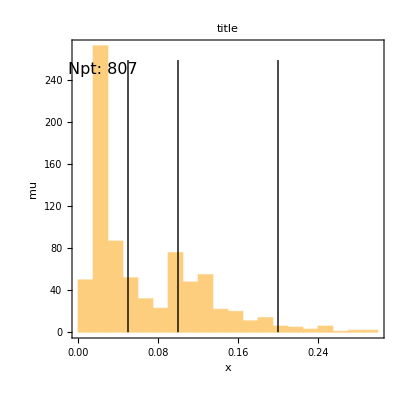

```mathematica
(*setup for arguments*)
title="title";
xtitle="x";
ytitle="mu";
plotrange={0.00001,1,1,1200};
stretchx=1;stretchy=1;
barseperator={-1,-0.2,-0.1,-0.05,0.05,0.1,0.2,1};
legendlabel="";
epilogtext={};
highlightrange={0.2,100};
unhighlightsize=0.0075;


(*correlation plot*)
PDFCorrelationplot7[Flatten[data,1],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogtext,highlightrange,unhighlightsize]

binset={-1,-0.2,-0.1,-0.05,0,0.05,0.1,0.2,1};
lineelement={{binset[[2]],"",Blue},{binset[[3]],"",Blue},{binset[[4]],"",Blue},{binset[[6]],"",Blue},{binset[[7]],"",Blue},{binset[[8]],"",Blue}};

(*histogram*)
histplot4[Flatten[data,1]/.LF1[a__]:>{a}[[3]],title,xtitle,ytitle,binset,lineelement,{0,0.3},20]
```

### add residue to data label

```mathematica
Dimensions[mydtadata]
mydtadata[[1,1]][["label"]]
mydtadata[[2,1]][["label"]]
mydtadata[[3,1]][["label"]]
```

{3,57}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Pt,Ymn,Ymx,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*method 1, operate the LF*)
residuetmp1=
Table[
mydtadata[[iexpt,iset]]/.LF[a__]:>LF[Sequence@@{a},({a}[[5]]-{a}[[11]])/{a}[[12]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
(*add label*)
Table[
residuetmp1[[iexpt,iset]][["label"]]=Join[residuetmp1[[iexpt,iset]][["label"]],{"residue"}];
"dummy",
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
```

```mathematica
(*method 2: use the exist function *)
residuetmp2=
Table[
addresidue[mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
```

```mathematica
(*set up a new {LF[residue], LF[residue],...} data and use Datamethods[["add"]] to add the residue as new element of data*)
residuetmp3=
Table[
residueinloop=mydtadata[[iexpt,iset]][["data"]]/.LF[a__]:>LF[({a}[[5]]-{a}[[11]])/{a}[[12]] ];
Datamethods[["add"]][mydtadata[[iexpt,iset]],residueinloop,{"residue"}],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
```

```mathematica
(*check three methods get the same result*)
residuetmp1[[1,1]][["data"]][[1]]
residuetmp2[[1,1]][["data"]][[1]]
residuetmp3[[1,1]][["data"]][[1]]
residuetmp1[[1,1]][["label"]]
residuetmp2[[1,1]][["label"]]
residuetmp3[[1,1]][["label"]]
```

LF[2.739,0.07,0.741,0.40205,0.402631,0.009654,0.999,0.024,0.004,-0.01131,0.4134,0.0062,-2.99,0.07,2.739,-1.73694]

LF[2.739,0.07,0.741,0.40205,0.402631,0.009654,0.999,0.024,0.004,-0.01131,0.4134,0.0062,-2.99,0.07,2.739,-1.73694]

LF[2.739,0.07,0.741,0.40205,0.402631,0.009654,0.999,0.024,0.004,-0.01131,0.4134,0.0062,-2.99,0.07,2.739,-1.73694]

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,residue}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,residue}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,residue}

```mathematica
(*add residue*)
(*residue at -1 -th column*)
(*
mydtadata=
Table[
addresidue[mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
*)
```

```mathematica
(*
mydtadata[[1,1]][["label"]]
Datamethods[["getNcolumn"]][mydtadata[[1,1]] ]
*)
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,residue}

16

### set a class with data struture LF[x,Q,iset=1,...Nset] for Nset of residue (or other observables)

```mathematica
Dimensions[mydtadata]
mydtadata[[1,1]][["label"]]
mydtadata[[2,15]][["label"]]
mydtadata[[3,10]][["label"]]
```

{3,57}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Pt,Ymn,Ymx,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*get data as [[expt,Npt,{residue},Nset]]*)(*method 1: read label 13, method 2: read label -1*)
residuetmp3=
Table[
Datamethods[["picktolist"]][residuetmp3[[iexpt,iset]],{-1} ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
```

```mathematica
Dimensions[residuetmp3]
residuetmp3[[1,1]]
```

{3,57,1}

{{-1.73694,1.06836,0.993023,0.543333,0.901622,-0.0171795,-0.2635,0.451395,1.44,-0.306531,-1.86653,-1.36708,-1.5772,-1.17222,-1.64434,-0.556552,-1.08188,-2.532,-1.17154,-1.38184,1.23981,0.511207,1.89696,-0.279811,0.573333,-0.648889,0.0721818,-0.693103,-1.67396,-2.05228,-0.0194915,-1.91679,1.3598,-1.25137,-0.455833,1.16593,0.527907,1.44465,1.56526,-0.69439,2.13857,-0.849744,1.10286,-0.345429,0.4875,-0.197429,-0.11,1.27488,1.35349,0.959211,0.8445,-0.145814,1.77,1.89808,2.16903,0.148929,-1.28806,-0.790645,0.619032,-0.733611,0.731419,1.74442,1.74316,1.25607,0.00352381,1.19875,-1.60062,-0.70192,-1.02096,-0.46088,0.00988889,0.105793,-0.833833,0.331333,-0.193571,0.125188,0.349941,1.07712,0.137056,1.67884,0.0702727,1.46686,1.647,1.44575,0.0614,1.5314,0.4515,1.12933,2.02,-0.383478,0.487347,0.289245,-1.18579,-0.0901695,-0.509123,-0.184063,0.967143,-0.403768,-0.00434783,1.10538,0.424571,0.818933,-1.13457,1.6758,1.74848,-1.24171,0.655397,-1.00779,1.22042,-0.134923,0.903803,0.982667,-0.617627,-0.141772,-1.88658,-0.374722,-0.541447,-0.696176,0.0406122,-0.315319,-0.539167,-1.14855,0.934355,0.935333,0.917818,0.142075,0.724,1.59277,-1.032,-0.42697,0.05,-0.807381,-0.454048,0.929535,-0.6122,0.376271,-0.555455,0.618491,0.195091,-0.4225,-0.176562,0.408,-0.752759,-0.560312,-0.689459,-0.102973,-0.651538,-0.519524,1.29896,1.72754,2.69381,-0.691533,0.181784,-1.6727,0.533696,0.708409,0.17408,0.461241,-1.0374,-0.246226,1.75213,0.110472,-0.222474,1.47365,0.803304,0.670714,-2.37041,-0.241722,-0.56945,1.78247,-1.13922,0.189417,0.38904,-1.2908,0.821,-0.136,0.3766,-0.107818,0.557833,0.784833,0.723462,1.58415,-0.351481,-0.494909,-0.531707,-0.0021875,-0.897143,-0.391667,-1.06132,-0.455946,1.27833,0.96619,-1.93773,-2.31952,0.591034,1.55258,0.273548,-0.565128,-2.44432,0.943929,0.235185,2.14222,-1.53649,-0.873659,-0.672432,-0.283103,0.997407,1.43704,-0.904138,-0.683889,1.09795,-0.585714,-0.71,-0.3035,-0.9515,-1.9305,-0.533333,0.901154,-1.23786,-0.596333,0.117407,1.21679,-0.139444,-0.378333,-1.44263,0.787778,0.884783,-1.42958,-1.07875,-0.239583,1.31425,-0.867304,0.548286,-0.365857,-1.62887,0.669143,0.148562,-1.97126,0.478737,0.418211,-0.893,-0.625833,1.26946,-0.418875,-1.12363,0.0296667,-0.111333,-0.5154,-2.07492,-0.486462,0.780923,0.558846,-2.081,-1.1085,0.9228,0.6188,-0.747,0.7525,1.82067,2.8062,0.609914,0.162281,-0.26,0.266061,0.317692,2.04627,-0.471325,0.259,-1.90743,1.08831,0.366667,0.858824,0.673182,1.0373,-0.638788,0.117045,-1.19787,0.5142,-0.0640741,0.574507,-0.379848,0.966667,-0.983043,1.92298,-1.54192,0.613137,0.255781,-0.361,1.4666,-0.625625,-1.01848,1.72121,-1.46028,-1.26833,-1.18132,-1.7,-1.6325,1.48841,-0.906889,0.119667,0.554194,-1.41364,-0.103437,-2.02618,0.734848,0.495128,-0.531622,-0.243543,-1.12349,-0.933318,0.333391,-1.17396,0.33784,-0.904,-0.863615,-2.0675,0.727333,-0.417297,-0.461381,-1.0095,0.507,-0.953375,-0.417125,-1.31318,-0.00870588,-1.5425,-0.0304211,-1.47172,-1.16075,-1.934,-0.909111,0.212778,-0.4086,1.30413,-0.0446,0.5329,0.296215}}

```mathematica
(*transf to [[expt,Npt,{residue},Nset]] format*)
residuetmp3=
Table[
Transpose[residuetmp3[[iexpt]],{3,2,1}],
{iexpt,1,Dimensions[residuetmp3][[1]]}
];
```

```mathematica
Dimensions[residuetmp3[[1]] ]
Length[residuetmp3[[1,1,1]] ]
```

{337,1,57}

57

```mathematica
(*transf to [[expt,Npt,Nset]] format*)
(*CT14NNLO: [[expt,Npt]]=LF[obs0,...obs56]*)
residuetmp3=
Table[
Table[
(*1 represent residue index*)
residuetmp3[[iexpt,ix,1]]/.List->LF,
{ix,1,Length[residuetmp3[[iexpt]] ]}
],
{iexpt,1,Length[residuetmp3]}
];

Table[
Dimensions[residuetmp3[[iexpt]] ],
{iexpt,1,Length[residuetmp3]}
]
```

{{337},{250},{220}}

```mathematica
residuetmp3[[1,1]]
```

LF[-1.73694,-1.75145,-1.85677,-1.655,-1.76919,-1.62613,-1.74387,-1.72048,-1.81129,-1.74452,-1.71919,-1.75081,-1.7321,-1.78258,-1.73677,-1.725,-1.75161,-1.69548,-1.77806,-1.66984,-1.7779,-1.83065,-1.67565,-1.84871,-1.60306,-1.53935,-1.88968,-1.82871,-1.57532,-1.48323,-1.87806,-1.71613,-1.76258,-1.78645,-1.68774,-1.73452,-1.72806,-1.71177,-1.76839,-1.77468,-1.69065,-1.64774,-1.76774,-1.65565,-1.81742,-1.96613,-1.51919,-1.71694,-1.76274,-1.75952,-1.72855,-1.77839,-1.70097,-1.80516,-1.80274,-1.81355,-1.75355]

```mathematica
mydtadata[[1,1]][["label"]]
mydtadata[[2,1]][["label"]]
mydtadata[[3,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Pt,Ymn,Ymx,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*set residue data LF[x,Q,iset,...,Nset]*)
(*step1: set x,Q*)
xQresidueclass=
Table[
Datamethods[["take"]][mydtadata[[iexpt,1]],{-2,-1}]
,{iexpt,1,Length[mydtadata]}
];

Datamethods[["getNpt"]][xQresidueclass[[1]] ]
Datamethods[["getNcolumn"]][xQresidueclass[[1]] ]
(*xQresidueclass[[1]][["data"]];*)

(*step2: add residue of Nset elements*)
xQresidueclass=
Table[
Nset=Length[mydtadata[[iexpt]] ];
datalabel=Table[ToString[iset],{iset,1,Nset}];
(*add LF[x,Q] & LF[residue 1,2,3,...,57]*)
Datamethods[["add"]][xQresidueclass[[iexpt]],residuetmp3[[iexpt]],datalabel]
,{iexpt,1,Length[mydtadata]}
];

Datamethods[["getNpt"]][xQresidueclass[[1]] ]
Datamethods[["getNcolumn"]][xQresidueclass[[1]] ]
```

337

2

337

59

```mathematica
xQresidueclass[[1]][["label"]]
```

{x,Q,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

### run one time of PDF ifamily, it seems for calculation of deltaR, we need to run one time PDF

```mathematica
(*setup pdf function*)
pdfResetCTEQ;
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
PdsDir=
pdfFamilyParseCTEQ[myPDFsetDir<>"*pds",ifamily];
```

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

### extract {x,Q} value and get f(x,Q,flavour) for all flavours (-5~5 && 6, 7, 8) {6,7,8} = {dbar/ubar, d/u, s+sbar/ubar+dbar}

```mathematica
mydtadata[[1,1]][["label"]]
mydtadata[[2,1]][["label"]]
mydtadata[[3,1]][["label"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

{Pt,Ymn,Ymx,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*inteprate f(x,Q) by {x,Q} of exptdata*)
fxQsamept2class=
Table[
(*since every iset of expt data has the same {x,Q}, we only take iset=1*)
(*take x,Q value of data*)
Dtadatatmp=Datamethods[["take"]][mydtadata[[iexpt,1]],{-2,-1}];
(*make class*)
Pdsread[["fxQsamept"]][Dtadatatmp,myPDFsetDir,PDFsetmethod,flavour],
{iexpt,1,Dimensions[mydtadata][[1]]},{flavour,-5,5(*Dimensions[mydtadata][[2]]*)}
];
```

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

Included 0 more files in the PDF family 1

Included 57 more files in the PDF family 1

```mathematica
Dimensions[fxQsamept2class]
(*print gluon f(x,Q) for 57 sets*)
fxQsamept2class[[1,6]][["label"]]
fxQsamept2class[[1,6]][["data"]][[1]]
```

{3,11}

{x,Q,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

LF[0.07,2.739,25.9303,25.9178,25.9154,25.8698,25.7764,25.0297,25.6175,25.7181,25.7159,26.1325,25.7501,25.8071,26.0691,25.1851,26.7085,26.2172,25.1272,25.6056,26.2637,26.4187,25.4989,26.03,25.8655,25.8531,26.003,25.9912,25.8786,26.2489,25.3884,25.2292,26.3602,25.5429,26.4977,25.9228,25.9089,25.9877,25.8552,25.4063,26.4885,26.5799,25.5841,25.8212,25.8695,25.9725,25.3433,27.4308,24.9578,26.7908,25.5008,25.9843,25.863,25.9012,25.9569,26.1105,25.9993,25.7329,26.4271]

```mathematica
(*add customized flavour for parton density function (flavour = 6,7,8)*)
fxQsamept2class=
Table[
Join[fxQsamept2class[[iexpt]],setextrafxQ[fxQsamept2class[[iexpt]] ] ],
{iexpt,1,Dimensions[fxQsamept2class][[1]]}
];
```

```mathematica
Dimensions[fxQsamept2class]
(*print f8 f(x,Q) for 57 sets*)
fxQsamept2class[[1,14]][["label"]]
fxQsamept2class[[1,14]][["data"]][[1]]
```

{3,14}

{x,Q,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

LF[0.07,2.739,0.534907,0.530174,0.544732,0.575366,0.510364,0.51426,0.5456,0.549516,0.510386,0.527382,0.539973,0.457399,0.622676,0.544895,0.525156,0.532181,0.546117,0.51675,0.555229,0.530968,0.53839,0.532572,0.536356,0.517812,0.554619,0.542053,0.529017,0.539063,0.527647,0.527553,0.539627,0.52722,0.546647,0.525995,0.542741,0.54219,0.529528,0.515255,0.558038,0.356288,0.703032,0.510549,0.543575,0.536148,0.53469,0.561624,0.516931,0.534084,0.535213,0.526959,0.547309,0.538852,0.529071,0.541552,0.567353,0.557529,0.380534]

### correlation, dr*correlation, deltaR calculation

```mathematica
(*check Npt and data elements of f(x,Q) & residue are the same*)
Datamethods[["getNpt"]][fxQsamept2class[[1,1]] ]
Datamethods[["getNcolumn"]][fxQsamept2class[[1,1]] ]

Datamethods[["getNpt"]][xQresidueclass[[1]] ]
Datamethods[["getNcolumn"]][xQresidueclass[[1]] ]
```

337

59

337

59

```mathematica
fmax=Length[fxQsamept2class[[1]] ]
```

14

```mathematica
(*calculate correlation*)
corrfxQdtaobsclass=
Table[
corrfxQdtaobs[xQresidueclass[[i]],fxQsamept2class[[i,flavour+6]] ],
{i,1,Length[xQresidueclass]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*correlation*)
dRcorrfxQdtaobsclass=
Table[
dRcorrfxQdtaobs[xQresidueclass[[i]],fxQsamept2class[[i,flavour+6]] ],
{i,1,Length[xQresidueclass]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*)
deltaRclass=
Table[
getdeltaRclass[xQresidueclass[[i]] ],
{i,1,Length[xQresidueclass]}
];
```

```mathematica
Dimensions[corrfxQdtaobsclass]
Dimensions[dRcorrfxQdtaobsclass]
Dimensions[deltaRclass]
```

{3,14}

{3,14}

{3}

```mathematica
(*check  dR*correlation*)
(*check one point*)
corrfxQdtaobsclass[[1,6]][["data"]][[1]]
dRcorrfxQdtaobsclass[[1,6]][["data"]][[1]]
deltaRclass[[1]][["data"]][[1]]
(*the result of dR*corr/(dR*corr) = 1 *)
corrfxQdtaobsclass[[1,6]][["data"]][[1,3]]*deltaRclass[[1]][["data"]][[1,3]]/dRcorrfxQdtaobsclass[[1,6]][["data"]][[1,3]]
```

LF[0.07,2.739,-0.424129] LF[0.07,2.739,-0.186197] LF[0.07,2.739,0.43901]

1.

## tutorial: A. chapter “read package” includes packages and some global variables; title “Correlation plots project” includes all functions in this program. run them to initialize under title “Correlation plots project (implementation part)”: = B. section “inteprete and save pdf data into files” read .dta files and .pds files then save f(x,Q, flavour) information for (x,Q) of experiments you input 1. set .dta file path of the PDFset you use by myPDFsetDir ex: CT14NNLODir=”/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/”; myPDFsetDir=CT14NNLODir 2. set PDFDataDir which store data of f(x,Q,flavour=0~5 ) PDFDataDir=”/home/botingw/code/pdf_correlation/data/sameptcorr/”<>”pdfxQnew/”; 3. set datalistFile to get information of experiments in datalist (it seems you need to set it as absolute path) ex: datalistFile=”/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica”; 5. set exptlist for experiments you want to show, input exptid printed by “printprocessbyPDFset”: exptlist={101,102,103} 6. run all subsections until subsection “save f(x,Q) data into files” to save parton density function data C. title “read f(x,Q) and make plots of correlation of experiments & f(x,Q), default mode: Corr(residue, f(x,Q,flavour)) ” read f(x,Q,flavour) of experiments you choose and .dta files then make plots of correlation, dr*correlation and deltaR 1. set .dta file path of the PDFset you use by myPDFsetDir ex: CT14NNLODir=”/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/”; myPDFsetDir=CT14NNLODir 2. set PDFDataDir which store data of f(x,Q,flavour=0~5 ) PDFDataDir=”/home/botingw/code/pdf_correlation/data/sameptcorr/”<>”pdfxQnew/”; 3. set datalistFile to get information of experiments in datalist (it seems you need to set it as absolute path) ex: datalistFile=”/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica”; 4. run function “printprocessbyPDFset” to see the info of experiments you can use ex: printprocessbyPDFset[myPDFsetdtafile,datalistFile] 5. set exptlist for experiments you want to show, input exptid printed by “printprocessbyPDFset”: exptlist={101,102,103} 6. run subsection “set input arguments” 7. run next subsection and next... 8. when you run the last subsection “manipulate”, you will get the result